## Beam Physics Note 33

## (Revised) 16 May 2001

# Physical Constants, Notations and Units for Accelerator Physics

Rachel T. Burgess,  John M. Jowett, James Jones

What's new in Version 6.0?

Updated for Mathematica Version 6
Tools for symbol management and tracking of physical dimensions.
DimensionCheck much simplified to work with internal database, the constant symbols defined in the package are included in the database.

### New in Version 6.1

In Mathematica Version 4.1, the source file of the Miscellaneous`ConstantsUnits` package contains the comment

As of CODATA 1998,some conventions used for the electron and muon g-factors,and for the electron,muon and neutron magnetic moments,are different than before;they are all expressed as a negative number in CODATA 1998,and a factor of two that was previously divided out of the electron g-factor is present.

The value of the constant ElectronGFactor has been re-defined.  This has been taken account of here by adjusting the definition of the symbol G_eto reflect common usage in accelerator physics and so that it has the same value as before.  This is done by testing on the version number.
N.B. There were changes to other things (such as the muon g factor - they do not seem to affect this package (?).

## Introduction

This note is the documentation for a Mathematica [1,2] package designed to provide symbols for physical constants,  such as  r_e, the classical radius of the electron, commonly occurring in accelerator physics (and other branches of physics!).  The properties of these symbols include their values and units in a very natural way.   In addition the package provides capabilities for painless conversions between many systems of units and for checking that the dimensions of expressions are consistent.

The package also load the Utilities`Notation` package that is distributed with Mathematica.  This allows you to define compound symbols like β_x which will not evaluate to β_63 if there happens to be a variable x with the value 63.  See the documentation of that package for further information.

The present package adds additional functionality by making it very simple to register new symbols with their meaning and physical units, compound or otherwise, when you introduce them.  It maintains an internal database of the symbols that makes it easy to check the physical dimensions of any expression containing them.

Basic use of the package is via a palette of buttons that will appear on your screen when you load it.

An additional feature is a 2-D plotting function (similar to Mathematica's Plot) that will take account the physical units of a function and independent variable and label the plot axes accordingly.

Our motivation in writing this package was to simplify common sorts of manipulations of physical formulas:  in the past, these involved retrieving values of physical constants (e.g., from a reference book),  plugging in numbers and making sure that the units come out right.

Mathematica's standard packages for dealing with units and physical constants go a long way to solving these problems.  However we found that we could enhance their functionality considerably.  For example, we found that the packages lacked functions to reduce any expression to the (conventionally) fundamental SI units and for checking the dimensional consistency of any expression.  Our package fills these gaps.   It also provides robust instant conversion between different systems of units (thus it is as easy to express energies in GeV as in joules).

The physical constants include most of those listed in Section 1.3 of [3];  values were cross-checked with [4].

To make the package available, you need only copy a command from the "Setup" section into a Mathematica notebook of your own.  The "Examples" section illustrates basic use of the package and is intended to provide sufficient documentation.

The latest version should always be available on-line at

http://home.cern.ch/jowett/Madtomma/

This notebook is based on the template for package and notebook development by R. Maeder  and supplied with Mathematica 3.0.

This notebook adheres to the conventions for Mathematica package structure and documentation set out in [2].  As such it serves as the development medium for the package itself.  For this reason , some sections of the printed versions of this document are hidden.  They contain the definitions ("code") of the functions.  The visible sections contain the documentation and examples of interest to users.

## Reference

#### Title

Physical Constants and Notations for Accelerator Physicste

#### Author

Rachel T. Burgess, John M. Jowett.

#### Summary

Provide notations and values for constants occurring in accelerator physics.

#### Copyright

© Copyright CERN.1999

The copyright and all other rights relating to this computer software, in whatever form, including but not limited to the source code, the object code and user documentation, are vested in CERN. 

CERN, on a royalty-free and non-exclusive basis, hereby grants permission to use, copy, change, modify, translate, display, distribute and make available this computer software, subject to the following conditions:

(1) this computer software is provided on an as-is basis and CERN provides no express or implied warranties of any kind, including but not limited to those of merchantability, fitness for a particular purpose and non-infringement of the proprietary rights, such as copyrights, patents and trade secrets, of third parties. CERN accepts no liability whatsoever for or in connection with the use of this computer software; 

(2) all copies made of this computer software or of parts thereof shall include  his copyright statement in full; 

(3) however, if this computer software or parts thereof are made available in any other form than their original form, or are included in any other computer software, the following short acknowledgement only must be mentioned in the copyright statement and in the user documentation (or, in the absence thereof, in any other appropriate place) concerning the computer software thus made available or created: 

"This product includes computer software created and made available by CERN. This acknowledgement shall be mentioned in full in any product which includes the CERN computer software included herein or parts thereof."

#### Notebook Version

23.1

#### Mathematica Version

6.0

#### History

Version 1.0 released as Beam Physics note 33, 16 July 1999.

Version 2.0 released with addition of PhysicalUnits, PhysicalUnitsPlot etc. as requested by J.P. Koutchouk, 26 August 1999.

Version 3.0 released with addition of IntroduceSymbol, SymbolsUnits, etc. DimensionCheck much simplified to use internal database, 15 January 2001.

Version 3.1 released to take account of CODATA change to ElectronGFactor in Mathematica 4.1.  Pavillon Brasserie, Vevey, 16 May 2001.

#### Keywords

Physical, fundamental, constants, notation, accelerator

#### Source

[3],[4] and other standards.

#### Warnings

Note: all cells marked as "InitializationCell" will be written to the Auto-Save package. This package can then be read in programs that use it with Needs["Accelerator`ConstantsUnits`"]. Cells not intended to belong to the package should not have this property.

#### Requirements

This package uses the following package, documented here more fully than it is in the Help Browser.  In fact the usage is fairly simple, mainly of the Symbolize function.

Utilities`Notation`

Note that while working on this package notebook, it is necessary to evaluate

```mathematica
Needs["Notation`"]
```

Notation::shdw: Symbol "Notation" appears in multiple contexts {"Notation`", "Global`"}; definitions in context "Notation`" may shadow or be shadowed by other definitions.

Notation::gshadw: The symbol '"Notation"' has been used in the global context. The Notation package needs the full use of the symbol '"Notation"' and has therefore removed this symbol from the global context.

Notation::gshadw: The symbol '"NotationBoxTag"' has been used in the global context. The Notation package needs the full use of the symbol '"NotationBoxTag"' and has therefore removed this symbol from the global context.

to make the corresponding palette available.  The Symbolize command must never be typed directly.  Enter it via the palette.

It also uses the standard packages

Miscellaneous`Units`, Miscellaneous`PhysicalConstants`

and actually modifies some of their content.

## Setup

This section explains how to load the package file.  The contents of this file are equivalent to the following sections (Interface, Implementation, Epilog) in which the package is developed.  These sections are hidden when this notebook is used as the package documentation but may be inspected in the online copy of this notebook that can be found in the appropriate  sub-directory of the directory added to the $Path variable below.

### Search Path (ESSENTIAL!)

To have access to this and other packages, you may need to add our packages directory to your search path.  This is system-dependent and the latest information about arranging it on CERN computer systems can be found at

http://home.cern.ch/jowett/Madtomma/AboutFiles.html

and is not reproduced here.  I strongly recommend that you modify your kernel initialisation file once and for all as explained on this page.  Then all our packages will be found as easily as the Standard Packages that come with Mathematica.

### Loading the Package

To load the package, just evaluate the expression

Needs["Accelerator`ConstantsUnits`"]

This is all you need to start using the package in your own applications.

## Interface

### Set up the package context, including public imports

```mathematica
BeginPackage["Accelerator`ConstantsUnits`",{"Notation`","Units`","PhysicalConstants`"}]
```

Accelerator`ConstantsUnits`

We get basic values of fundamental constants and units from the standard packages.  The function Convert is also very useful.

### Define symbols

It is necessary to define the symbols before declaring their usage messages.  We do not need to do this for ℏ since it is not a composite symbol.  If we do, it creates problems when the package loads. The following cells must be created with the Notation Palette.

Since plain α is used too often, add a subscript to the notation

```mathematica
Symbolize[Subscript[α, s]]
```

```mathematica
Symbolize[Subscript[r, e]]
```

```mathematica
Symbolize[Subscript[λ, e]]
```

```mathematica
Symbolize[Subscript[λ̄, e]]
```

```mathematica
Symbolize[Subscript[G, e]]
```

```mathematica
Symbolize[Subscript[μ, 0]]
```

```mathematica
Symbolize[Subscript[ϵ, 0]]
```

```mathematica
Symbolize[Subscript[m, e]]
```

```mathematica
Symbolize[Subscript[m, p]]
```

```mathematica
Symbolize[Subscript[m, n]]
```

```mathematica
Symbolize[Subscript[m, d]]
```

```mathematica
Symbolize[Subscript[m, μ]]
```

```mathematica
Symbolize[Subscript[m, Z]]
```

```mathematica
Symbolize[Subscript[m, W]]
```

```mathematica
Symbolize[Subscript[a, ∞]]
```

```mathematica
Symbolize[Subscript[μ, B]]
```

```mathematica
Symbolize[Subscript[μ, N]]
```

```mathematica
Symbolize[Subscript[r, p]]
```

```mathematica
Symbolize[Subscript[Z, 0]]
```

```mathematica
Symbolize[Subscript[σ, T]]
```

```mathematica
Symbolize[Subscript[σ, SB]]
```

### Usage messages for the exported functions and the context itself

```mathematica
ConstantsUnits::usage ="ConstantsUnits.m is a package that provides notations and values for constants occurring in accelerator physics."
```

ConstantsUnits.m is a package that provides notations and values for constants occurring in accelerator physics.

```mathematica
TeV::usage="TeV is a unit of energy.";
GeV::usage="GeV is a unit of energy.";
MeV::usage="MeV is a unit of energy.";
keV::usage="keV is a unit of energy.";
```

```mathematica
c::usage="c is a symbol for the speed of light in vacuum; it evaluates numerically with N[ ].";
```

c::shdw: Symbol "c" appears in multiple contexts {"Accelerator`ConstantsUnits`", "Global`"}; definitions in context "Accelerator`ConstantsUnits`" may shadow or be shadowed by other definitions.

```mathematica
ℏ::usage="ℏ is a symbol for the reduced Planck constant; it evaluates numerically with N[ ].";
```

```mathematica
Subscript[α, s]::usage="α_s is a symbol for the fine structure constant; it evaluates numerically with N[ ].";
```

```mathematica
e::usage="e is a symbol for the electron charge; it evaluates numerically with N[ ].";
```

```mathematica
Subscript[r, e]::usage="r_e is a symbol for the classical radius of the electron; it evaluates numerically with N[ ].";
```

```mathematica
Subscript[λ, e]::usage="λ_e is a symbol for the Compton wavelength of the electron; it evaluates numerically with N[ ].";
```

```mathematica
Subscript[λ̄, e]::usage="(λ̄)_e is a symbol for the reduced Compton wavelength of the electron; it evaluates numerically with N[ ].";
```

```mathematica
Subscript[G, e]::usage="G_e is a symbol for the anomalous magnetic moment of the electron; it evaluates numerically with N[ ].";
```

```mathematica
Subscript[μ, 0]::usage="\\ \  is a symbol for the permeability of the vacuum; it evaluates numerically with N[ ].";
```

```mathematica
Subscript[ϵ, 0]::usage="\  is a symbol for the permittivity of the vacuum; it evaluates numerically with N[ ].";
```

```mathematica
Subscript[m, e]::usage="m_e is a symbol for the mass of the electron; it evaluates numerically with N[ ].";
```

```mathematica
Subscript[m, p]::usage="m_p is a symbol for the mass of the proton; it evaluates numerically with N[ ].";
```

```mathematica
Subscript[m, n]::usage="m_n is a symbol for the mass of the neutron; it evaluates numerically with N[ ].";
```

```mathematica
Subscript[m, d]::usage="m_d is a symbol for the mass of the deuteron; it evaluates numerically with N[ ].";
```

```mathematica
Subscript[m, μ]::usage="m_μ is a symbol for the mass of the muon; it evaluates numerically with N[ ].";
```

```mathematica
Subscript[m, Z]::usage="m_Z is a symbol for the mass of the Z-particle; it evaluates numerically with N[ ].";
```

```mathematica
Subscript[m, W]::usage="m_Wis a symbol for the mass of the W-particle; it evaluates numerically with N[ ].";
```

```mathematica
Subscript[a, ∞]::usage="is a symbol for the Bohr radius; it evaluates numerically with N[ ].";
```

```mathematica
Subscript[μ, B]::usage="is a symbol for the Bohr magneton; it evaluates numerically with N[ ].";
```

```mathematica
Subscript[μ, N]::usage="μ_N is a symbol for the nuclear magneton; it evaluates numerically with N[ ].";
```

```mathematica
Subscript[r, p]::usage="r_p is a symbol for the classical radius of the proton; it evaluates numerically with N[ ].";
```

```mathematica
Subscript[Z, 0]::usage="Z_0 is a symbol for the impedance of free space; it evaluates numerically with N[ ].";
```

```mathematica
Subscript[σ, T]::usage="σ_T is a symbol for the Thomson cross section; it evaluates
numerically with N[ ].";
```

```mathematica
Subscript[σ, SB]::usage="σ_SB is a symbol for the Stefan-Boltzmann constant; it evaluates numerically with N[ ].";
```

```mathematica
ToFundamentalSI::usage="toFundamentalSI[f] converts the quantity f to fundamental SI units.  Generally this helps to simplify the expressions of the units.";
```

ToFundamentalSI::shdw: Symbol "ToFundamentalSI" appears in multiple contexts {"Accelerator`ConstantsUnits`", "Global`"}; definitions in context "Accelerator`ConstantsUnits`" may shadow or be shadowed by other definitions.

```mathematica
ClassicalProtonRadius::usage="ClassicalProtonRadius is the classical radius of the proton."
```

ClassicalProtonRadius is the classical radius of the proton.

```mathematica
DimensionCheck::usage="DimensionCheck[f] returns an expression showing the dimensional consistency of f, based on the internal database of symbols and units maintained by the ConstantsUnits package.\nThe alternative form DimensionCheck[f,symbolsUnits] uses a list of {symbol,unit} pairs given as second argument instead of the internal database.";
```

```mathematica
NumericalValueUnits::usage="NumericalValueUnits[f] interprets f as the product of a numerical value fn and symbolic units fu and returns {fn,fu}.";
```

```mathematica
PhysicalUnits::usage="PhysicalUnits[f] interprets f as the product of a numerical value fn and symbolic units fu and returns fu.";
```

```mathematica
NumericalValue::usage="NumericalValue[f] interprets f as the product of a numerical value fn and symbolic units fu and returns fn.";
```

```mathematica
IntroduceSymbol::usage="IntroduceSymbol[symbol,usagetext,units] introduces a symbol, registers its units for purposes of dimensional analysis and defines a usage message for it.";
```

```mathematica
SymbolsUnits::usage="SymbolsUnits[] returns a list of all symbols and units registered in the internal database.";
```

```mathematica
PhysicalUnitsPlot::usage="PhysicalUnitsPlot[f,{x,xmin,xmax}] works like Plot but removes the physical units of f and x before plotting.  Further, it creates labels for the axes from the symbolic forms of f and x and indicates their units.  It has all options of Plot except AxesLabel.";
```

### Error messages for the exported objects

```mathematica
ConstantsUnits::badarg = "You called `1` with argument `2`!"
```

You called `1` with argument `2`!

### Modifications of standard package content

Fix these as they are exact values.  It seems we should not do the following in the Private context of this package.

```mathematica
SpeedOfLight=299792458 Meter/Second
```

(299792458 Meter)/Second

```mathematica
ThomsonCrossSection=0.66524616/10^28 Meter^2
```

6.65246×10^-29 Meter^2

```mathematica
ClassicalProtonRadius=Convert[ElectronCharge^2/((4π VacuumPermittivity) ProtonMass SpeedOfLight^2),Meter]
```

1.5347×10^-18 Meter

## Implementation

This part contains the actual definitions and any auxiliary functions that should not be visible outside.

### Begin the private context (implementation part)

```mathematica
Begin["`Private`"]
```

Accelerator`ConstantsUnits`Private`

### Definition of auxiliary functions and local (static) variables

#### Starting prime number for DimensionCheck

```mathematica
minGodelPrimeIndex = 10;
```

### Definition of the exported functions

Use a conventional notation for common constants and set up its numerical evaluation to the values given in the Miscellaneous`PhysicalConstants` package or others derived here.

#### Conversion to basic SI units

This seems to be lacking in the Units package.  It allow you to cancel units.  See examples

```mathematica
ToFundamentalSI[f_]:=SI[f]//.Units`Private`$ToFundamental
```

#### Checking consistency of dimensions

The list symbolsWithUnits should be of the form {{<symbol>,<units>},...}. This function builds up a rule that assigns values of the form <prime number><units> to each symbol appearing in the expression f.  The prime numbers are distinct and start with the Prime[minGodelPrimeIndex+1].  This rule is then applied to f.

```mathematica
DimensionCheck[f_,symbolsWithUnits_List]:=Expand[f//.MapIndexed[(#1⟦1⟧->Prime[minGodelPrimeIndex+First[#2]] #1⟦2⟧&),Union[symbolsWithUnits]]];
DimensionCheck[f_]:=DimensionCheck[f,Accelerator`ConstantsUnits`Private`$SymbolsUnits]
```

#### Further convenient units

It would be better to have these units inside the Units package.  But this works quite well nevertheless.

```mathematica
TeV= Tera ElectronVolt;GeV=Giga ElectronVolt;
MeV=Mega ElectronVolt;keV=Kilo ElectronVolt;eV=ElectronVolt;
```

#### Speed of light

```mathematica
N[c]=SpeedOfLight
```

(299792458 Meter)/Second

#### Planck constant

```mathematica
N[ℏ]=PlanckConstantReduced
```

1.05457×10^-34 Joule Second

#### Fine structure constant

```mathematica
N[Subscript[α, s]]=FineStructureConstant
```

0.00729735

#### Electron charge

```mathematica
N[e]=ElectronCharge
```

1.60218×10^-19 Coulomb

#### Electron classical radius

```mathematica
N[Subscript[r, e]]=ClassicalElectronRadius
```

2.81794×10^-15 Meter

#### Electron Compton wavelength

```mathematica
N[Subscript[λ, e]]=ElectronComptonWavelength
```

2.42631×10^-12 Meter

```mathematica
N[Subscript[λ̄, e]]=N[ElectronComptonWavelength/(2 π)]
```

3.86159×10^-13 Meter

#### Electron anomalous magnetic moment

```mathematica
N[Subscript[G, e]]=If[$VersionNumber≥4.1,(-ElectronGFactor-2)/2,ElectronGFactor-1]
```

0.00115965

This takes account of changes in definitions in Mathematica Version 4.1.  In any case the symbol G_e should have the value

```mathematica
0.00115965670000006682
```

0.00115966

#### Permeability of vacuum

```mathematica
N[Subscript[μ, 0]]=Convert[VacuumPermeability,Henry/Meter]
```

(Henry π)/(2500000 Meter)

#### Permittivity of vacuum

```mathematica
N[Subscript[ϵ, 0]]=Convert[VacuumPermittivity,Farad/Meter]
```

(625000 Farad)/(22468879468420441 Meter π)

#### Electron mass

```mathematica
N[Subscript[m, e]]=ElectronMass
```

9.10938×10^-31 Kilogram

#### Proton mass

```mathematica
N[Subscript[m, p]]=ProtonMass
```

1.67262×10^-27 Kilogram

#### Neutron mass

```mathematica
N[Subscript[m, n]]=NeutronMass
```

1.67493×10^-27 Kilogram

#### Deuteron mass

```mathematica
N[Subscript[m, d]]=DeuteronMass
```

3.34358×10^-27 Kilogram

#### Muon mass

```mathematica
N[Subscript[m, μ]]=MuonMass
```

1.88353×10^-28 Kilogram

#### Z-particle mass

```mathematica
N[Subscript[m, Z]]=Convert[N[91.187GeV/(SpeedOfLight^2)],Kilogram]
```

1.62556×10^-25 Kilogram

#### W-particle mass

```mathematica
N[Subscript[m, W]]=Convert[N[80.4GeV/(SpeedOfLight^2)],Kilogram]
```

1.43326×10^-25 Kilogram

#### Bohr radius

```mathematica
N[Subscript[a, ∞]]=BohrRadius
```

5.29177×10^-11 Meter

#### Bohr magneton

```mathematica
N[Subscript[μ, B]]=Convert[N[(ElectronCharge PlanckConstantReduced)/(2 ProtonMass)],Joule/Tesla]
```

(5.05078×10^-27 Joule)/Tesla

#### Nuclear magneton

```mathematica
N[Subscript[μ, N]]=Convert[N[(ElectronCharge PlanckConstantReduced)/(2 ProtonMass)],Joule/Tesla]
```

(5.05078×10^-27 Joule)/Tesla

#### Proton classical radius

```mathematica
N[Subscript[r, p]]=ClassicalProtonRadius
```

1.5347×10^-18 Meter

#### Impedance of free space

```mathematica
N[Subscript[Z, 0]]=Convert[N[VacuumPermeability SpeedOfLight],Ohm]
```

376.73 Ohm

#### Thomson cross section

```mathematica
N[Subscript[σ, T]]=ThomsonCrossSection
```

6.65246×10^-29 Meter^2

#### Stefan-Boltzmann constant

```mathematica
N[Subscript[σ, SB]]=StefanConstant
```

(5.6704×10^-8 Watt)/(Kelvin^4 Meter^2)

#### Separating numerical values and units

```mathematica
NumericalValueUnits[Times[a_/;NumericQ[a],b__]]:={a,Times@b};
NumericalValueUnits[a_/;NumericQ[a]]:={a,1};
NumericalValueUnits[a_]:={1,a}
```

```mathematica
NumericalValue[f_]:=First[NumericalValueUnits[f]]
```

```mathematica
PhysicalUnits[f_]:=Last[NumericalValueUnits[f]]
```

#### Plotting with the units removed

This function only works when it can be verified that the units of the upper and lower limits of the range are equivalent when reduced to fundamental SI units.  So it is possible to express the two limits in different units provided the physical dimensions are the same.

The definition of this function is tricky and may not be very robust (see the examples).  However it only produces graphical results so the risk of transmitting errors to other calculations is small.

For simplicity, implement options by direct inheritance from Plot, it is hardly worth setting up an options filter.  Note that the AxesLabel option will just be ignored.  Maybe it should allow override of the default?

```mathematica
SetAttributes[PhysicalUnitsPlot,HoldAll];
Options[PhysicalUnitsPlot]=Options[Plot];
PhysicalUnitsPlot[f_,{var_,varmin_,varmax_},opts___?OptionQ]/;PhysicalUnits[ToFundamentalSI[varmin]]==PhysicalUnits[ToFundamentalSI[varmax]]:=
	Module[{vunits,funits,nvar},
		vunits=PhysicalUnits[N[varmin]];funits=PhysicalUnits[N[f/.var->varmin]];
		fnew=f/.var->nvar vunits;
		If[FreeQ[funits,Plus],Plot[Evaluate[fnew/funits],{nvar,ToFundamentalSI[varmin/vunits],ToFundamentalSI[varmax/vunits]},AxesLabel->{StandardForm[HoldForm[var] [vunits]],StandardForm[HoldForm[f][ funits]]},opts],Print["Units of ordinate appear to be inconsistent."]]]
```

#### Analogue of ListPlot (NOT WRITTEN)

An analogue of ListPlot does not seem to make so much sense.

#### Analogue of Plot3D and others (NOT WRITTEN)

Exercise for the student

#### Database of symbols and dimensions

Build a list of symbols and the units they come in.  Start by taking everything that exists in this package.

```mathematica
$SymbolsUnits=({#1,PhysicalUnits[N[#1]]}&)/@ToExpression[Names["Accelerator`ConstantsUnits`*"]]
```

{{a_∞,Meter},{c,Meter/Second},{1.5347×10^-18 Meter,Meter},{ConstantsUnits,ConstantsUnits},{DimensionCheck,DimensionCheck},{e,Coulomb},{ElectronVolt Giga,ElectronVolt Giga},{G_e,1},{IntroduceSymbol,IntroduceSymbol},{ElectronVolt Kilo,ElectronVolt Kilo},{ElectronVolt Mega,ElectronVolt Mega},{m_d,Kilogram},{m_e,Kilogram},{m_n,Kilogram},{m_p,Kilogram},{m_W,Kilogram},{m_Z,Kilogram},{m_μ,Kilogram},{NumericalValue,NumericalValue},{NumericalValueUnits,NumericalValueUnits},{PhysicalUnits,PhysicalUnits},{PhysicalUnitsPlot,PhysicalUnitsPlot},{r_e,Meter},{r_p,Meter},{SymbolsUnits,SymbolsUnits},{ElectronVolt Tera,ElectronVolt Tera},{ToFundamentalSI,ToFundamentalSI},{Z_0,Ohm},{α_s,1},{ϵ_0,Farad/Meter},{(λ̄)_e,Meter},{λ_e,Meter},{μ_0,Henry/Meter},{μ_B,Joule/Tesla},{μ_N,Joule/Tesla},{σ_SB,Watt/(Kelvin^4 Meter^2)},{σ_T,Meter^2},{ℏ,Joule Second}}

Functions like DimensionCheck will produce two copies of their symbol.  A few constants defined like ClassicalProtonRadius are eliminated by the second test.

```mathematica
$SymbolsUnits=Select[$SymbolsUnits,First[#1]=!=Last[#1]&&!(NumericQ[First[#1]/Last[#1]])&]
```

{{a_∞,Meter},{c,Meter/Second},{e,Coulomb},{G_e,1},{m_d,Kilogram},{m_e,Kilogram},{m_n,Kilogram},{m_p,Kilogram},{m_W,Kilogram},{m_Z,Kilogram},{m_μ,Kilogram},{r_e,Meter},{r_p,Meter},{Z_0,Ohm},{α_s,1},{ϵ_0,Farad/Meter},{(λ̄)_e,Meter},{λ_e,Meter},{μ_0,Henry/Meter},{μ_B,Joule/Tesla},{μ_N,Joule/Tesla},{σ_SB,Watt/(Kelvin^4 Meter^2)},{σ_T,Meter^2},{ℏ,Joule Second}}

From the outside we can access this database as Accelerator`NewConstantsUnits`Private`$SymbolsUnits

#### Function for symbol management

Should do better than this: what if the symbol is already in the database and we want to change its dimensions (e.g. to correct an error)?

```mathematica
IntroduceSymbol[sym_Symbol,usagetext_String,unit_]:=($SymbolsUnits=Append[Select[$SymbolsUnits,(First[#1]=!=sym)&],
{sym,unit}];
sym::"usage"=ToString[sym]<>" "<>usagetext<>" (units: "<>ToString[unit]<>")")
```

```mathematica
SymbolsUnits[]:=$SymbolsUnits
```

### Definitions for system functions

```mathematica
(* Sin/: Sin[x_]^2 := 1 - Cos[x]^2 *)
```

### Restore protection of system symbols

```mathematica
(* Protect[ Evaluate[protected] ] *)
```

### End the private context

```mathematica
End[ ]
```

Accelerator`ConstantsUnits`Private`

## Epilog

This section protects exported symbols and ends the package.

### Protect exported symbol

Need to think about what to protect.  Note that the standard PhysicalConstants package does note protect its objects.  However it might be good for us to protect symbols that might easily be used by accident for another purpose, like c and e.  ? ?

```mathematica
Protect[c,e]
```

{c,e}

Alternative: protect all exported symbols

```mathematica
Protect[Evaluate[$Context <> "*"]]
```

{a⎵Subscript⎵Infinity,ClassicalProtonRadius,ConstantsUnits,DimensionCheck,GeV,G⎵Subscript⎵e,IntroduceSymbol,keV,MeV,m⎵Subscript⎵d,m⎵Subscript⎵e,m⎵Subscript⎵n,m⎵Subscript⎵p,m⎵Subscript⎵W,m⎵Subscript⎵Z,m⎵Subscript⎵μ,NumericalValue,NumericalValueUnits,PhysicalUnits,PhysicalUnitsPlot,r⎵Subscript⎵e,r⎵Subscript⎵p,SymbolsUnits,TeV,ToFundamentalSI,Z⎵Subscript⎵0,α⎵Subscript⎵s,ϵ⎵Subscript⎵0,λ⎵Overscript⎵Underscore⎵Subscript⎵e,λ⎵Subscript⎵e,μ⎵Subscript⎵0,μ⎵Subscript⎵B,μ⎵Subscript⎵N,σ⎵Subscript⎵SB,σ⎵Subscript⎵T,ℏ}

### End the package context

```mathematica
EndPackage[ ]
```

Open the palette to make it easy.  This has to be done outside the package context.

```mathematica
(*If[$Remote,Null,NotebookOpen["\\\\srdserve1\\astec\\software\\mathematica\\accelerator\\ConstantsUnitsPalette.nb"]]*)
```

## Examples and Tests

### Formulas involving physical constants

The basic function of the Accelerator`ConstantsUnits` package is to let you use conventional symbols such as

```mathematica
Subscript[λ̄, e]
```

(λ̄)_e

In fact, these compound symbols are best entered from the palette of buttons that appears when you load the package.  It is possible, however, to type them from the keyboard if you know what you are doing. See below.

Like all properly defined objects in Mathematica, each has a usage message

```mathematica
?Subscript[λ̄, e]
```

(λ̄)_e is a symbol for the reduced Compton wavelength of the electron; it evaluates numerically with N[ ].

```mathematica
?ℏ
```

ℏ is a symbol for the reduced Planck constant; it evaluates numerically with N[ ].

```mathematica
?keV
```

keV is a unit of energy.

But these symbols are more than just symbols.  They have the properties that you would expect under numerical evaluation

```mathematica
N[Subscript[λ̄, e]]
```

3.86159×10^-13 Meter

It is therefore easy to "plug in numbers" in symbolic formulas

```mathematica
N[Subscript[λ̄, e]/Subscript[r, e]]
```

137.036

Here is a table of some symbols from the package, together with their numerical evaluations.  It is constructed with the help of a pure function [1].

```mathematica
TableForm[
	({#,N[#]}&)/@{c,e,Subscript[r, e],Subscript[m, e],ℏ,Subscript[λ, e],Subscript[λ̄, e],Subscript[α, s],Subscript[G, e],Subscript[Z, 0],Subscript[σ, T]}
]
```

c | (2.99792×10^8 Meter)/Second
e | 1.60218×10^-19 Coulomb
r_e | 2.81794×10^-15 Meter
m_e | 9.10938×10^-31 Kilogram
ℏ | 1.05457×10^-34 Joule Second
λ_e | 2.42631×10^-12 Meter
(λ̄)_e | 3.86159×10^-13 Meter
α_s | 0.00729735
G_e | 0.00115965
Z_0 | 376.73 Ohm
σ_T | 6.65246×10^-29 Meter^2

### Unit conversions

The distance (in energy) between integer spin resonances in an electron storage ring is

```mathematica
N[(Subscript[m, e] c^2)/Subscript[G, e]]
```

(7.05997×10^-11 Kilogram Meter^2)/Second^2

With the Convert function, this can be converted to the units you prefer

```mathematica
Convert[N[(Subscript[m, e] c^2)/Subscript[G, e]],ChevalVapeur Fortnight]
```

7.93558×10^-20 ChevalVapeur Fortnight

```mathematica
Convert[N[(Subscript[m, e] c^2)/Subscript[G, e]],GeV]
```

0.440648 ElectronVolt Giga

This can be converted to SI units with another function

```mathematica
SI[%]
```

7.05997×10^-11 Joule

As a further example, we show how easy it is to convert units of integrated luminosity.  Suppose that the average luminosity of LEP is 0.3×10^32 cm^-2 s^-1, how much luminosity will be accumulated in a day?  The answer should be expressed in inverse pico-barns.

```mathematica
Convert[((0.3×10^32)/((Centi Meter)^2 Second))×(1 Day),1/(Pico Barn)]
```

2.592/(Barn Pico)

This expression was formatted for readability rather than brevity!

### Reserved symbols

Following tradition in physics, some fundamental constants are denoted by simple letters which thereby become unavailable for other purposes.

```mathematica
?c
```

c is a symbol for the speed of light in vacuum; it evaluates numerically with N[ ].

The symbols defined by the package are protected because you will not normally want to change the values of the fundamental constants.  So the following assignment will fail:

```mathematica
c=22
```

Set::wrsym: Symbol c is Protected.

22

```mathematica
N[c]
```

(2.99792×10^8 Meter)/Second

### Standard packages made available

Most of the values of fundamental physical constants are actually obtained from the standard package Miscellaneous`PhysicalConstants`.  Everything defined by this package, together with Miscellaneous`Units`, is therefore available as described in the documentation for these packages. In a few cases,  values of physical constants are corrected by the present package.  For example, the speed of light is defined exactly,

```mathematica
SpeedOfLight
```

(299792458 Meter)/Second

```mathematica
Precision[SpeedOfLight]
```

∞

but is often converted to "floating point"

```mathematica
Precision[N[SpeedOfLight]]
```

MachinePrecision

The Convert function comes from Miscellaneous`Units`.  It is useful for converting quantities to different units provided the dimensions are right.

```mathematica
Convert[21 Joule,MeV]
```

1.31072×10^14 ElectronVolt Mega

```mathematica
Convert[21. Joule, Foot/Second]
```

Convert::incomp: Incompatible units in 21.\ Joule and Foot/Second.

21. Joule

The function Symbolize from the package Utilities`Notation` is used to define compound symbols such as (λ̄)_e.  It's palette will usually appear when the package is loaded.  Consult its documentation for how to define additional symbols and notations.

### New units defined by the package

Note that the package defines units that are commonly used in accelerator physics for ease of input.  However they usually reduce immediately to symbols defined in the standard package Miscellaneous`Units`

```mathematica
?GeV
```

GeV is a unit of energy.

```mathematica
GeV
```

ElectronVolt Giga

### Reduction to a fundamental set of units

It is often useful to reduce quantities to the so-called fundamental SI units:

```mathematica
ToFundamentalSI[ 120 MeV]
```

(1.92261×10^-11 Kilogram Meter^2)/Second^2

Without this function, we would not be able to recognise equivalent units

```mathematica
ToFundamentalSI[Volt/Meter]
```

(Kilogram Meter)/(Ampere Second^3)

```mathematica
ToFundamentalSI[Volt/Meter==Newton/Coulomb]
```

True

```mathematica
ToFundamentalSI[Newton/(Meter Ampere)==Tesla]
```

True

### Registering symbols

We can introduce a compound symbol λ_Q as follows (this input is easily constructed using the palette that comes with the package):

```mathematica
Notation[Subscript[λ, Q] ⟺ lq];
IntroduceSymbol[lq,"is the length of our quadrupole magnet.",Meter]
```

lq is the length of our quadrupole magnet. (units: Meter)

The Notation function makes it easier to input the symbol.  We just need to type lq instead of λ_Q but the latter form will appear once notebook cells are converted to standard form (e.g. in the output of an evaluation). The IntroduceSymbol function (whose first argument must be identical to the alias) defines a usage message for the symbol that can be accessed by typing

```mathematica
?lq
```

lq is the length of our quadrupole magnet. (units: Meter)

and registers that it should have units of length (Meter) in the package database. The IntroduceSymbol function's value is just the usage message.

The use of this will be explained in the next section.  First, let's introduce some more symbols to make the demonstrations non-trivial:

```mathematica
Notation[Subscript[E, b] ⟺ EGeV];
IntroduceSymbol[EGeV,"is the beam energy.",GeV]
```

EGeV is the beam energy. (units: ElectronVolt Giga)

```mathematica
Notation[Subscript[a, θ] ⟺ a];
IntroduceSymbol[a,"is the dimensionless scaling parameter.",1]
```

a is the dimensionless scaling parameter. (units: 1)

```mathematica
Notation[ρ ⟺ rho];
IntroduceSymbol[rho,"is the bending radius.",Meter]
```

rho is the bending radius. (units: Meter)

```mathematica
Notation[Subscript[ρ, y] ⟺ rhoy];
IntroduceSymbol[rhoy,"is the bending radius.",Meter];
```

### Checking dimensions

The function DimensionCheck provides a simple method for checking the dimensions in  formulas

Applying the function should give an expression with correct, homogeneous units. Note, however, that you should not assume that the result has anything in common with the original expression except its dimensions.  In particular it is not numerically equal to it.

```mathematica
DimensionCheck[Subscript[λ, Q]]
```

59 Meter

Each symbol is actually replaced by its unit multiplied by a unique prime number. Prime factorisations of the result will be useful in certain cases for reconstructing the formula (this was inspired, somewhat whimsically, by the proof of  Gödel's Theorem).  To take a slightly more complicated expression that is dimensionless overall, we find

```mathematica
DimensionCheck[Subscript[λ, Q]/(Subscript[λ, Q]/Subscript[a, θ]+Subscript[ρ, y])]
```

1829/3190

which is a dimensionally homogeneous expression, showing that the expression is dimensionally consistent.

If the expression contains symbols that are not known to the package database

```mathematica
DimensionCheck[Subscript[λ, Q]/(Subscript[ρ, y]+(Sin[(π Subscript[a, θ]^2 s)/Subscript[λ, Q]] Subscript[λ, Q])/Subscript[a, θ])]
```

{(59 Meter)/(0.+101 Meter),(59 Meter)/(101 Meter+59/31 Meter Sin[10.2341/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[18.4214/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[24.5619/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[24.5619/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[33.2609/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[41.96/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[41.96/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[194.449/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[202.636/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[203.148/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[205.706/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[208.776/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[208.776/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[217.475/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[226.174/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[226.174/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[252.783/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[252.783/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[363.312/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[363.312/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[368.429/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[368.429/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[368.429/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[378.663/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[386.85/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[387.362/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[389.921/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[392.991/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[392.991/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[401.69/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[410.389/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[410.389/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[562.878/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[571.065/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[577.205/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[577.205/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[585.904/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[594.603/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[594.603/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[621.212/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[621.212/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[731.741/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[731.741/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[736.858/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[736.858/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[736.858/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[747.092/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[755.279/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[761.42/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[761.42/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[770.119/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[778.818/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[778.818/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[784.958/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[793.146/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[805.427/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[805.427/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[915.955/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[915.955/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[931.307/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[939.494/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[940.006/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[942.564/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[945.634/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[945.634/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[954.333/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[963.032/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[963.032/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[969.173/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[977.36/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[989.641/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[989.641/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1100.17/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1100.17/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1105.29/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1105.29/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1105.29/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1115.52/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1123.71/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1124.22/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1126.78/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1129.85/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1129.85/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1138.55/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1147.25/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1147.25/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1153.39/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1161.57/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1173.86/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1173.86/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1284.38/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1284.38/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1299.74/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1307.92/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1314.06/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1314.06/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1322.76/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1331.46/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1331.46/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1337.6/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1345.79/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1358.07/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1358.07/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1468.6/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1468.6/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1473.72/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1473.72/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1473.72/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1483.95/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1492.14/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1498.28/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1498.28/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1506.98/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1515.68/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1515.68/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1521.82/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1530./Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1542.28/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1542.28/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1652.81/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1652.81/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1668.16/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1676.35/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1676.86/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1679.42/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1682.49/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1682.49/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1691.19/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1699.89/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1699.89/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1706.03/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1714.22/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1726.5/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1726.5/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1837.03/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1837.03/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1842.14/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1842.14/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1842.14/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1852.38/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1860.57/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1861.08/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1863.64/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1866.71/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1866.71/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1875.41/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1884.1/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1884.1/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1890.25/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1898.43/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1910.71/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1910.71/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2021.24/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2021.24/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2036.59/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2044.78/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2050.92/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2050.92/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2059.62/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2068.32/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2068.32/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2074.46/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2082.65/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2094.93/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2094.93/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2205.46/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2205.46/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2210.57/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2210.57/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2210.57/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2220.81/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2229./Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2235.14/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2235.14/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2243.83/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2252.53/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2252.53/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2258.67/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2266.86/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2279.14/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2279.14/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2389.67/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2389.67/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2405.02/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2413.21/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2413.72/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2416.28/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2419.35/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2419.35/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2428.05/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2436.75/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2436.75/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2442.89/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2451.08/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2463.36/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2463.36/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2573.89/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2573.89/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2579./Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2579./Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2579./Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2589.24/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2597.42/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2597.94/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2600.49/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2603.56/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2603.56/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2612.26/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2620.96/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2620.96/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2627.1/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2635.29/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2647.57/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2647.57/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2758.1/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2758.1/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2773.45/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2781.64/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2787.78/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2787.78/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2796.48/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2805.18/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2805.18/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2811.32/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2819.5/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2831.79/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2831.79/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2942.31/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2942.31/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2947.43/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2947.43/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2947.43/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2957.67/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2965.85/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2971.99/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2971.99/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2980.69/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2989.39/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2989.39/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2995.53/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3003.72/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3016./Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3016./Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3126.53/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3126.53/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3141.88/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3150.07/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3150.58/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3153.14/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3156.21/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3156.21/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3164.91/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3173.61/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3173.61/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3179.75/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3187.93/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3200.21/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3200.21/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3310.74/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3310.74/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3315.86/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3315.86/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3315.86/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3326.09/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3334.28/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3340.42/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3340.42/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3349.12/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3357.82/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3357.82/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3384.43/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3384.43/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3494.96/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3494.96/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3510.31/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3518.5/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3519.01/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3521.57/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3524.64/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3524.64/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3533.34/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3542.03/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3542.03/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3684.29/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3684.29/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3684.29/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3694.52/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3702.71/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3703.22/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3705.78/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3708.85/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3708.85/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3717.55/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3726.25/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3726.25/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3752.86/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3752.86/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3863.39/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3863.39/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3878.74/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3886.93/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3893.07/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3893.07/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3901.76/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3910.46/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3910.46/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4052.72/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4052.72/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4052.72/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4062.95/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4071.14/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4077.28/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4077.28/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4085.98/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4094.68/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4094.68/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4247.17/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4255.35/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4255.87/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4258.42/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4261.49/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4261.49/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4270.19/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4278.89/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4278.89/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4305.5/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4305.5/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4416.03/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4416.03/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4421.15/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4421.15/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4421.15/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4431.38/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4439.57/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4440.08/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4442.64/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4445.71/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4445.71/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4454.41/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4463.11/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4463.11/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4615.6/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4623.78/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4629.92/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4629.92/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4638.62/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4647.32/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4647.32/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4673.93/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4673.93/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4784.46/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4784.46/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4789.58/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4789.58/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4789.58/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4799.81/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4808./Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4814.14/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4814.14/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4822.84/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4831.54/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4831.54/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4837.68/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4845.86/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4858.15/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4858.15/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4968.67/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4968.67/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4984.02/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4992.21/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4992.72/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4995.28/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4998.35/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4998.35/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5007.05/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5015.75/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5015.75/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5021.89/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5030.08/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5042.36/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5042.36/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5152.89/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5152.89/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5158.01/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5158.01/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5158.01/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5168.24/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5176.43/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5176.94/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5179.5/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5182.57/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5182.57/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5191.27/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5199.97/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5199.97/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5206.11/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5214.29/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5226.57/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5226.57/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5337.1/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5337.1/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5352.45/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5360.64/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5366.78/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5366.78/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5375.48/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5384.18/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5384.18/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5390.32/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5398.51/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5410.79/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5410.79/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5521.32/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5521.32/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5526.43/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5526.43/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5526.43/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5536.67/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5544.86/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5551./Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5551./Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5559.7/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5568.39/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5568.39/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5574.53/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5582.72/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5595./Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5595./Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5705.53/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5705.53/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5720.88/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5729.07/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5729.58/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5732.14/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5735.21/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5735.21/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5743.91/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5752.61/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5752.61/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5758.75/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5766.94/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5779.22/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5779.22/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5889.75/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5889.75/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5894.86/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5894.86/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5894.86/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5905.1/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5913.28/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5913.8/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5916.35/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5919.43/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5919.43/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5928.12/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5936.82/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5936.82/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5942.96/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5951.15/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5963.43/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5963.43/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6073.96/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6073.96/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6089.31/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6097.5/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6103.64/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6103.64/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6112.34/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6121.04/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6121.04/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6127.18/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6135.37/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6147.65/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6147.65/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6258.18/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6258.18/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6263.29/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6263.29/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6263.29/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6273.53/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6281.71/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6287.85/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6287.85/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6296.55/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6305.25/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6305.25/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6311.39/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6319.58/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6331.86/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6331.86/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6442.39/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6442.39/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6457.74/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6465.93/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6466.44/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6469./Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6472.07/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6472.07/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6480.77/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6489.47/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6489.47/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6495.61/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6503.79/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6516.08/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6516.08/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6626.6/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6626.6/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6631.72/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6631.72/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6631.72/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6641.96/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6650.14/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6650.65/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6653.21/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6656.28/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6656.28/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6664.98/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6673.68/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6673.68/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6679.82/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6688.01/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6700.29/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6700.29/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6810.82/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6810.82/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6826.17/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6834.36/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6840.5/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6840.5/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6849.2/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6857.9/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6857.9/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6864.04/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6872.22/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6884.5/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6884.5/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6995.03/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6995.03/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7000.15/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7000.15/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7000.15/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7010.38/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7018.57/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7024.71/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7024.71/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7033.41/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7042.11/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7042.11/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7048.25/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7056.44/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7068.72/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7068.72/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7179.25/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7179.25/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7194.6/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7202.79/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7203.3/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7205.86/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7208.93/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7208.93/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7217.63/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7226.32/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7226.32/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7232.46/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7240.65/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7252.93/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7252.93/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7363.46/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7363.46/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7368.58/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7368.58/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7368.58/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7378.81/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7387./Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7393.14/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7393.14/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7401.84/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7410.54/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7410.54/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7437.15/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7437.15/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7547.68/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7547.68/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7563.03/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7571.21/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7571.73/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7574.29/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7577.36/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7577.36/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7586.05/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7594.75/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7594.75/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7737.01/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7737.01/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7737.01/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7747.24/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7755.43/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7755.94/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7758.5/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7761.57/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7761.57/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7770.27/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7778.97/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7778.97/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7805.58/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7805.58/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7916.11/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7916.11/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7931.46/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7939.64/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7945.78/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7945.78/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7954.48/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7963.18/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7963.18/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[8105.44/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[8105.44/Meter])}

then they can always be added

```mathematica
IntroduceSymbol[s,"is the azimuth.",Meter];
```

```mathematica
DimensionCheck[Subscript[λ, Q]/(Subscript[ρ, y]+(Sin[(π Subscript[a, θ]^2 s)/Subscript[λ, Q]] Subscript[λ, Q])/Subscript[a, θ])]
```

{(59 Meter)/(0.+101 Meter),(59 Meter)/(101 Meter+59/31 Meter Sin[10.2341/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[18.4214/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[24.5619/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[24.5619/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[33.2609/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[41.96/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[41.96/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[194.449/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[202.636/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[203.148/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[205.706/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[208.776/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[208.776/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[217.475/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[226.174/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[226.174/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[252.783/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[252.783/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[363.312/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[363.312/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[368.429/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[368.429/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[368.429/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[378.663/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[386.85/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[387.362/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[389.921/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[392.991/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[392.991/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[401.69/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[410.389/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[410.389/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[562.878/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[571.065/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[577.205/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[577.205/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[585.904/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[594.603/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[594.603/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[621.212/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[621.212/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[731.741/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[731.741/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[736.858/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[736.858/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[736.858/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[747.092/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[755.279/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[761.42/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[761.42/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[770.119/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[778.818/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[778.818/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[784.958/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[793.146/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[805.427/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[805.427/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[915.955/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[915.955/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[931.307/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[939.494/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[940.006/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[942.564/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[945.634/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[945.634/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[954.333/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[963.032/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[963.032/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[969.173/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[977.36/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[989.641/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[989.641/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1100.17/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1100.17/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1105.29/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1105.29/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1105.29/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1115.52/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1123.71/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1124.22/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1126.78/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1129.85/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1129.85/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1138.55/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1147.25/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1147.25/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1153.39/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1161.57/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1173.86/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1173.86/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1284.38/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1284.38/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1299.74/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1307.92/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1314.06/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1314.06/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1322.76/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1331.46/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1331.46/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1337.6/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1345.79/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1358.07/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1358.07/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1468.6/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1468.6/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1473.72/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1473.72/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1473.72/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1483.95/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1492.14/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1498.28/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1498.28/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1506.98/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1515.68/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1515.68/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1521.82/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1530./Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1542.28/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1542.28/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1652.81/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1652.81/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1668.16/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1676.35/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1676.86/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1679.42/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1682.49/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1682.49/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1691.19/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1699.89/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1699.89/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1706.03/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1714.22/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1726.5/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1726.5/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1837.03/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1837.03/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1842.14/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1842.14/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1842.14/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1852.38/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1860.57/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1861.08/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1863.64/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1866.71/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1866.71/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1875.41/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1884.1/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1884.1/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1890.25/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1898.43/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1910.71/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[1910.71/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2021.24/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2021.24/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2036.59/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2044.78/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2050.92/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2050.92/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2059.62/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2068.32/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2068.32/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2074.46/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2082.65/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2094.93/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2094.93/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2205.46/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2205.46/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2210.57/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2210.57/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2210.57/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2220.81/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2229./Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2235.14/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2235.14/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2243.83/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2252.53/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2252.53/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2258.67/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2266.86/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2279.14/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2279.14/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2389.67/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2389.67/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2405.02/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2413.21/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2413.72/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2416.28/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2419.35/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2419.35/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2428.05/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2436.75/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2436.75/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2442.89/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2451.08/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2463.36/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2463.36/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2573.89/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2573.89/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2579./Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2579./Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2579./Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2589.24/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2597.42/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2597.94/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2600.49/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2603.56/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2603.56/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2612.26/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2620.96/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2620.96/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2627.1/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2635.29/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2647.57/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2647.57/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2758.1/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2758.1/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2773.45/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2781.64/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2787.78/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2787.78/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2796.48/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2805.18/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2805.18/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2811.32/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2819.5/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2831.79/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2831.79/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2942.31/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2942.31/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2947.43/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2947.43/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2947.43/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2957.67/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2965.85/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2971.99/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2971.99/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2980.69/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2989.39/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2989.39/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[2995.53/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3003.72/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3016./Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3016./Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3126.53/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3126.53/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3141.88/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3150.07/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3150.58/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3153.14/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3156.21/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3156.21/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3164.91/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3173.61/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3173.61/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3179.75/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3187.93/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3200.21/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3200.21/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3310.74/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3310.74/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3315.86/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3315.86/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3315.86/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3326.09/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3334.28/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3340.42/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3340.42/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3349.12/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3357.82/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3357.82/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3384.43/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3384.43/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3494.96/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3494.96/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3510.31/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3518.5/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3519.01/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3521.57/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3524.64/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3524.64/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3533.34/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3542.03/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3542.03/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3684.29/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3684.29/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3684.29/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3694.52/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3702.71/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3703.22/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3705.78/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3708.85/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3708.85/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3717.55/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3726.25/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3726.25/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3752.86/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3752.86/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3863.39/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3863.39/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3878.74/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3886.93/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3893.07/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3893.07/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3901.76/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3910.46/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[3910.46/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4052.72/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4052.72/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4052.72/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4062.95/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4071.14/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4077.28/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4077.28/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4085.98/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4094.68/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4094.68/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4247.17/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4255.35/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4255.87/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4258.42/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4261.49/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4261.49/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4270.19/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4278.89/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4278.89/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4305.5/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4305.5/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4416.03/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4416.03/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4421.15/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4421.15/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4421.15/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4431.38/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4439.57/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4440.08/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4442.64/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4445.71/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4445.71/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4454.41/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4463.11/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4463.11/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4615.6/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4623.78/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4629.92/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4629.92/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4638.62/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4647.32/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4647.32/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4673.93/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4673.93/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4784.46/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4784.46/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4789.58/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4789.58/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4789.58/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4799.81/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4808./Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4814.14/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4814.14/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4822.84/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4831.54/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4831.54/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4837.68/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4845.86/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4858.15/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4858.15/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4968.67/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4968.67/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4984.02/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4992.21/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4992.72/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4995.28/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4998.35/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[4998.35/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5007.05/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5015.75/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5015.75/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5021.89/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5030.08/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5042.36/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5042.36/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5152.89/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5152.89/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5158.01/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5158.01/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5158.01/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5168.24/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5176.43/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5176.94/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5179.5/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5182.57/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5182.57/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5191.27/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5199.97/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5199.97/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5206.11/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5214.29/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5226.57/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5226.57/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5337.1/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5337.1/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5352.45/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5360.64/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5366.78/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5366.78/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5375.48/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5384.18/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5384.18/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5390.32/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5398.51/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5410.79/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5410.79/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5521.32/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5521.32/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5526.43/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5526.43/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5526.43/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5536.67/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5544.86/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5551./Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5551./Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5559.7/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5568.39/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5568.39/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5574.53/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5582.72/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5595./Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5595./Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5705.53/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5705.53/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5720.88/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5729.07/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5729.58/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5732.14/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5735.21/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5735.21/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5743.91/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5752.61/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5752.61/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5758.75/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5766.94/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5779.22/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5779.22/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5889.75/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5889.75/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5894.86/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5894.86/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5894.86/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5905.1/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5913.28/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5913.8/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5916.35/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5919.43/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5919.43/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5928.12/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5936.82/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5936.82/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5942.96/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5951.15/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5963.43/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[5963.43/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6073.96/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6073.96/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6089.31/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6097.5/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6103.64/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6103.64/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6112.34/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6121.04/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6121.04/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6127.18/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6135.37/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6147.65/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6147.65/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6258.18/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6258.18/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6263.29/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6263.29/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6263.29/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6273.53/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6281.71/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6287.85/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6287.85/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6296.55/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6305.25/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6305.25/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6311.39/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6319.58/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6331.86/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6331.86/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6442.39/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6442.39/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6457.74/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6465.93/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6466.44/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6469./Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6472.07/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6472.07/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6480.77/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6489.47/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6489.47/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6495.61/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6503.79/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6516.08/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6516.08/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6626.6/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6626.6/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6631.72/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6631.72/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6631.72/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6641.96/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6650.14/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6650.65/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6653.21/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6656.28/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6656.28/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6664.98/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6673.68/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6673.68/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6679.82/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6688.01/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6700.29/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6700.29/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6810.82/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6810.82/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6826.17/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6834.36/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6840.5/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6840.5/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6849.2/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6857.9/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6857.9/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6864.04/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6872.22/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6884.5/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6884.5/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6995.03/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[6995.03/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7000.15/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7000.15/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7000.15/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7010.38/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7018.57/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7024.71/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7024.71/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7033.41/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7042.11/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7042.11/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7048.25/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7056.44/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7068.72/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7068.72/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7179.25/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7179.25/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7194.6/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7202.79/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7203.3/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7205.86/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7208.93/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7208.93/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7217.63/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7226.32/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7226.32/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7232.46/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7240.65/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7252.93/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7252.93/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7363.46/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7363.46/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7368.58/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7368.58/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7368.58/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7378.81/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7387./Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7393.14/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7393.14/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7401.84/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7410.54/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7410.54/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7437.15/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7437.15/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7547.68/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7547.68/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7563.03/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7571.21/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7571.73/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7574.29/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7577.36/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7577.36/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7586.05/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7594.75/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7594.75/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7737.01/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7737.01/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7737.01/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7747.24/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7755.43/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7755.94/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7758.5/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7761.57/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7761.57/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7770.27/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7778.97/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7778.97/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7805.58/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7805.58/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7916.11/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7916.11/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7931.46/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7939.64/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7945.78/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7945.78/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7954.48/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7963.18/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[7963.18/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[8105.44/Meter]),(59 Meter)/(101 Meter+59/31 Meter Sin[8105.44/Meter])}

Sometimes further simplification is helpful or necessary to make the results of DimensionCheck completely transparent.  In this case, applying N, to force numerical evaluation, will often simplify the expression further and make it very easy to see if the expression is dimensionally consistent

```mathematica
N[%]
```

{(59. Meter)/(0.+101. Meter),(59. Meter)/(101. Meter+1.90323 Meter Sin[10.2341/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[18.4214/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[24.5619/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[24.5619/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[33.2609/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[41.96/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[41.96/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[194.449/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[202.636/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[203.148/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[205.706/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[208.776/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[208.776/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[217.475/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[226.174/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[226.174/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[252.783/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[252.783/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[363.312/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[363.312/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[368.429/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[368.429/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[368.429/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[378.663/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[386.85/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[387.362/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[389.921/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[392.991/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[392.991/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[401.69/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[410.389/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[410.389/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[562.878/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[571.065/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[577.205/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[577.205/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[585.904/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[594.603/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[594.603/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[621.212/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[621.212/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[731.741/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[731.741/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[736.858/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[736.858/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[736.858/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[747.092/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[755.279/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[761.42/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[761.42/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[770.119/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[778.818/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[778.818/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[784.958/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[793.146/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[805.427/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[805.427/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[915.955/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[915.955/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[931.307/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[939.494/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[940.006/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[942.564/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[945.634/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[945.634/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[954.333/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[963.032/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[963.032/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[969.173/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[977.36/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[989.641/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[989.641/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1100.17/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1100.17/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1105.29/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1105.29/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1105.29/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1115.52/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1123.71/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1124.22/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1126.78/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1129.85/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1129.85/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1138.55/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1147.25/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1147.25/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1153.39/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1161.57/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1173.86/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1173.86/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1284.38/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1284.38/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1299.74/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1307.92/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1314.06/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1314.06/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1322.76/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1331.46/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1331.46/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1337.6/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1345.79/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1358.07/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1358.07/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1468.6/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1468.6/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1473.72/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1473.72/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1473.72/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1483.95/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1492.14/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1498.28/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1498.28/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1506.98/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1515.68/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1515.68/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1521.82/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1530./Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1542.28/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1542.28/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1652.81/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1652.81/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1668.16/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1676.35/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1676.86/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1679.42/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1682.49/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1682.49/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1691.19/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1699.89/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1699.89/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1706.03/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1714.22/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1726.5/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1726.5/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1837.03/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1837.03/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1842.14/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1842.14/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1842.14/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1852.38/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1860.57/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1861.08/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1863.64/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1866.71/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1866.71/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1875.41/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1884.1/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1884.1/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1890.25/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1898.43/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1910.71/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[1910.71/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2021.24/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2021.24/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2036.59/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2044.78/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2050.92/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2050.92/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2059.62/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2068.32/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2068.32/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2074.46/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2082.65/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2094.93/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2094.93/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2205.46/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2205.46/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2210.57/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2210.57/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2210.57/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2220.81/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2229./Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2235.14/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2235.14/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2243.83/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2252.53/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2252.53/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2258.67/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2266.86/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2279.14/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2279.14/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2389.67/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2389.67/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2405.02/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2413.21/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2413.72/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2416.28/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2419.35/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2419.35/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2428.05/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2436.75/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2436.75/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2442.89/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2451.08/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2463.36/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2463.36/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2573.89/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2573.89/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2579./Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2579./Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2579./Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2589.24/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2597.42/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2597.94/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2600.49/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2603.56/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2603.56/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2612.26/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2620.96/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2620.96/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2627.1/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2635.29/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2647.57/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2647.57/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2758.1/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2758.1/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2773.45/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2781.64/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2787.78/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2787.78/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2796.48/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2805.18/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2805.18/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2811.32/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2819.5/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2831.79/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2831.79/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2942.31/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2942.31/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2947.43/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2947.43/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2947.43/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2957.67/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2965.85/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2971.99/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2971.99/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2980.69/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2989.39/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2989.39/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[2995.53/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3003.72/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3016./Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3016./Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3126.53/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3126.53/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3141.88/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3150.07/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3150.58/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3153.14/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3156.21/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3156.21/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3164.91/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3173.61/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3173.61/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3179.75/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3187.93/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3200.21/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3200.21/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3310.74/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3310.74/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3315.86/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3315.86/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3315.86/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3326.09/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3334.28/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3340.42/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3340.42/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3349.12/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3357.82/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3357.82/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3384.43/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3384.43/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3494.96/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3494.96/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3510.31/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3518.5/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3519.01/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3521.57/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3524.64/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3524.64/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3533.34/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3542.03/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3542.03/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3684.29/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3684.29/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3684.29/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3694.52/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3702.71/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3703.22/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3705.78/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3708.85/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3708.85/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3717.55/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3726.25/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3726.25/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3752.86/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3752.86/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3863.39/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3863.39/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3878.74/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3886.93/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3893.07/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3893.07/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3901.76/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3910.46/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[3910.46/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4052.72/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4052.72/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4052.72/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4062.95/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4071.14/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4077.28/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4077.28/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4085.98/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4094.68/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4094.68/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4247.17/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4255.35/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4255.87/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4258.42/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4261.49/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4261.49/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4270.19/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4278.89/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4278.89/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4305.5/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4305.5/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4416.03/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4416.03/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4421.15/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4421.15/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4421.15/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4431.38/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4439.57/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4440.08/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4442.64/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4445.71/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4445.71/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4454.41/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4463.11/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4463.11/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4615.6/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4623.78/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4629.92/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4629.92/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4638.62/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4647.32/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4647.32/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4673.93/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4673.93/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4784.46/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4784.46/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4789.58/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4789.58/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4789.58/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4799.81/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4808./Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4814.14/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4814.14/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4822.84/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4831.54/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4831.54/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4837.68/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4845.86/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4858.15/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4858.15/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4968.67/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4968.67/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4984.02/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4992.21/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4992.72/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4995.28/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4998.35/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[4998.35/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5007.05/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5015.75/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5015.75/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5021.89/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5030.08/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5042.36/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5042.36/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5152.89/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5152.89/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5158.01/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5158.01/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5158.01/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5168.24/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5176.43/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5176.94/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5179.5/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5182.57/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5182.57/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5191.27/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5199.97/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5199.97/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5206.11/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5214.29/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5226.57/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5226.57/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5337.1/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5337.1/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5352.45/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5360.64/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5366.78/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5366.78/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5375.48/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5384.18/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5384.18/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5390.32/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5398.51/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5410.79/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5410.79/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5521.32/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5521.32/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5526.43/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5526.43/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5526.43/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5536.67/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5544.86/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5551./Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5551./Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5559.7/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5568.39/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5568.39/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5574.53/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5582.72/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5595./Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5595./Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5705.53/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5705.53/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5720.88/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5729.07/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5729.58/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5732.14/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5735.21/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5735.21/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5743.91/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5752.61/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5752.61/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5758.75/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5766.94/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5779.22/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5779.22/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5889.75/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5889.75/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5894.86/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5894.86/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5894.86/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5905.1/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5913.28/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5913.8/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5916.35/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5919.43/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5919.43/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5928.12/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5936.82/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5936.82/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5942.96/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5951.15/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5963.43/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[5963.43/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6073.96/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6073.96/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6089.31/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6097.5/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6103.64/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6103.64/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6112.34/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6121.04/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6121.04/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6127.18/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6135.37/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6147.65/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6147.65/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6258.18/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6258.18/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6263.29/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6263.29/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6263.29/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6273.53/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6281.71/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6287.85/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6287.85/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6296.55/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6305.25/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6305.25/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6311.39/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6319.58/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6331.86/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6331.86/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6442.39/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6442.39/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6457.74/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6465.93/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6466.44/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6469./Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6472.07/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6472.07/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6480.77/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6489.47/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6489.47/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6495.61/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6503.79/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6516.08/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6516.08/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6626.6/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6626.6/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6631.72/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6631.72/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6631.72/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6641.96/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6650.14/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6650.65/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6653.21/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6656.28/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6656.28/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6664.98/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6673.68/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6673.68/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6679.82/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6688.01/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6700.29/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6700.29/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6810.82/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6810.82/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6826.17/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6834.36/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6840.5/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6840.5/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6849.2/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6857.9/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6857.9/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6864.04/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6872.22/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6884.5/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6884.5/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6995.03/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[6995.03/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7000.15/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7000.15/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7000.15/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7010.38/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7018.57/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7024.71/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7024.71/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7033.41/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7042.11/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7042.11/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7048.25/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7056.44/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7068.72/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7068.72/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7179.25/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7179.25/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7194.6/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7202.79/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7203.3/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7205.86/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7208.93/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7208.93/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7217.63/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7226.32/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7226.32/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7232.46/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7240.65/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7252.93/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7252.93/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7363.46/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7363.46/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7368.58/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7368.58/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7368.58/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7378.81/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7387./Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7393.14/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7393.14/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7401.84/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7410.54/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7410.54/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7437.15/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7437.15/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7547.68/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7547.68/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7563.03/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7571.21/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7571.73/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7574.29/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7577.36/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7577.36/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7586.05/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7594.75/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7594.75/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7737.01/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7737.01/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7737.01/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7747.24/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7755.43/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7755.94/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7758.5/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7761.57/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7761.57/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7770.27/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7778.97/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7778.97/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7805.58/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7805.58/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7916.11/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7916.11/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7931.46/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7939.64/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7945.78/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7945.78/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7954.48/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7963.18/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[7963.18/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[8105.44/Meter]),(59. Meter)/(101. Meter+1.90323 Meter Sin[8105.44/Meter])}

If the expression is not dimensionally consistent, then this will be quite obvious

```mathematica
DimensionCheck[(Subscript[λ, Q] (1-s))/(Subscript[ρ, y]+(Sin[(π Subscript[a, θ] s^2)/Subscript[λ, Q]] Subscript[λ, Q])/Subscript[a, θ])]
```

{(59. Meter)/(0.+101 Meter),(47.2 Meter)/(101 Meter+59/31 Meter Sin[0.0660267/Meter]),(37.76 Meter)/(101 Meter+59/31 Meter Sin[0.213926/Meter]),(30.68 Meter)/(101 Meter+59/31 Meter Sin[0.380314/Meter]),(30.68 Meter)/(101 Meter+59/31 Meter Sin[0.380314/Meter]),(20.65 Meter)/(101 Meter+59/31 Meter Sin[0.697407/Meter]),(10.62 Meter)/(101 Meter+59/31 Meter Sin[1.10991/Meter]),(10.62 Meter)/(101 Meter+59/31 Meter Sin[1.10991/Meter]),-(165.2 Meter)/(101 Meter+59/31 Meter Sin[23.8356/Meter]),-(174.64 Meter)/(101 Meter+59/31 Meter Sin[25.8851/Meter]),-(175.23 Meter)/(101 Meter+59/31 Meter Sin[26.016/Meter]),-(178.18 Meter)/(101 Meter+59/31 Meter Sin[26.6754/Meter]),-(181.72 Meter)/(101 Meter+59/31 Meter Sin[27.4777/Meter]),-(181.72 Meter)/(101 Meter+59/31 Meter Sin[27.4777/Meter]),-(191.75 Meter)/(101 Meter+59/31 Meter Sin[29.8152/Meter]),-(201.78 Meter)/(101 Meter+59/31 Meter Sin[32.2481/Meter]),-(201.78 Meter)/(101 Meter+59/31 Meter Sin[32.2481/Meter]),-(232.46 Meter)/(101 Meter+59/31 Meter Sin[40.2822/Meter]),-(232.46 Meter)/(101 Meter+59/31 Meter Sin[40.2822/Meter]),-(359.9 Meter)/(101 Meter+59/31 Meter Sin[83.2101/Meter]),-(359.9 Meter)/(101 Meter+59/31 Meter Sin[83.2101/Meter]),-(365.8 Meter)/(101 Meter+59/31 Meter Sin[85.5706/Meter]),-(365.8 Meter)/(101 Meter+59/31 Meter Sin[85.5706/Meter]),-(365.8 Meter)/(101 Meter+59/31 Meter Sin[85.5706/Meter]),-(377.6 Meter)/(101 Meter+59/31 Meter Sin[90.3905/Meter]),-(387.04 Meter)/(101 Meter+59/31 Meter Sin[94.3416/Meter]),-(387.63 Meter)/(101 Meter+59/31 Meter Sin[94.5913/Meter]),-(390.58 Meter)/(101 Meter+59/31 Meter Sin[95.845/Meter]),-(394.12 Meter)/(101 Meter+59/31 Meter Sin[97.3603/Meter]),-(394.12 Meter)/(101 Meter+59/31 Meter Sin[97.3603/Meter]),-(404.15 Meter)/(101 Meter+59/31 Meter Sin[101.718/Meter]),-(414.18 Meter)/(101 Meter+59/31 Meter Sin[106.172/Meter]),-(414.18 Meter)/(101 Meter+59/31 Meter Sin[106.172/Meter]),-(590. Meter)/(101 Meter+59/31 Meter Sin[199.731/Meter]),-(599.44 Meter)/(101 Meter+59/31 Meter Sin[205.583/Meter]),-(606.52 Meter)/(101 Meter+59/31 Meter Sin[210.028/Meter]),-(606.52 Meter)/(101 Meter+59/31 Meter Sin[210.028/Meter]),-(616.55 Meter)/(101 Meter+59/31 Meter Sin[216.407/Meter]),-(626.58 Meter)/(101 Meter+59/31 Meter Sin[222.88/Meter]),-(626.58 Meter)/(101 Meter+59/31 Meter Sin[222.88/Meter]),-(657.26 Meter)/(101 Meter+59/31 Meter Sin[243.275/Meter]),-(657.26 Meter)/(101 Meter+59/31 Meter Sin[243.275/Meter]),-(784.7 Meter)/(101 Meter+59/31 Meter Sin[337.545/Meter]),-(784.7 Meter)/(101 Meter+59/31 Meter Sin[337.545/Meter]),-(790.6 Meter)/(101 Meter+59/31 Meter Sin[342.282/Meter]),-(790.6 Meter)/(101 Meter+59/31 Meter Sin[342.282/Meter]),-(790.6 Meter)/(101 Meter+59/31 Meter Sin[342.282/Meter]),-(802.4 Meter)/(101 Meter+59/31 Meter Sin[351.856/Meter]),-(811.84 Meter)/(101 Meter+59/31 Meter Sin[359.61/Meter]),-(818.92 Meter)/(101 Meter+59/31 Meter Sin[365.482/Meter]),-(818.92 Meter)/(101 Meter+59/31 Meter Sin[365.482/Meter]),-(828.95 Meter)/(101 Meter+59/31 Meter Sin[373.88/Meter]),-(838.98 Meter)/(101 Meter+59/31 Meter Sin[382.374/Meter]),-(838.98 Meter)/(101 Meter+59/31 Meter Sin[382.374/Meter]),-(846.06 Meter)/(101 Meter+59/31 Meter Sin[388.428/Meter]),-(855.5 Meter)/(101 Meter+59/31 Meter Sin[396.573/Meter]),-(869.66 Meter)/(101 Meter+59/31 Meter Sin[408.949/Meter]),-(869.66 Meter)/(101 Meter+59/31 Meter Sin[408.949/Meter]),-(997.1 Meter)/(101 Meter+59/31 Meter Sin[528.89/Meter]),-(997.1 Meter)/(101 Meter+59/31 Meter Sin[528.89/Meter]),-(1014.8 Meter)/(101 Meter+59/31 Meter Sin[546.767/Meter]),-(1024.24 Meter)/(101 Meter+59/31 Meter Sin[556.423/Meter]),-(1024.83 Meter)/(101 Meter+59/31 Meter Sin[557.029/Meter]),-(1027.78 Meter)/(101 Meter+59/31 Meter Sin[560.065/Meter]),-(1031.32 Meter)/(101 Meter+59/31 Meter Sin[563.72/Meter]),-(1031.32 Meter)/(101 Meter+59/31 Meter Sin[563.72/Meter]),-(1041.35 Meter)/(101 Meter+59/31 Meter Sin[574.139/Meter]),-(1051.38 Meter)/(101 Meter+59/31 Meter Sin[584.654/Meter]),-(1051.38 Meter)/(101 Meter+59/31 Meter Sin[584.654/Meter]),-(1058.46 Meter)/(101 Meter+59/31 Meter Sin[592.133/Meter]),-(1067.9 Meter)/(101 Meter+59/31 Meter Sin[602.18/Meter]),-(1082.06 Meter)/(101 Meter+59/31 Meter Sin[617.408/Meter]),-(1082.06 Meter)/(101 Meter+59/31 Meter Sin[617.408/Meter]),-(1209.5 Meter)/(101 Meter+59/31 Meter Sin[763.021/Meter]),-(1209.5 Meter)/(101 Meter+59/31 Meter Sin[763.021/Meter]),-(1215.4 Meter)/(101 Meter+59/31 Meter Sin[770.135/Meter]),-(1215.4 Meter)/(101 Meter+59/31 Meter Sin[770.135/Meter]),-(1215.4 Meter)/(101 Meter+59/31 Meter Sin[770.135/Meter]),-(1227.2 Meter)/(101 Meter+59/31 Meter Sin[784.463/Meter]),-(1236.64 Meter)/(101 Meter+59/31 Meter Sin[796.02/Meter]),-(1237.23 Meter)/(101 Meter+59/31 Meter Sin[796.746/Meter]),-(1240.18 Meter)/(101 Meter+59/31 Meter Sin[800.376/Meter]),-(1243.72 Meter)/(101 Meter+59/31 Meter Sin[804.744/Meter]),-(1243.72 Meter)/(101 Meter+59/31 Meter Sin[804.744/Meter]),-(1253.75 Meter)/(101 Meter+59/31 Meter Sin[817.183/Meter]),-(1263.78 Meter)/(101 Meter+59/31 Meter Sin[829.718/Meter]),-(1263.78 Meter)/(101 Meter+59/31 Meter Sin[829.718/Meter]),-(1270.86 Meter)/(101 Meter+59/31 Meter Sin[838.624/Meter]),-(1280.3 Meter)/(101 Meter+59/31 Meter Sin[850.572/Meter]),-(1294.46 Meter)/(101 Meter+59/31 Meter Sin[868.653/Meter]),-(1294.46 Meter)/(101 Meter+59/31 Meter Sin[868.653/Meter]),-(1421.9 Meter)/(101 Meter+59/31 Meter Sin[1039.94/Meter]),-(1421.9 Meter)/(101 Meter+59/31 Meter Sin[1039.94/Meter]),-(1439.6 Meter)/(101 Meter+59/31 Meter Sin[1064.94/Meter]),-(1449.04 Meter)/(101 Meter+59/31 Meter Sin[1078.4/Meter]),-(1456.12 Meter)/(101 Meter+59/31 Meter Sin[1088.55/Meter]),-(1456.12 Meter)/(101 Meter+59/31 Meter Sin[1088.55/Meter]),-(1466.15 Meter)/(101 Meter+59/31 Meter Sin[1103.01/Meter]),-(1476.18 Meter)/(101 Meter+59/31 Meter Sin[1117.57/Meter]),-(1476.18 Meter)/(101 Meter+59/31 Meter Sin[1117.57/Meter]),-(1483.26 Meter)/(101 Meter+59/31 Meter Sin[1127.9/Meter]),-(1492.7 Meter)/(101 Meter+59/31 Meter Sin[1141.75/Meter]),-(1506.86 Meter)/(101 Meter+59/31 Meter Sin[1162.68/Meter]),-(1506.86 Meter)/(101 Meter+59/31 Meter Sin[1162.68/Meter]),-(1634.3 Meter)/(101 Meter+59/31 Meter Sin[1359.64/Meter]),-(1634.3 Meter)/(101 Meter+59/31 Meter Sin[1359.64/Meter]),-(1640.2 Meter)/(101 Meter+59/31 Meter Sin[1369.13/Meter]),-(1640.2 Meter)/(101 Meter+59/31 Meter Sin[1369.13/Meter]),-(1640.2 Meter)/(101 Meter+59/31 Meter Sin[1369.13/Meter]),-(1652. Meter)/(101 Meter+59/31 Meter Sin[1388.21/Meter]),-(1661.44 Meter)/(101 Meter+59/31 Meter Sin[1403.57/Meter]),-(1668.52 Meter)/(101 Meter+59/31 Meter Sin[1415.15/Meter]),-(1668.52 Meter)/(101 Meter+59/31 Meter Sin[1415.15/Meter]),-(1678.55 Meter)/(101 Meter+59/31 Meter Sin[1431.63/Meter]),-(1688.58 Meter)/(101 Meter+59/31 Meter Sin[1448.2/Meter]),-(1688.58 Meter)/(101 Meter+59/31 Meter Sin[1448.2/Meter]),-(1695.66 Meter)/(101 Meter+59/31 Meter Sin[1459.96/Meter]),-(1705.1 Meter)/(101 Meter+59/31 Meter Sin[1475.71/Meter]),-(1719.26 Meter)/(101 Meter+59/31 Meter Sin[1499.5/Meter]),-(1719.26 Meter)/(101 Meter+59/31 Meter Sin[1499.5/Meter]),-(1846.7 Meter)/(101 Meter+59/31 Meter Sin[1722.12/Meter]),-(1846.7 Meter)/(101 Meter+59/31 Meter Sin[1722.12/Meter]),-(1864.4 Meter)/(101 Meter+59/31 Meter Sin[1754.26/Meter]),-(1873.84 Meter)/(101 Meter+59/31 Meter Sin[1771.53/Meter]),-(1874.43 Meter)/(101 Meter+59/31 Meter Sin[1772.61/Meter]),-(1877.38 Meter)/(101 Meter+59/31 Meter Sin[1778.02/Meter]),-(1880.92 Meter)/(101 Meter+59/31 Meter Sin[1784.53/Meter]),-(1880.92 Meter)/(101 Meter+59/31 Meter Sin[1784.53/Meter]),-(1890.95 Meter)/(101 Meter+59/31 Meter Sin[1803.03/Meter]),-(1900.98 Meter)/(101 Meter+59/31 Meter Sin[1821.62/Meter]),-(1900.98 Meter)/(101 Meter+59/31 Meter Sin[1821.62/Meter]),-(1908.06 Meter)/(101 Meter+59/31 Meter Sin[1834.81/Meter]),-(1917.5 Meter)/(101 Meter+59/31 Meter Sin[1852.46/Meter]),-(1931.66 Meter)/(101 Meter+59/31 Meter Sin[1879.1/Meter]),-(1931.66 Meter)/(101 Meter+59/31 Meter Sin[1879.1/Meter]),-(2059.1 Meter)/(101 Meter+59/31 Meter Sin[2127.4/Meter]),-(2059.1 Meter)/(101 Meter+59/31 Meter Sin[2127.4/Meter]),-(2065. Meter)/(101 Meter+59/31 Meter Sin[2139.26/Meter]),-(2065. Meter)/(101 Meter+59/31 Meter Sin[2139.26/Meter]),-(2065. Meter)/(101 Meter+59/31 Meter Sin[2139.26/Meter]),-(2076.8 Meter)/(101 Meter+59/31 Meter Sin[2163.1/Meter]),-(2086.24 Meter)/(101 Meter+59/31 Meter Sin[2182.26/Meter]),-(2086.83 Meter)/(101 Meter+59/31 Meter Sin[2183.46/Meter]),-(2089.78 Meter)/(101 Meter+59/31 Meter Sin[2189.47/Meter]),-(2093.32 Meter)/(101 Meter+59/31 Meter Sin[2196.69/Meter]),-(2093.32 Meter)/(101 Meter+59/31 Meter Sin[2196.69/Meter]),-(2103.35 Meter)/(101 Meter+59/31 Meter Sin[2217.21/Meter]),-(2113.38 Meter)/(101 Meter+59/31 Meter Sin[2237.83/Meter]),-(2113.38 Meter)/(101 Meter+59/31 Meter Sin[2237.83/Meter]),-(2120.46 Meter)/(101 Meter+59/31 Meter Sin[2252.44/Meter]),-(2129.9 Meter)/(101 Meter+59/31 Meter Sin[2272./Meter]),-(2144.06 Meter)/(101 Meter+59/31 Meter Sin[2301.49/Meter]),-(2144.06 Meter)/(101 Meter+59/31 Meter Sin[2301.49/Meter]),-(2271.5 Meter)/(101 Meter+59/31 Meter Sin[2575.45/Meter]),-(2271.5 Meter)/(101 Meter+59/31 Meter Sin[2575.45/Meter]),-(2289.2 Meter)/(101 Meter+59/31 Meter Sin[2614.72/Meter]),-(2298.64 Meter)/(101 Meter+59/31 Meter Sin[2635.79/Meter]),-(2305.72 Meter)/(101 Meter+59/31 Meter Sin[2651.64/Meter]),-(2305.72 Meter)/(101 Meter+59/31 Meter Sin[2651.64/Meter]),-(2315.75 Meter)/(101 Meter+59/31 Meter Sin[2674.18/Meter]),-(2325.78 Meter)/(101 Meter+59/31 Meter Sin[2696.82/Meter]),-(2325.78 Meter)/(101 Meter+59/31 Meter Sin[2696.82/Meter]),-(2332.86 Meter)/(101 Meter+59/31 Meter Sin[2712.86/Meter]),-(2342.3 Meter)/(101 Meter+59/31 Meter Sin[2734.31/Meter]),-(2356.46 Meter)/(101 Meter+59/31 Meter Sin[2766.66/Meter]),-(2356.46 Meter)/(101 Meter+59/31 Meter Sin[2766.66/Meter]),-(2483.9 Meter)/(101 Meter+59/31 Meter Sin[3066.3/Meter]),-(2483.9 Meter)/(101 Meter+59/31 Meter Sin[3066.3/Meter]),-(2489.8 Meter)/(101 Meter+59/31 Meter Sin[3080.54/Meter]),-(2489.8 Meter)/(101 Meter+59/31 Meter Sin[3080.54/Meter]),-(2489.8 Meter)/(101 Meter+59/31 Meter Sin[3080.54/Meter]),-(2501.6 Meter)/(101 Meter+59/31 Meter Sin[3109.13/Meter]),-(2511.04 Meter)/(101 Meter+59/31 Meter Sin[3132.1/Meter]),-(2518.12 Meter)/(101 Meter+59/31 Meter Sin[3149.38/Meter]),-(2518.12 Meter)/(101 Meter+59/31 Meter Sin[3149.38/Meter]),-(2528.15 Meter)/(101 Meter+59/31 Meter Sin[3173.94/Meter]),-(2538.18 Meter)/(101 Meter+59/31 Meter Sin[3198.6/Meter]),-(2538.18 Meter)/(101 Meter+59/31 Meter Sin[3198.6/Meter]),-(2545.26 Meter)/(101 Meter+59/31 Meter Sin[3216.06/Meter]),-(2554.7 Meter)/(101 Meter+59/31 Meter Sin[3239.42/Meter]),-(2568.86 Meter)/(101 Meter+59/31 Meter Sin[3274.61/Meter]),-(2568.86 Meter)/(101 Meter+59/31 Meter Sin[3274.61/Meter]),-(2696.3 Meter)/(101 Meter+59/31 Meter Sin[3599.92/Meter]),-(2696.3 Meter)/(101 Meter+59/31 Meter Sin[3599.92/Meter]),-(2714. Meter)/(101 Meter+59/31 Meter Sin[3646.32/Meter]),-(2723.44 Meter)/(101 Meter+59/31 Meter Sin[3671.19/Meter]),-(2724.03 Meter)/(101 Meter+59/31 Meter Sin[3672.75/Meter]),-(2726.98 Meter)/(101 Meter+59/31 Meter Sin[3680.54/Meter]),-(2730.52 Meter)/(101 Meter+59/31 Meter Sin[3689.9/Meter]),-(2730.52 Meter)/(101 Meter+59/31 Meter Sin[3689.9/Meter]),-(2740.55 Meter)/(101 Meter+59/31 Meter Sin[3716.48/Meter]),-(2750.58 Meter)/(101 Meter+59/31 Meter Sin[3743.16/Meter]),-(2750.58 Meter)/(101 Meter+59/31 Meter Sin[3743.16/Meter]),-(2757.66 Meter)/(101 Meter+59/31 Meter Sin[3762.05/Meter]),-(2767.1 Meter)/(101 Meter+59/31 Meter Sin[3787.31/Meter]),-(2781.26 Meter)/(101 Meter+59/31 Meter Sin[3825.35/Meter]),-(2781.26 Meter)/(101 Meter+59/31 Meter Sin[3825.35/Meter]),-(2908.7 Meter)/(101 Meter+59/31 Meter Sin[4176.34/Meter]),-(2908.7 Meter)/(101 Meter+59/31 Meter Sin[4176.34/Meter]),-(2914.6 Meter)/(101 Meter+59/31 Meter Sin[4192.96/Meter]),-(2914.6 Meter)/(101 Meter+59/31 Meter Sin[4192.96/Meter]),-(2914.6 Meter)/(101 Meter+59/31 Meter Sin[4192.96/Meter]),-(2926.4 Meter)/(101 Meter+59/31 Meter Sin[4226.3/Meter]),-(2935.84 Meter)/(101 Meter+59/31 Meter Sin[4253.07/Meter]),-(2936.43 Meter)/(101 Meter+59/31 Meter Sin[4254.75/Meter]),-(2939.38 Meter)/(101 Meter+59/31 Meter Sin[4263.13/Meter]),-(2942.92 Meter)/(101 Meter+59/31 Meter Sin[4273.21/Meter]),-(2942.92 Meter)/(101 Meter+59/31 Meter Sin[4273.21/Meter]),-(2952.95 Meter)/(101 Meter+59/31 Meter Sin[4301.81/Meter]),-(2962.98 Meter)/(101 Meter+59/31 Meter Sin[4330.51/Meter]),-(2962.98 Meter)/(101 Meter+59/31 Meter Sin[4330.51/Meter]),-(2970.06 Meter)/(101 Meter+59/31 Meter Sin[4350.82/Meter]),-(2979.5 Meter)/(101 Meter+59/31 Meter Sin[4377.98/Meter]),-(2993.66 Meter)/(101 Meter+59/31 Meter Sin[4418.88/Meter]),-(2993.66 Meter)/(101 Meter+59/31 Meter Sin[4418.88/Meter]),-(3121.1 Meter)/(101 Meter+59/31 Meter Sin[4795.54/Meter]),-(3121.1 Meter)/(101 Meter+59/31 Meter Sin[4795.54/Meter]),-(3138.8 Meter)/(101 Meter+59/31 Meter Sin[4849.07/Meter]),-(3148.24 Meter)/(101 Meter+59/31 Meter Sin[4877.74/Meter]),-(3155.32 Meter)/(101 Meter+59/31 Meter Sin[4899.3/Meter]),-(3155.32 Meter)/(101 Meter+59/31 Meter Sin[4899.3/Meter]),-(3165.35 Meter)/(101 Meter+59/31 Meter Sin[4929.92/Meter]),-(3175.38 Meter)/(101 Meter+59/31 Meter Sin[4960.64/Meter]),-(3175.38 Meter)/(101 Meter+59/31 Meter Sin[4960.64/Meter]),-(3182.46 Meter)/(101 Meter+59/31 Meter Sin[4982.38/Meter]),-(3191.9 Meter)/(101 Meter+59/31 Meter Sin[5011.44/Meter]),-(3206.06 Meter)/(101 Meter+59/31 Meter Sin[5055.19/Meter]),-(3206.06 Meter)/(101 Meter+59/31 Meter Sin[5055.19/Meter]),-(3333.5 Meter)/(101 Meter+59/31 Meter Sin[5457.52/Meter]),-(3333.5 Meter)/(101 Meter+59/31 Meter Sin[5457.52/Meter]),-(3339.4 Meter)/(101 Meter+59/31 Meter Sin[5476.52/Meter]),-(3339.4 Meter)/(101 Meter+59/31 Meter Sin[5476.52/Meter]),-(3339.4 Meter)/(101 Meter+59/31 Meter Sin[5476.52/Meter]),-(3351.2 Meter)/(101 Meter+59/31 Meter Sin[5514.62/Meter]),-(3360.64 Meter)/(101 Meter+59/31 Meter Sin[5545.19/Meter]),-(3367.72 Meter)/(101 Meter+59/31 Meter Sin[5568.17/Meter]),-(3367.72 Meter)/(101 Meter+59/31 Meter Sin[5568.17/Meter]),-(3377.75 Meter)/(101 Meter+59/31 Meter Sin[5600.82/Meter]),-(3387.78 Meter)/(101 Meter+59/31 Meter Sin[5633.56/Meter]),-(3387.78 Meter)/(101 Meter+59/31 Meter Sin[5633.56/Meter]),-(3394.86 Meter)/(101 Meter+59/31 Meter Sin[5656.72/Meter]),-(3404.3 Meter)/(101 Meter+59/31 Meter Sin[5687.69/Meter]),-(3418.46 Meter)/(101 Meter+59/31 Meter Sin[5734.29/Meter]),-(3418.46 Meter)/(101 Meter+59/31 Meter Sin[5734.29/Meter]),-(3545.9 Meter)/(101 Meter+59/31 Meter Sin[6162.29/Meter]),-(3545.9 Meter)/(101 Meter+59/31 Meter Sin[6162.29/Meter]),-(3563.6 Meter)/(101 Meter+59/31 Meter Sin[6222.95/Meter]),-(3573.04 Meter)/(101 Meter+59/31 Meter Sin[6255.42/Meter]),-(3573.63 Meter)/(101 Meter+59/31 Meter Sin[6257.46/Meter]),-(3576.58 Meter)/(101 Meter+59/31 Meter Sin[6267.62/Meter]),-(3580.12 Meter)/(101 Meter+59/31 Meter Sin[6279.84/Meter]),-(3580.12 Meter)/(101 Meter+59/31 Meter Sin[6279.84/Meter]),-(3590.15 Meter)/(101 Meter+59/31 Meter Sin[6314.5/Meter]),-(3600.18 Meter)/(101 Meter+59/31 Meter Sin[6349.26/Meter]),-(3600.18 Meter)/(101 Meter+59/31 Meter Sin[6349.26/Meter]),-(3607.26 Meter)/(101 Meter+59/31 Meter Sin[6373.85/Meter]),-(3616.7 Meter)/(101 Meter+59/31 Meter Sin[6406.72/Meter]),-(3630.86 Meter)/(101 Meter+59/31 Meter Sin[6456.18/Meter]),-(3630.86 Meter)/(101 Meter+59/31 Meter Sin[6456.18/Meter]),-(3758.3 Meter)/(101 Meter+59/31 Meter Sin[6909.84/Meter]),-(3758.3 Meter)/(101 Meter+59/31 Meter Sin[6909.84/Meter]),-(3764.2 Meter)/(101 Meter+59/31 Meter Sin[6931.22/Meter]),-(3764.2 Meter)/(101 Meter+59/31 Meter Sin[6931.22/Meter]),-(3764.2 Meter)/(101 Meter+59/31 Meter Sin[6931.22/Meter]),-(3776. Meter)/(101 Meter+59/31 Meter Sin[6974.07/Meter]),-(3785.44 Meter)/(101 Meter+59/31 Meter Sin[7008.45/Meter]),-(3792.52 Meter)/(101 Meter+59/31 Meter Sin[7034.28/Meter]),-(3792.52 Meter)/(101 Meter+59/31 Meter Sin[7034.28/Meter]),-(3802.55 Meter)/(101 Meter+59/31 Meter Sin[7070.97/Meter]),-(3812.58 Meter)/(101 Meter+59/31 Meter Sin[7107.75/Meter]),-(3812.58 Meter)/(101 Meter+59/31 Meter Sin[7107.75/Meter]),-(3843.26 Meter)/(101 Meter+59/31 Meter Sin[7220.84/Meter]),-(3843.26 Meter)/(101 Meter+59/31 Meter Sin[7220.84/Meter]),-(3970.7 Meter)/(101 Meter+59/31 Meter Sin[7700.18/Meter]),-(3970.7 Meter)/(101 Meter+59/31 Meter Sin[7700.18/Meter]),-(3988.4 Meter)/(101 Meter+59/31 Meter Sin[7767.97/Meter]),-(3997.84 Meter)/(101 Meter+59/31 Meter Sin[7804.25/Meter]),-(3998.43 Meter)/(101 Meter+59/31 Meter Sin[7806.52/Meter]),-(4001.38 Meter)/(101 Meter+59/31 Meter Sin[7817.88/Meter]),-(4004.92 Meter)/(101 Meter+59/31 Meter Sin[7831.52/Meter]),-(4004.92 Meter)/(101 Meter+59/31 Meter Sin[7831.52/Meter]),-(4014.95 Meter)/(101 Meter+59/31 Meter Sin[7870.22/Meter]),-(4024.98 Meter)/(101 Meter+59/31 Meter Sin[7909.02/Meter]),-(4024.98 Meter)/(101 Meter+59/31 Meter Sin[7909.02/Meter]),-(4189. Meter)/(101 Meter+59/31 Meter Sin[8557.06/Meter]),-(4189. Meter)/(101 Meter+59/31 Meter Sin[8557.06/Meter]),-(4189. Meter)/(101 Meter+59/31 Meter Sin[8557.06/Meter]),-(4200.8 Meter)/(101 Meter+59/31 Meter Sin[8604.66/Meter]),-(4210.24 Meter)/(101 Meter+59/31 Meter Sin[8642.84/Meter]),-(4210.83 Meter)/(101 Meter+59/31 Meter Sin[8645.23/Meter]),-(4213.78 Meter)/(101 Meter+59/31 Meter Sin[8657.18/Meter]),-(4217.32 Meter)/(101 Meter+59/31 Meter Sin[8671.53/Meter]),-(4217.32 Meter)/(101 Meter+59/31 Meter Sin[8671.53/Meter]),-(4227.35 Meter)/(101 Meter+59/31 Meter Sin[8712.26/Meter]),-(4237.38 Meter)/(101 Meter+59/31 Meter Sin[8753.08/Meter]),-(4237.38 Meter)/(101 Meter+59/31 Meter Sin[8753.08/Meter]),-(4268.06 Meter)/(101 Meter+59/31 Meter Sin[8878.54/Meter]),-(4268.06 Meter)/(101 Meter+59/31 Meter Sin[8878.54/Meter]),-(4395.5 Meter)/(101 Meter+59/31 Meter Sin[9409.22/Meter]),-(4395.5 Meter)/(101 Meter+59/31 Meter Sin[9409.22/Meter]),-(4413.2 Meter)/(101 Meter+59/31 Meter Sin[9484.14/Meter]),-(4422.64 Meter)/(101 Meter+59/31 Meter Sin[9524.22/Meter]),-(4429.72 Meter)/(101 Meter+59/31 Meter Sin[9554.34/Meter]),-(4429.72 Meter)/(101 Meter+59/31 Meter Sin[9554.34/Meter]),-(4439.75 Meter)/(101 Meter+59/31 Meter Sin[9597.08/Meter]),-(4449.78 Meter)/(101 Meter+59/31 Meter Sin[9639.92/Meter]),-(4449.78 Meter)/(101 Meter+59/31 Meter Sin[9639.92/Meter]),-(4613.8 Meter)/(101 Meter+59/31 Meter Sin[10354./Meter]),-(4613.8 Meter)/(101 Meter+59/31 Meter Sin[10354./Meter]),-(4613.8 Meter)/(101 Meter+59/31 Meter Sin[10354./Meter]),-(4625.6 Meter)/(101 Meter+59/31 Meter Sin[10406.4/Meter]),-(4635.04 Meter)/(101 Meter+59/31 Meter Sin[10448.4/Meter]),-(4642.12 Meter)/(101 Meter+59/31 Meter Sin[10479.9/Meter]),-(4642.12 Meter)/(101 Meter+59/31 Meter Sin[10479.9/Meter]),-(4652.15 Meter)/(101 Meter+59/31 Meter Sin[10524.7/Meter]),-(4662.18 Meter)/(101 Meter+59/31 Meter Sin[10569.6/Meter]),-(4662.18 Meter)/(101 Meter+59/31 Meter Sin[10569.6/Meter]),-(4838. Meter)/(101 Meter+59/31 Meter Sin[11371.4/Meter]),-(4847.44 Meter)/(101 Meter+59/31 Meter Sin[11415.3/Meter]),-(4848.03 Meter)/(101 Meter+59/31 Meter Sin[11418.1/Meter]),-(4850.98 Meter)/(101 Meter+59/31 Meter Sin[11431.8/Meter]),-(4854.52 Meter)/(101 Meter+59/31 Meter Sin[11448.3/Meter]),-(4854.52 Meter)/(101 Meter+59/31 Meter Sin[11448.3/Meter]),-(4864.55 Meter)/(101 Meter+59/31 Meter Sin[11495.1/Meter]),-(4874.58 Meter)/(101 Meter+59/31 Meter Sin[11542./Meter]),-(4874.58 Meter)/(101 Meter+59/31 Meter Sin[11542./Meter]),-(4905.26 Meter)/(101 Meter+59/31 Meter Sin[11686./Meter]),-(4905.26 Meter)/(101 Meter+59/31 Meter Sin[11686./Meter]),-(5032.7 Meter)/(101 Meter+59/31 Meter Sin[12293.7/Meter]),-(5032.7 Meter)/(101 Meter+59/31 Meter Sin[12293.7/Meter]),-(5038.6 Meter)/(101 Meter+59/31 Meter Sin[12322.2/Meter]),-(5038.6 Meter)/(101 Meter+59/31 Meter Sin[12322.2/Meter]),-(5038.6 Meter)/(101 Meter+59/31 Meter Sin[12322.2/Meter]),-(5050.4 Meter)/(101 Meter+59/31 Meter Sin[12379.3/Meter]),-(5059.84 Meter)/(101 Meter+59/31 Meter Sin[12425.1/Meter]),-(5060.43 Meter)/(101 Meter+59/31 Meter Sin[12427.9/Meter]),-(5063.38 Meter)/(101 Meter+59/31 Meter Sin[12442.3/Meter]),-(5066.92 Meter)/(101 Meter+59/31 Meter Sin[12459.5/Meter]),-(5066.92 Meter)/(101 Meter+59/31 Meter Sin[12459.5/Meter]),-(5076.95 Meter)/(101 Meter+59/31 Meter Sin[12508.3/Meter]),-(5086.98 Meter)/(101 Meter+59/31 Meter Sin[12557.2/Meter]),-(5086.98 Meter)/(101 Meter+59/31 Meter Sin[12557.2/Meter]),-(5262.8 Meter)/(101 Meter+59/31 Meter Sin[13429.9/Meter]),-(5272.24 Meter)/(101 Meter+59/31 Meter Sin[13477.6/Meter]),-(5279.32 Meter)/(101 Meter+59/31 Meter Sin[13513.4/Meter]),-(5279.32 Meter)/(101 Meter+59/31 Meter Sin[13513.4/Meter]),-(5289.35 Meter)/(101 Meter+59/31 Meter Sin[13564.2/Meter]),-(5299.38 Meter)/(101 Meter+59/31 Meter Sin[13615.2/Meter]),-(5299.38 Meter)/(101 Meter+59/31 Meter Sin[13615.2/Meter]),-(5330.06 Meter)/(101 Meter+59/31 Meter Sin[13771.5/Meter]),-(5330.06 Meter)/(101 Meter+59/31 Meter Sin[13771.5/Meter]),-(5457.5 Meter)/(101 Meter+59/31 Meter Sin[14430.5/Meter]),-(5457.5 Meter)/(101 Meter+59/31 Meter Sin[14430.5/Meter]),-(5463.4 Meter)/(101 Meter+59/31 Meter Sin[14461.4/Meter]),-(5463.4 Meter)/(101 Meter+59/31 Meter Sin[14461.4/Meter]),-(5463.4 Meter)/(101 Meter+59/31 Meter Sin[14461.4/Meter]),-(5475.2 Meter)/(101 Meter+59/31 Meter Sin[14523.3/Meter]),-(5484.64 Meter)/(101 Meter+59/31 Meter Sin[14572.9/Meter]),-(5491.72 Meter)/(101 Meter+59/31 Meter Sin[14610.1/Meter]),-(5491.72 Meter)/(101 Meter+59/31 Meter Sin[14610.1/Meter]),-(5501.75 Meter)/(101 Meter+59/31 Meter Sin[14663./Meter]),-(5511.78 Meter)/(101 Meter+59/31 Meter Sin[14715.9/Meter]),-(5511.78 Meter)/(101 Meter+59/31 Meter Sin[14715.9/Meter]),-(5518.86 Meter)/(101 Meter+59/31 Meter Sin[14753.4/Meter]),-(5528.3 Meter)/(101 Meter+59/31 Meter Sin[14803.3/Meter]),-(5542.46 Meter)/(101 Meter+59/31 Meter Sin[14878.5/Meter]),-(5542.46 Meter)/(101 Meter+59/31 Meter Sin[14878.5/Meter]),-(5669.9 Meter)/(101 Meter+59/31 Meter Sin[15563.2/Meter]),-(5669.9 Meter)/(101 Meter+59/31 Meter Sin[15563.2/Meter]),-(5687.6 Meter)/(101 Meter+59/31 Meter Sin[15659.5/Meter]),-(5697.04 Meter)/(101 Meter+59/31 Meter Sin[15711./Meter]),-(5697.63 Meter)/(101 Meter+59/31 Meter Sin[15714.2/Meter]),-(5700.58 Meter)/(101 Meter+59/31 Meter Sin[15730.3/Meter]),-(5704.12 Meter)/(101 Meter+59/31 Meter Sin[15749.6/Meter]),-(5704.12 Meter)/(101 Meter+59/31 Meter Sin[15749.6/Meter]),-(5714.15 Meter)/(101 Meter+59/31 Meter Sin[15804.5/Meter]),-(5724.18 Meter)/(101 Meter+59/31 Meter Sin[15859.5/Meter]),-(5724.18 Meter)/(101 Meter+59/31 Meter Sin[15859.5/Meter]),-(5731.26 Meter)/(101 Meter+59/31 Meter Sin[15898.3/Meter]),-(5740.7 Meter)/(101 Meter+59/31 Meter Sin[15950.2/Meter]),-(5754.86 Meter)/(101 Meter+59/31 Meter Sin[16028.2/Meter]),-(5754.86 Meter)/(101 Meter+59/31 Meter Sin[16028.2/Meter]),-(5882.3 Meter)/(101 Meter+59/31 Meter Sin[16738.6/Meter]),-(5882.3 Meter)/(101 Meter+59/31 Meter Sin[16738.6/Meter]),-(5888.2 Meter)/(101 Meter+59/31 Meter Sin[16771.8/Meter]),-(5888.2 Meter)/(101 Meter+59/31 Meter Sin[16771.8/Meter]),-(5888.2 Meter)/(101 Meter+59/31 Meter Sin[16771.8/Meter]),-(5900. Meter)/(101 Meter+59/31 Meter Sin[16838.5/Meter]),-(5909.44 Meter)/(101 Meter+59/31 Meter Sin[16891.8/Meter]),-(5910.03 Meter)/(101 Meter+59/31 Meter Sin[16895.2/Meter]),-(5912.98 Meter)/(101 Meter+59/31 Meter Sin[16911.9/Meter]),-(5916.52 Meter)/(101 Meter+59/31 Meter Sin[16931.9/Meter]),-(5916.52 Meter)/(101 Meter+59/31 Meter Sin[16931.9/Meter]),-(5926.55 Meter)/(101 Meter+59/31 Meter Sin[16988.8/Meter]),-(5936.58 Meter)/(101 Meter+59/31 Meter Sin[17045.8/Meter]),-(5936.58 Meter)/(101 Meter+59/31 Meter Sin[17045.8/Meter]),-(5943.66 Meter)/(101 Meter+59/31 Meter Sin[17086.1/Meter]),-(5953.1 Meter)/(101 Meter+59/31 Meter Sin[17139.9/Meter]),-(5967.26 Meter)/(101 Meter+59/31 Meter Sin[17220.7/Meter]),-(5967.26 Meter)/(101 Meter+59/31 Meter Sin[17220.7/Meter]),-(6094.7 Meter)/(101 Meter+59/31 Meter Sin[17956.8/Meter]),-(6094.7 Meter)/(101 Meter+59/31 Meter Sin[17956.8/Meter]),-(6112.4 Meter)/(101 Meter+59/31 Meter Sin[18060.2/Meter]),-(6121.84 Meter)/(101 Meter+59/31 Meter Sin[18115.5/Meter]),-(6128.92 Meter)/(101 Meter+59/31 Meter Sin[18157./Meter]),-(6128.92 Meter)/(101 Meter+59/31 Meter Sin[18157./Meter]),-(6138.95 Meter)/(101 Meter+59/31 Meter Sin[18215.9/Meter]),-(6148.98 Meter)/(101 Meter+59/31 Meter Sin[18274.9/Meter]),-(6148.98 Meter)/(101 Meter+59/31 Meter Sin[18274.9/Meter]),-(6156.06 Meter)/(101 Meter+59/31 Meter Sin[18316.7/Meter]),-(6165.5 Meter)/(101 Meter+59/31 Meter Sin[18372.3/Meter]),-(6179.66 Meter)/(101 Meter+59/31 Meter Sin[18456./Meter]),-(6179.66 Meter)/(101 Meter+59/31 Meter Sin[18456./Meter]),-(6307.1 Meter)/(101 Meter+59/31 Meter Sin[19217.7/Meter]),-(6307.1 Meter)/(101 Meter+59/31 Meter Sin[19217.7/Meter]),-(6313. Meter)/(101 Meter+59/31 Meter Sin[19253.4/Meter]),-(6313. Meter)/(101 Meter+59/31 Meter Sin[19253.4/Meter]),-(6313. Meter)/(101 Meter+59/31 Meter Sin[19253.4/Meter]),-(6324.8 Meter)/(101 Meter+59/31 Meter Sin[19324.8/Meter]),-(6334.24 Meter)/(101 Meter+59/31 Meter Sin[19382./Meter]),-(6341.32 Meter)/(101 Meter+59/31 Meter Sin[19424.9/Meter]),-(6341.32 Meter)/(101 Meter+59/31 Meter Sin[19424.9/Meter]),-(6351.35 Meter)/(101 Meter+59/31 Meter Sin[19485.8/Meter]),-(6361.38 Meter)/(101 Meter+59/31 Meter Sin[19546.9/Meter]),-(6361.38 Meter)/(101 Meter+59/31 Meter Sin[19546.9/Meter]),-(6368.46 Meter)/(101 Meter+59/31 Meter Sin[19590./Meter]),-(6377.9 Meter)/(101 Meter+59/31 Meter Sin[19647.6/Meter]),-(6392.06 Meter)/(101 Meter+59/31 Meter Sin[19734.1/Meter]),-(6392.06 Meter)/(101 Meter+59/31 Meter Sin[19734.1/Meter]),-(6519.5 Meter)/(101 Meter+59/31 Meter Sin[20521.5/Meter]),-(6519.5 Meter)/(101 Meter+59/31 Meter Sin[20521.5/Meter]),-(6537.2 Meter)/(101 Meter+59/31 Meter Sin[20632.1/Meter]),-(6546.64 Meter)/(101 Meter+59/31 Meter Sin[20691.2/Meter]),-(6547.23 Meter)/(101 Meter+59/31 Meter Sin[20694.9/Meter]),-(6550.18 Meter)/(101 Meter+59/31 Meter Sin[20713.4/Meter]),-(6553.72 Meter)/(101 Meter+59/31 Meter Sin[20735.6/Meter]),-(6553.72 Meter)/(101 Meter+59/31 Meter Sin[20735.6/Meter]),-(6563.75 Meter)/(101 Meter+59/31 Meter Sin[20798.5/Meter]),-(6573.78 Meter)/(101 Meter+59/31 Meter Sin[20861.6/Meter]),-(6573.78 Meter)/(101 Meter+59/31 Meter Sin[20861.6/Meter]),-(6580.86 Meter)/(101 Meter+59/31 Meter Sin[20906.1/Meter]),-(6590.3 Meter)/(101 Meter+59/31 Meter Sin[20965.6/Meter]),-(6604.46 Meter)/(101 Meter+59/31 Meter Sin[21055./Meter]),-(6604.46 Meter)/(101 Meter+59/31 Meter Sin[21055./Meter]),-(6731.9 Meter)/(101 Meter+59/31 Meter Sin[21868.1/Meter]),-(6731.9 Meter)/(101 Meter+59/31 Meter Sin[21868.1/Meter]),-(6737.8 Meter)/(101 Meter+59/31 Meter Sin[21906.1/Meter]),-(6737.8 Meter)/(101 Meter+59/31 Meter Sin[21906.1/Meter]),-(6737.8 Meter)/(101 Meter+59/31 Meter Sin[21906.1/Meter]),-(6749.6 Meter)/(101 Meter+59/31 Meter Sin[21982.2/Meter]),-(6759.04 Meter)/(101 Meter+59/31 Meter Sin[22043.2/Meter]),-(6759.63 Meter)/(101 Meter+59/31 Meter Sin[22047./Meter]),-(6762.58 Meter)/(101 Meter+59/31 Meter Sin[22066.1/Meter]),-(6766.12 Meter)/(101 Meter+59/31 Meter Sin[22089./Meter]),-(6766.12 Meter)/(101 Meter+59/31 Meter Sin[22089./Meter]),-(6776.15 Meter)/(101 Meter+59/31 Meter Sin[22154./Meter]),-(6786.18 Meter)/(101 Meter+59/31 Meter Sin[22219./Meter]),-(6786.18 Meter)/(101 Meter+59/31 Meter Sin[22219./Meter]),-(6793.26 Meter)/(101 Meter+59/31 Meter Sin[22265./Meter]),-(6802.7 Meter)/(101 Meter+59/31 Meter Sin[22326.4/Meter]),-(6816.86 Meter)/(101 Meter+59/31 Meter Sin[22418.7/Meter]),-(6816.86 Meter)/(101 Meter+59/31 Meter Sin[22418.7/Meter]),-(6944.3 Meter)/(101 Meter+59/31 Meter Sin[23257.4/Meter]),-(6944.3 Meter)/(101 Meter+59/31 Meter Sin[23257.4/Meter]),-(6962. Meter)/(101 Meter+59/31 Meter Sin[23375.1/Meter]),-(6971.44 Meter)/(101 Meter+59/31 Meter Sin[23438./Meter]),-(6978.52 Meter)/(101 Meter+59/31 Meter Sin[23485.2/Meter]),-(6978.52 Meter)/(101 Meter+59/31 Meter Sin[23485.2/Meter]),-(6988.55 Meter)/(101 Meter+59/31 Meter Sin[23552.2/Meter]),-(6998.58 Meter)/(101 Meter+59/31 Meter Sin[23619.3/Meter]),-(6998.58 Meter)/(101 Meter+59/31 Meter Sin[23619.3/Meter]),-(7005.66 Meter)/(101 Meter+59/31 Meter Sin[23666.7/Meter]),-(7015.1 Meter)/(101 Meter+59/31 Meter Sin[23730./Meter]),-(7029.26 Meter)/(101 Meter+59/31 Meter Sin[23825.1/Meter]),-(7029.26 Meter)/(101 Meter+59/31 Meter Sin[23825.1/Meter]),-(7156.7 Meter)/(101 Meter+59/31 Meter Sin[24689.5/Meter]),-(7156.7 Meter)/(101 Meter+59/31 Meter Sin[24689.5/Meter]),-(7162.6 Meter)/(101 Meter+59/31 Meter Sin[24729.9/Meter]),-(7162.6 Meter)/(101 Meter+59/31 Meter Sin[24729.9/Meter]),-(7162.6 Meter)/(101 Meter+59/31 Meter Sin[24729.9/Meter]),-(7174.4 Meter)/(101 Meter+59/31 Meter Sin[24810.8/Meter]),-(7183.84 Meter)/(101 Meter+59/31 Meter Sin[24875.6/Meter]),-(7190.92 Meter)/(101 Meter+59/31 Meter Sin[24924.2/Meter]),-(7190.92 Meter)/(101 Meter+59/31 Meter Sin[24924.2/Meter]),-(7200.95 Meter)/(101 Meter+59/31 Meter Sin[24993.3/Meter]),-(7210.98 Meter)/(101 Meter+59/31 Meter Sin[25062.4/Meter]),-(7210.98 Meter)/(101 Meter+59/31 Meter Sin[25062.4/Meter]),-(7218.06 Meter)/(101 Meter+59/31 Meter Sin[25111.2/Meter]),-(7227.5 Meter)/(101 Meter+59/31 Meter Sin[25176.4/Meter]),-(7241.66 Meter)/(101 Meter+59/31 Meter Sin[25274.3/Meter]),-(7241.66 Meter)/(101 Meter+59/31 Meter Sin[25274.3/Meter]),-(7369.1 Meter)/(101 Meter+59/31 Meter Sin[26164.4/Meter]),-(7369.1 Meter)/(101 Meter+59/31 Meter Sin[26164.4/Meter]),-(7386.8 Meter)/(101 Meter+59/31 Meter Sin[26289.3/Meter]),-(7396.24 Meter)/(101 Meter+59/31 Meter Sin[26356./Meter]),-(7396.83 Meter)/(101 Meter+59/31 Meter Sin[26360.1/Meter]),-(7399.78 Meter)/(101 Meter+59/31 Meter Sin[26381./Meter]),-(7403.32 Meter)/(101 Meter+59/31 Meter Sin[26406./Meter]),-(7403.32 Meter)/(101 Meter+59/31 Meter Sin[26406./Meter]),-(7413.35 Meter)/(101 Meter+59/31 Meter Sin[26477.1/Meter]),-(7423.38 Meter)/(101 Meter+59/31 Meter Sin[26548.2/Meter]),-(7423.38 Meter)/(101 Meter+59/31 Meter Sin[26548.2/Meter]),-(7430.46 Meter)/(101 Meter+59/31 Meter Sin[26598.5/Meter]),-(7439.9 Meter)/(101 Meter+59/31 Meter Sin[26665.6/Meter]),-(7454.06 Meter)/(101 Meter+59/31 Meter Sin[26766.4/Meter]),-(7454.06 Meter)/(101 Meter+59/31 Meter Sin[26766.4/Meter]),-(7581.5 Meter)/(101 Meter+59/31 Meter Sin[27682.1/Meter]),-(7581.5 Meter)/(101 Meter+59/31 Meter Sin[27682.1/Meter]),-(7587.4 Meter)/(101 Meter+59/31 Meter Sin[27724.9/Meter]),-(7587.4 Meter)/(101 Meter+59/31 Meter Sin[27724.9/Meter]),-(7587.4 Meter)/(101 Meter+59/31 Meter Sin[27724.9/Meter]),-(7599.2 Meter)/(101 Meter+59/31 Meter Sin[27810.5/Meter]),-(7608.64 Meter)/(101 Meter+59/31 Meter Sin[27879.1/Meter]),-(7609.23 Meter)/(101 Meter+59/31 Meter Sin[27883.4/Meter]),-(7612.18 Meter)/(101 Meter+59/31 Meter Sin[27904.9/Meter]),-(7615.72 Meter)/(101 Meter+59/31 Meter Sin[27930.6/Meter]),-(7615.72 Meter)/(101 Meter+59/31 Meter Sin[27930.6/Meter]),-(7625.75 Meter)/(101 Meter+59/31 Meter Sin[28003.7/Meter]),-(7635.78 Meter)/(101 Meter+59/31 Meter Sin[28076.8/Meter]),-(7635.78 Meter)/(101 Meter+59/31 Meter Sin[28076.8/Meter]),-(7642.86 Meter)/(101 Meter+59/31 Meter Sin[28128.5/Meter]),-(7652.3 Meter)/(101 Meter+59/31 Meter Sin[28197.5/Meter]),-(7666.46 Meter)/(101 Meter+59/31 Meter Sin[28301.2/Meter]),-(7666.46 Meter)/(101 Meter+59/31 Meter Sin[28301.2/Meter]),-(7793.9 Meter)/(101 Meter+59/31 Meter Sin[29242.6/Meter]),-(7793.9 Meter)/(101 Meter+59/31 Meter Sin[29242.6/Meter]),-(7811.6 Meter)/(101 Meter+59/31 Meter Sin[29374.5/Meter]),-(7821.04 Meter)/(101 Meter+59/31 Meter Sin[29445.1/Meter]),-(7828.12 Meter)/(101 Meter+59/31 Meter Sin[29498./Meter]),-(7828.12 Meter)/(101 Meter+59/31 Meter Sin[29498./Meter]),-(7838.15 Meter)/(101 Meter+59/31 Meter Sin[29573.1/Meter]),-(7848.18 Meter)/(101 Meter+59/31 Meter Sin[29648.2/Meter]),-(7848.18 Meter)/(101 Meter+59/31 Meter Sin[29648.2/Meter]),-(7855.26 Meter)/(101 Meter+59/31 Meter Sin[29701.3/Meter]),-(7864.7 Meter)/(101 Meter+59/31 Meter Sin[29772.2/Meter]),-(7878.86 Meter)/(101 Meter+59/31 Meter Sin[29878.7/Meter]),-(7878.86 Meter)/(101 Meter+59/31 Meter Sin[29878.7/Meter]),-(8006.3 Meter)/(101 Meter+59/31 Meter Sin[30845.8/Meter]),-(8006.3 Meter)/(101 Meter+59/31 Meter Sin[30845.8/Meter]),-(8012.2 Meter)/(101 Meter+59/31 Meter Sin[30891./Meter]),-(8012.2 Meter)/(101 Meter+59/31 Meter Sin[30891./Meter]),-(8012.2 Meter)/(101 Meter+59/31 Meter Sin[30891./Meter]),-(8024. Meter)/(101 Meter+59/31 Meter Sin[30981.4/Meter]),-(8033.44 Meter)/(101 Meter+59/31 Meter Sin[31053.8/Meter]),-(8040.52 Meter)/(101 Meter+59/31 Meter Sin[31108.1/Meter]),-(8040.52 Meter)/(101 Meter+59/31 Meter Sin[31108.1/Meter]),-(8050.55 Meter)/(101 Meter+59/31 Meter Sin[31185.2/Meter]),-(8060.58 Meter)/(101 Meter+59/31 Meter Sin[31262.4/Meter]),-(8060.58 Meter)/(101 Meter+59/31 Meter Sin[31262.4/Meter]),-(8067.66 Meter)/(101 Meter+59/31 Meter Sin[31317./Meter]),-(8077.1 Meter)/(101 Meter+59/31 Meter Sin[31389.8/Meter]),-(8091.26 Meter)/(101 Meter+59/31 Meter Sin[31499.1/Meter]),-(8091.26 Meter)/(101 Meter+59/31 Meter Sin[31499.1/Meter]),-(8218.7 Meter)/(101 Meter+59/31 Meter Sin[32491.9/Meter]),-(8218.7 Meter)/(101 Meter+59/31 Meter Sin[32491.9/Meter]),-(8236.4 Meter)/(101 Meter+59/31 Meter Sin[32631./Meter]),-(8245.84 Meter)/(101 Meter+59/31 Meter Sin[32705.3/Meter]),-(8246.43 Meter)/(101 Meter+59/31 Meter Sin[32709.9/Meter]),-(8249.38 Meter)/(101 Meter+59/31 Meter Sin[32733.2/Meter]),-(8252.92 Meter)/(101 Meter+59/31 Meter Sin[32761.1/Meter]),-(8252.92 Meter)/(101 Meter+59/31 Meter Sin[32761.1/Meter]),-(8262.95 Meter)/(101 Meter+59/31 Meter Sin[32840.2/Meter]),-(8272.98 Meter)/(101 Meter+59/31 Meter Sin[32919.4/Meter]),-(8272.98 Meter)/(101 Meter+59/31 Meter Sin[32919.4/Meter]),-(8280.06 Meter)/(101 Meter+59/31 Meter Sin[32975.4/Meter]),-(8289.5 Meter)/(101 Meter+59/31 Meter Sin[33050.1/Meter]),-(8303.66 Meter)/(101 Meter+59/31 Meter Sin[33162.3/Meter]),-(8303.66 Meter)/(101 Meter+59/31 Meter Sin[33162.3/Meter]),-(8431.1 Meter)/(101 Meter+59/31 Meter Sin[34180.7/Meter]),-(8431.1 Meter)/(101 Meter+59/31 Meter Sin[34180.7/Meter]),-(8437. Meter)/(101 Meter+59/31 Meter Sin[34228.2/Meter]),-(8437. Meter)/(101 Meter+59/31 Meter Sin[34228.2/Meter]),-(8437. Meter)/(101 Meter+59/31 Meter Sin[34228.2/Meter]),-(8448.8 Meter)/(101 Meter+59/31 Meter Sin[34323.4/Meter]),-(8458.24 Meter)/(101 Meter+59/31 Meter Sin[34399.6/Meter]),-(8465.32 Meter)/(101 Meter+59/31 Meter Sin[34456.8/Meter]),-(8465.32 Meter)/(101 Meter+59/31 Meter Sin[34456.8/Meter]),-(8475.35 Meter)/(101 Meter+59/31 Meter Sin[34537.9/Meter]),-(8485.38 Meter)/(101 Meter+59/31 Meter Sin[34619.2/Meter]),-(8485.38 Meter)/(101 Meter+59/31 Meter Sin[34619.2/Meter]),-(8516.06 Meter)/(101 Meter+59/31 Meter Sin[34868.2/Meter]),-(8516.06 Meter)/(101 Meter+59/31 Meter Sin[34868.2/Meter]),-(8643.5 Meter)/(101 Meter+59/31 Meter Sin[35912.3/Meter]),-(8643.5 Meter)/(101 Meter+59/31 Meter Sin[35912.3/Meter]),-(8661.2 Meter)/(101 Meter+59/31 Meter Sin[36058.6/Meter]),-(8670.64 Meter)/(101 Meter+59/31 Meter Sin[36136.7/Meter]),-(8671.23 Meter)/(101 Meter+59/31 Meter Sin[36141.6/Meter]),-(8674.18 Meter)/(101 Meter+59/31 Meter Sin[36166./Meter]),-(8677.72 Meter)/(101 Meter+59/31 Meter Sin[36195.3/Meter]),-(8677.72 Meter)/(101 Meter+59/31 Meter Sin[36195.3/Meter]),-(8687.75 Meter)/(101 Meter+59/31 Meter Sin[36278.5/Meter]),-(8697.78 Meter)/(101 Meter+59/31 Meter Sin[36361.7/Meter]),-(8697.78 Meter)/(101 Meter+59/31 Meter Sin[36361.7/Meter]),-(8861.8 Meter)/(101 Meter+59/31 Meter Sin[37736.6/Meter]),-(8861.8 Meter)/(101 Meter+59/31 Meter Sin[37736.6/Meter]),-(8861.8 Meter)/(101 Meter+59/31 Meter Sin[37736.6/Meter]),-(8873.6 Meter)/(101 Meter+59/31 Meter Sin[37836.5/Meter]),-(8883.04 Meter)/(101 Meter+59/31 Meter Sin[37916.5/Meter]),-(8883.63 Meter)/(101 Meter+59/31 Meter Sin[37921.5/Meter]),-(8886.58 Meter)/(101 Meter+59/31 Meter Sin[37946.6/Meter]),-(8890.12 Meter)/(101 Meter+59/31 Meter Sin[37976.6/Meter]),-(8890.12 Meter)/(101 Meter+59/31 Meter Sin[37976.6/Meter]),-(8900.15 Meter)/(101 Meter+59/31 Meter Sin[38061.8/Meter]),-(8910.18 Meter)/(101 Meter+59/31 Meter Sin[38147.1/Meter]),-(8910.18 Meter)/(101 Meter+59/31 Meter Sin[38147.1/Meter]),-(8940.86 Meter)/(101 Meter+59/31 Meter Sin[38408.5/Meter]),-(8940.86 Meter)/(101 Meter+59/31 Meter Sin[38408.5/Meter]),-(9068.3 Meter)/(101 Meter+59/31 Meter Sin[39503.9/Meter]),-(9068.3 Meter)/(101 Meter+59/31 Meter Sin[39503.9/Meter]),-(9086. Meter)/(101 Meter+59/31 Meter Sin[39657.3/Meter]),-(9095.44 Meter)/(101 Meter+59/31 Meter Sin[39739.2/Meter]),-(9102.52 Meter)/(101 Meter+59/31 Meter Sin[39800.7/Meter]),-(9102.52 Meter)/(101 Meter+59/31 Meter Sin[39800.7/Meter]),-(9112.55 Meter)/(101 Meter+59/31 Meter Sin[39887.9/Meter]),-(9122.58 Meter)/(101 Meter+59/31 Meter Sin[39975.2/Meter]),-(9122.58 Meter)/(101 Meter+59/31 Meter Sin[39975.2/Meter]),-(9286.6 Meter)/(101 Meter+59/31 Meter Sin[41416.2/Meter]),-(9286.6 Meter)/(101 Meter+59/31 Meter Sin[41416.2/Meter])}

```mathematica
Simplify[%]
```

{(0.584158 Meter)/(0.+Meter),24.8/(53.0678+1. Sin[0.0660267/Meter]),19.84/(53.0678+1. Sin[0.213926/Meter]),16.12/(53.0678+1. Sin[0.380314/Meter]),16.12/(53.0678+1. Sin[0.380314/Meter]),10.85/(53.0678+1. Sin[0.697407/Meter]),5.58/(53.0678+1. Sin[1.10991/Meter]),5.58/(53.0678+1. Sin[1.10991/Meter]),-86.8/(53.0678+1. Sin[23.8356/Meter]),-91.76/(53.0678+1. Sin[25.8851/Meter]),-92.07/(53.0678+1. Sin[26.016/Meter]),-93.62/(53.0678+1. Sin[26.6754/Meter]),-95.48/(53.0678+1. Sin[27.4777/Meter]),-95.48/(53.0678+1. Sin[27.4777/Meter]),-100.75/(53.0678+1. Sin[29.8152/Meter]),-106.02/(53.0678+1. Sin[32.2481/Meter]),-106.02/(53.0678+1. Sin[32.2481/Meter]),-122.14/(53.0678+1. Sin[40.2822/Meter]),-122.14/(53.0678+1. Sin[40.2822/Meter]),-189.1/(53.0678+1. Sin[83.2101/Meter]),-189.1/(53.0678+1. Sin[83.2101/Meter]),-192.2/(53.0678+1. Sin[85.5706/Meter]),-192.2/(53.0678+1. Sin[85.5706/Meter]),-192.2/(53.0678+1. Sin[85.5706/Meter]),-198.4/(53.0678+1. Sin[90.3905/Meter]),-203.36/(53.0678+1. Sin[94.3416/Meter]),-203.67/(53.0678+1. Sin[94.5913/Meter]),-205.22/(53.0678+1. Sin[95.845/Meter]),-207.08/(53.0678+1. Sin[97.3603/Meter]),-207.08/(53.0678+1. Sin[97.3603/Meter]),-212.35/(53.0678+1. Sin[101.718/Meter]),-217.62/(53.0678+1. Sin[106.172/Meter]),-217.62/(53.0678+1. Sin[106.172/Meter]),-310./(53.0678+1. Sin[199.731/Meter]),-314.96/(53.0678+1. Sin[205.583/Meter]),-318.68/(53.0678+1. Sin[210.028/Meter]),-318.68/(53.0678+1. Sin[210.028/Meter]),-323.95/(53.0678+1. Sin[216.407/Meter]),-329.22/(53.0678+1. Sin[222.88/Meter]),-329.22/(53.0678+1. Sin[222.88/Meter]),-345.34/(53.0678+1. Sin[243.275/Meter]),-345.34/(53.0678+1. Sin[243.275/Meter]),-412.3/(53.0678+1. Sin[337.545/Meter]),-412.3/(53.0678+1. Sin[337.545/Meter]),-415.4/(53.0678+1. Sin[342.282/Meter]),-415.4/(53.0678+1. Sin[342.282/Meter]),-415.4/(53.0678+1. Sin[342.282/Meter]),-421.6/(53.0678+1. Sin[351.856/Meter]),-426.56/(53.0678+1. Sin[359.61/Meter]),-430.28/(53.0678+1. Sin[365.482/Meter]),-430.28/(53.0678+1. Sin[365.482/Meter]),-435.55/(53.0678+1. Sin[373.88/Meter]),-440.82/(53.0678+1. Sin[382.374/Meter]),-440.82/(53.0678+1. Sin[382.374/Meter]),-444.54/(53.0678+1. Sin[388.428/Meter]),-449.5/(53.0678+1. Sin[396.573/Meter]),-456.94/(53.0678+1. Sin[408.949/Meter]),-456.94/(53.0678+1. Sin[408.949/Meter]),-523.9/(53.0678+1. Sin[528.89/Meter]),-523.9/(53.0678+1. Sin[528.89/Meter]),-533.2/(53.0678+1. Sin[546.767/Meter]),-538.16/(53.0678+1. Sin[556.423/Meter]),-538.47/(53.0678+1. Sin[557.029/Meter]),-540.02/(53.0678+1. Sin[560.065/Meter]),-541.88/(53.0678+1. Sin[563.72/Meter]),-541.88/(53.0678+1. Sin[563.72/Meter]),-547.15/(53.0678+1. Sin[574.139/Meter]),-552.42/(53.0678+1. Sin[584.654/Meter]),-552.42/(53.0678+1. Sin[584.654/Meter]),-556.14/(53.0678+1. Sin[592.133/Meter]),-561.1/(53.0678+1. Sin[602.18/Meter]),-568.54/(53.0678+1. Sin[617.408/Meter]),-568.54/(53.0678+1. Sin[617.408/Meter]),-635.5/(53.0678+1. Sin[763.021/Meter]),-635.5/(53.0678+1. Sin[763.021/Meter]),-638.6/(53.0678+1. Sin[770.135/Meter]),-638.6/(53.0678+1. Sin[770.135/Meter]),-638.6/(53.0678+1. Sin[770.135/Meter]),-644.8/(53.0678+1. Sin[784.463/Meter]),-649.76/(53.0678+1. Sin[796.02/Meter]),-650.07/(53.0678+1. Sin[796.746/Meter]),-651.62/(53.0678+1. Sin[800.376/Meter]),-653.48/(53.0678+1. Sin[804.744/Meter]),-653.48/(53.0678+1. Sin[804.744/Meter]),-658.75/(53.0678+1. Sin[817.183/Meter]),-664.02/(53.0678+1. Sin[829.718/Meter]),-664.02/(53.0678+1. Sin[829.718/Meter]),-667.74/(53.0678+1. Sin[838.624/Meter]),-672.7/(53.0678+1. Sin[850.572/Meter]),-680.14/(53.0678+1. Sin[868.653/Meter]),-680.14/(53.0678+1. Sin[868.653/Meter]),-747.1/(53.0678+1. Sin[1039.94/Meter]),-747.1/(53.0678+1. Sin[1039.94/Meter]),-756.4/(53.0678+1. Sin[1064.94/Meter]),-761.36/(53.0678+1. Sin[1078.4/Meter]),-765.08/(53.0678+1. Sin[1088.55/Meter]),-765.08/(53.0678+1. Sin[1088.55/Meter]),-770.35/(53.0678+1. Sin[1103.01/Meter]),-775.62/(53.0678+1. Sin[1117.57/Meter]),-775.62/(53.0678+1. Sin[1117.57/Meter]),-779.34/(53.0678+1. Sin[1127.9/Meter]),-784.3/(53.0678+1. Sin[1141.75/Meter]),-791.74/(53.0678+1. Sin[1162.68/Meter]),-791.74/(53.0678+1. Sin[1162.68/Meter]),-858.7/(53.0678+1. Sin[1359.64/Meter]),-858.7/(53.0678+1. Sin[1359.64/Meter]),-861.8/(53.0678+1. Sin[1369.13/Meter]),-861.8/(53.0678+1. Sin[1369.13/Meter]),-861.8/(53.0678+1. Sin[1369.13/Meter]),-868./(53.0678+1. Sin[1388.21/Meter]),-872.96/(53.0678+1. Sin[1403.57/Meter]),-876.68/(53.0678+1. Sin[1415.15/Meter]),-876.68/(53.0678+1. Sin[1415.15/Meter]),-881.95/(53.0678+1. Sin[1431.63/Meter]),-887.22/(53.0678+1. Sin[1448.2/Meter]),-887.22/(53.0678+1. Sin[1448.2/Meter]),-890.94/(53.0678+1. Sin[1459.96/Meter]),-895.9/(53.0678+1. Sin[1475.71/Meter]),-903.34/(53.0678+1. Sin[1499.5/Meter]),-903.34/(53.0678+1. Sin[1499.5/Meter]),-970.3/(53.0678+1. Sin[1722.12/Meter]),-970.3/(53.0678+1. Sin[1722.12/Meter]),-979.6/(53.0678+1. Sin[1754.26/Meter]),-984.56/(53.0678+1. Sin[1771.53/Meter]),-984.87/(53.0678+1. Sin[1772.61/Meter]),-986.42/(53.0678+1. Sin[1778.02/Meter]),-988.28/(53.0678+1. Sin[1784.53/Meter]),-988.28/(53.0678+1. Sin[1784.53/Meter]),-993.55/(53.0678+1. Sin[1803.03/Meter]),-998.82/(53.0678+1. Sin[1821.62/Meter]),-998.82/(53.0678+1. Sin[1821.62/Meter]),-1002.54/(53.0678+1. Sin[1834.81/Meter]),-1007.5/(53.0678+1. Sin[1852.46/Meter]),-1014.94/(53.0678+1. Sin[1879.1/Meter]),-1014.94/(53.0678+1. Sin[1879.1/Meter]),-1081.9/(53.0678+1. Sin[2127.4/Meter]),-1081.9/(53.0678+1. Sin[2127.4/Meter]),-1085./(53.0678+1. Sin[2139.26/Meter]),-1085./(53.0678+1. Sin[2139.26/Meter]),-1085./(53.0678+1. Sin[2139.26/Meter]),-1091.2/(53.0678+1. Sin[2163.1/Meter]),-1096.16/(53.0678+1. Sin[2182.26/Meter]),-1096.47/(53.0678+1. Sin[2183.46/Meter]),-1098.02/(53.0678+1. Sin[2189.47/Meter]),-1099.88/(53.0678+1. Sin[2196.69/Meter]),-1099.88/(53.0678+1. Sin[2196.69/Meter]),-1105.15/(53.0678+1. Sin[2217.21/Meter]),-1110.42/(53.0678+1. Sin[2237.83/Meter]),-1110.42/(53.0678+1. Sin[2237.83/Meter]),-1114.14/(53.0678+1. Sin[2252.44/Meter]),-1119.1/(53.0678+1. Sin[2272./Meter]),-1126.54/(53.0678+1. Sin[2301.49/Meter]),-1126.54/(53.0678+1. Sin[2301.49/Meter]),-1193.5/(53.0678+1. Sin[2575.45/Meter]),-1193.5/(53.0678+1. Sin[2575.45/Meter]),-1202.8/(53.0678+1. Sin[2614.72/Meter]),-1207.76/(53.0678+1. Sin[2635.79/Meter]),-1211.48/(53.0678+1. Sin[2651.64/Meter]),-1211.48/(53.0678+1. Sin[2651.64/Meter]),-1216.75/(53.0678+1. Sin[2674.18/Meter]),-1222.02/(53.0678+1. Sin[2696.82/Meter]),-1222.02/(53.0678+1. Sin[2696.82/Meter]),-1225.74/(53.0678+1. Sin[2712.86/Meter]),-1230.7/(53.0678+1. Sin[2734.31/Meter]),-1238.14/(53.0678+1. Sin[2766.66/Meter]),-1238.14/(53.0678+1. Sin[2766.66/Meter]),-1305.1/(53.0678+1. Sin[3066.3/Meter]),-1305.1/(53.0678+1. Sin[3066.3/Meter]),-1308.2/(53.0678+1. Sin[3080.54/Meter]),-1308.2/(53.0678+1. Sin[3080.54/Meter]),-1308.2/(53.0678+1. Sin[3080.54/Meter]),-1314.4/(53.0678+1. Sin[3109.13/Meter]),-1319.36/(53.0678+1. Sin[3132.1/Meter]),-1323.08/(53.0678+1. Sin[3149.38/Meter]),-1323.08/(53.0678+1. Sin[3149.38/Meter]),-1328.35/(53.0678+1. Sin[3173.94/Meter]),-1333.62/(53.0678+1. Sin[3198.6/Meter]),-1333.62/(53.0678+1. Sin[3198.6/Meter]),-1337.34/(53.0678+1. Sin[3216.06/Meter]),-1342.3/(53.0678+1. Sin[3239.42/Meter]),-1349.74/(53.0678+1. Sin[3274.61/Meter]),-1349.74/(53.0678+1. Sin[3274.61/Meter]),-1416.7/(53.0678+1. Sin[3599.92/Meter]),-1416.7/(53.0678+1. Sin[3599.92/Meter]),-1426./(53.0678+1. Sin[3646.32/Meter]),-1430.96/(53.0678+1. Sin[3671.19/Meter]),-1431.27/(53.0678+1. Sin[3672.75/Meter]),-1432.82/(53.0678+1. Sin[3680.54/Meter]),-1434.68/(53.0678+1. Sin[3689.9/Meter]),-1434.68/(53.0678+1. Sin[3689.9/Meter]),-1439.95/(53.0678+1. Sin[3716.48/Meter]),-1445.22/(53.0678+1. Sin[3743.16/Meter]),-1445.22/(53.0678+1. Sin[3743.16/Meter]),-1448.94/(53.0678+1. Sin[3762.05/Meter]),-1453.9/(53.0678+1. Sin[3787.31/Meter]),-1461.34/(53.0678+1. Sin[3825.35/Meter]),-1461.34/(53.0678+1. Sin[3825.35/Meter]),-1528.3/(53.0678+1. Sin[4176.34/Meter]),-1528.3/(53.0678+1. Sin[4176.34/Meter]),-1531.4/(53.0678+1. Sin[4192.96/Meter]),-1531.4/(53.0678+1. Sin[4192.96/Meter]),-1531.4/(53.0678+1. Sin[4192.96/Meter]),-1537.6/(53.0678+1. Sin[4226.3/Meter]),-1542.56/(53.0678+1. Sin[4253.07/Meter]),-1542.87/(53.0678+1. Sin[4254.75/Meter]),-1544.42/(53.0678+1. Sin[4263.13/Meter]),-1546.28/(53.0678+1. Sin[4273.21/Meter]),-1546.28/(53.0678+1. Sin[4273.21/Meter]),-1551.55/(53.0678+1. Sin[4301.81/Meter]),-1556.82/(53.0678+1. Sin[4330.51/Meter]),-1556.82/(53.0678+1. Sin[4330.51/Meter]),-1560.54/(53.0678+1. Sin[4350.82/Meter]),-1565.5/(53.0678+1. Sin[4377.98/Meter]),-1572.94/(53.0678+1. Sin[4418.88/Meter]),-1572.94/(53.0678+1. Sin[4418.88/Meter]),-1639.9/(53.0678+1. Sin[4795.54/Meter]),-1639.9/(53.0678+1. Sin[4795.54/Meter]),-1649.2/(53.0678+1. Sin[4849.07/Meter]),-1654.16/(53.0678+1. Sin[4877.74/Meter]),-1657.88/(53.0678+1. Sin[4899.3/Meter]),-1657.88/(53.0678+1. Sin[4899.3/Meter]),-1663.15/(53.0678+1. Sin[4929.92/Meter]),-1668.42/(53.0678+1. Sin[4960.64/Meter]),-1668.42/(53.0678+1. Sin[4960.64/Meter]),-1672.14/(53.0678+1. Sin[4982.38/Meter]),-1677.1/(53.0678+1. Sin[5011.44/Meter]),-1684.54/(53.0678+1. Sin[5055.19/Meter]),-1684.54/(53.0678+1. Sin[5055.19/Meter]),-1751.5/(53.0678+1. Sin[5457.52/Meter]),-1751.5/(53.0678+1. Sin[5457.52/Meter]),-1754.6/(53.0678+1. Sin[5476.52/Meter]),-1754.6/(53.0678+1. Sin[5476.52/Meter]),-1754.6/(53.0678+1. Sin[5476.52/Meter]),-1760.8/(53.0678+1. Sin[5514.62/Meter]),-1765.76/(53.0678+1. Sin[5545.19/Meter]),-1769.48/(53.0678+1. Sin[5568.17/Meter]),-1769.48/(53.0678+1. Sin[5568.17/Meter]),-1774.75/(53.0678+1. Sin[5600.82/Meter]),-1780.02/(53.0678+1. Sin[5633.56/Meter]),-1780.02/(53.0678+1. Sin[5633.56/Meter]),-1783.74/(53.0678+1. Sin[5656.72/Meter]),-1788.7/(53.0678+1. Sin[5687.69/Meter]),-1796.14/(53.0678+1. Sin[5734.29/Meter]),-1796.14/(53.0678+1. Sin[5734.29/Meter]),-1863.1/(53.0678+1. Sin[6162.29/Meter]),-1863.1/(53.0678+1. Sin[6162.29/Meter]),-1872.4/(53.0678+1. Sin[6222.95/Meter]),-1877.36/(53.0678+1. Sin[6255.42/Meter]),-1877.67/(53.0678+1. Sin[6257.46/Meter]),-1879.22/(53.0678+1. Sin[6267.62/Meter]),-1881.08/(53.0678+1. Sin[6279.84/Meter]),-1881.08/(53.0678+1. Sin[6279.84/Meter]),-1886.35/(53.0678+1. Sin[6314.5/Meter]),-1891.62/(53.0678+1. Sin[6349.26/Meter]),-1891.62/(53.0678+1. Sin[6349.26/Meter]),-1895.34/(53.0678+1. Sin[6373.85/Meter]),-1900.3/(53.0678+1. Sin[6406.72/Meter]),-1907.74/(53.0678+1. Sin[6456.18/Meter]),-1907.74/(53.0678+1. Sin[6456.18/Meter]),-1974.7/(53.0678+1. Sin[6909.84/Meter]),-1974.7/(53.0678+1. Sin[6909.84/Meter]),-1977.8/(53.0678+1. Sin[6931.22/Meter]),-1977.8/(53.0678+1. Sin[6931.22/Meter]),-1977.8/(53.0678+1. Sin[6931.22/Meter]),-1984./(53.0678+1. Sin[6974.07/Meter]),-1988.96/(53.0678+1. Sin[7008.45/Meter]),-1992.68/(53.0678+1. Sin[7034.28/Meter]),-1992.68/(53.0678+1. Sin[7034.28/Meter]),-1997.95/(53.0678+1. Sin[7070.97/Meter]),-2003.22/(53.0678+1. Sin[7107.75/Meter]),-2003.22/(53.0678+1. Sin[7107.75/Meter]),-2019.34/(53.0678+1. Sin[7220.84/Meter]),-2019.34/(53.0678+1. Sin[7220.84/Meter]),-2086.3/(53.0678+1. Sin[7700.18/Meter]),-2086.3/(53.0678+1. Sin[7700.18/Meter]),-2095.6/(53.0678+1. Sin[7767.97/Meter]),-2100.56/(53.0678+1. Sin[7804.25/Meter]),-2100.87/(53.0678+1. Sin[7806.52/Meter]),-2102.42/(53.0678+1. Sin[7817.88/Meter]),-2104.28/(53.0678+1. Sin[7831.52/Meter]),-2104.28/(53.0678+1. Sin[7831.52/Meter]),-2109.55/(53.0678+1. Sin[7870.22/Meter]),-2114.82/(53.0678+1. Sin[7909.02/Meter]),-2114.82/(53.0678+1. Sin[7909.02/Meter]),-2201./(53.0678+1. Sin[8557.06/Meter]),-2201./(53.0678+1. Sin[8557.06/Meter]),-2201./(53.0678+1. Sin[8557.06/Meter]),-2207.2/(53.0678+1. Sin[8604.66/Meter]),-2212.16/(53.0678+1. Sin[8642.84/Meter]),-2212.47/(53.0678+1. Sin[8645.23/Meter]),-2214.02/(53.0678+1. Sin[8657.18/Meter]),-2215.88/(53.0678+1. Sin[8671.53/Meter]),-2215.88/(53.0678+1. Sin[8671.53/Meter]),-2221.15/(53.0678+1. Sin[8712.26/Meter]),-2226.42/(53.0678+1. Sin[8753.08/Meter]),-2226.42/(53.0678+1. Sin[8753.08/Meter]),-2242.54/(53.0678+1. Sin[8878.54/Meter]),-2242.54/(53.0678+1. Sin[8878.54/Meter]),-2309.5/(53.0678+1. Sin[9409.22/Meter]),-2309.5/(53.0678+1. Sin[9409.22/Meter]),-2318.8/(53.0678+1. Sin[9484.14/Meter]),-2323.76/(53.0678+1. Sin[9524.22/Meter]),-2327.48/(53.0678+1. Sin[9554.34/Meter]),-2327.48/(53.0678+1. Sin[9554.34/Meter]),-2332.75/(53.0678+1. Sin[9597.08/Meter]),-2338.02/(53.0678+1. Sin[9639.92/Meter]),-2338.02/(53.0678+1. Sin[9639.92/Meter]),-2424.2/(53.0678+1. Sin[10354./Meter]),-2424.2/(53.0678+1. Sin[10354./Meter]),-2424.2/(53.0678+1. Sin[10354./Meter]),-2430.4/(53.0678+1. Sin[10406.4/Meter]),-2435.36/(53.0678+1. Sin[10448.4/Meter]),-2439.08/(53.0678+1. Sin[10479.9/Meter]),-2439.08/(53.0678+1. Sin[10479.9/Meter]),-2444.35/(53.0678+1. Sin[10524.7/Meter]),-2449.62/(53.0678+1. Sin[10569.6/Meter]),-2449.62/(53.0678+1. Sin[10569.6/Meter]),-2542./(53.0678+1. Sin[11371.4/Meter]),-2546.96/(53.0678+1. Sin[11415.3/Meter]),-2547.27/(53.0678+1. Sin[11418.1/Meter]),-2548.82/(53.0678+1. Sin[11431.8/Meter]),-2550.68/(53.0678+1. Sin[11448.3/Meter]),-2550.68/(53.0678+1. Sin[11448.3/Meter]),-2555.95/(53.0678+1. Sin[11495.1/Meter]),-2561.22/(53.0678+1. Sin[11542./Meter]),-2561.22/(53.0678+1. Sin[11542./Meter]),-2577.34/(53.0678+1. Sin[11686./Meter]),-2577.34/(53.0678+1. Sin[11686./Meter]),-2644.3/(53.0678+1. Sin[12293.7/Meter]),-2644.3/(53.0678+1. Sin[12293.7/Meter]),-2647.4/(53.0678+1. Sin[12322.2/Meter]),-2647.4/(53.0678+1. Sin[12322.2/Meter]),-2647.4/(53.0678+1. Sin[12322.2/Meter]),-2653.6/(53.0678+1. Sin[12379.3/Meter]),-2658.56/(53.0678+1. Sin[12425.1/Meter]),-2658.87/(53.0678+1. Sin[12427.9/Meter]),-2660.42/(53.0678+1. Sin[12442.3/Meter]),-2662.28/(53.0678+1. Sin[12459.5/Meter]),-2662.28/(53.0678+1. Sin[12459.5/Meter]),-2667.55/(53.0678+1. Sin[12508.3/Meter]),-2672.82/(53.0678+1. Sin[12557.2/Meter]),-2672.82/(53.0678+1. Sin[12557.2/Meter]),-2765.2/(53.0678+1. Sin[13429.9/Meter]),-2770.16/(53.0678+1. Sin[13477.6/Meter]),-2773.88/(53.0678+1. Sin[13513.4/Meter]),-2773.88/(53.0678+1. Sin[13513.4/Meter]),-2779.15/(53.0678+1. Sin[13564.2/Meter]),-2784.42/(53.0678+1. Sin[13615.2/Meter]),-2784.42/(53.0678+1. Sin[13615.2/Meter]),-2800.54/(53.0678+1. Sin[13771.5/Meter]),-2800.54/(53.0678+1. Sin[13771.5/Meter]),-2867.5/(53.0678+1. Sin[14430.5/Meter]),-2867.5/(53.0678+1. Sin[14430.5/Meter]),-2870.6/(53.0678+1. Sin[14461.4/Meter]),-2870.6/(53.0678+1. Sin[14461.4/Meter]),-2870.6/(53.0678+1. Sin[14461.4/Meter]),-2876.8/(53.0678+1. Sin[14523.3/Meter]),-2881.76/(53.0678+1. Sin[14572.9/Meter]),-2885.48/(53.0678+1. Sin[14610.1/Meter]),-2885.48/(53.0678+1. Sin[14610.1/Meter]),-2890.75/(53.0678+1. Sin[14663./Meter]),-2896.02/(53.0678+1. Sin[14715.9/Meter]),-2896.02/(53.0678+1. Sin[14715.9/Meter]),-2899.74/(53.0678+1. Sin[14753.4/Meter]),-2904.7/(53.0678+1. Sin[14803.3/Meter]),-2912.14/(53.0678+1. Sin[14878.5/Meter]),-2912.14/(53.0678+1. Sin[14878.5/Meter]),-2979.1/(53.0678+1. Sin[15563.2/Meter]),-2979.1/(53.0678+1. Sin[15563.2/Meter]),-2988.4/(53.0678+1. Sin[15659.5/Meter]),-2993.36/(53.0678+1. Sin[15711./Meter]),-2993.67/(53.0678+1. Sin[15714.2/Meter]),-2995.22/(53.0678+1. Sin[15730.3/Meter]),-2997.08/(53.0678+1. Sin[15749.6/Meter]),-2997.08/(53.0678+1. Sin[15749.6/Meter]),-3002.35/(53.0678+1. Sin[15804.5/Meter]),-3007.62/(53.0678+1. Sin[15859.5/Meter]),-3007.62/(53.0678+1. Sin[15859.5/Meter]),-3011.34/(53.0678+1. Sin[15898.3/Meter]),-3016.3/(53.0678+1. Sin[15950.2/Meter]),-3023.74/(53.0678+1. Sin[16028.2/Meter]),-3023.74/(53.0678+1. Sin[16028.2/Meter]),-3090.7/(53.0678+1. Sin[16738.6/Meter]),-3090.7/(53.0678+1. Sin[16738.6/Meter]),-3093.8/(53.0678+1. Sin[16771.8/Meter]),-3093.8/(53.0678+1. Sin[16771.8/Meter]),-3093.8/(53.0678+1. Sin[16771.8/Meter]),-3100./(53.0678+1. Sin[16838.5/Meter]),-3104.96/(53.0678+1. Sin[16891.8/Meter]),-3105.27/(53.0678+1. Sin[16895.2/Meter]),-3106.82/(53.0678+1. Sin[16911.9/Meter]),-3108.68/(53.0678+1. Sin[16931.9/Meter]),-3108.68/(53.0678+1. Sin[16931.9/Meter]),-3113.95/(53.0678+1. Sin[16988.8/Meter]),-3119.22/(53.0678+1. Sin[17045.8/Meter]),-3119.22/(53.0678+1. Sin[17045.8/Meter]),-3122.94/(53.0678+1. Sin[17086.1/Meter]),-3127.9/(53.0678+1. Sin[17139.9/Meter]),-3135.34/(53.0678+1. Sin[17220.7/Meter]),-3135.34/(53.0678+1. Sin[17220.7/Meter]),-3202.3/(53.0678+1. Sin[17956.8/Meter]),-3202.3/(53.0678+1. Sin[17956.8/Meter]),-3211.6/(53.0678+1. Sin[18060.2/Meter]),-3216.56/(53.0678+1. Sin[18115.5/Meter]),-3220.28/(53.0678+1. Sin[18157./Meter]),-3220.28/(53.0678+1. Sin[18157./Meter]),-3225.55/(53.0678+1. Sin[18215.9/Meter]),-3230.82/(53.0678+1. Sin[18274.9/Meter]),-3230.82/(53.0678+1. Sin[18274.9/Meter]),-3234.54/(53.0678+1. Sin[18316.7/Meter]),-3239.5/(53.0678+1. Sin[18372.3/Meter]),-3246.94/(53.0678+1. Sin[18456./Meter]),-3246.94/(53.0678+1. Sin[18456./Meter]),-3313.9/(53.0678+1. Sin[19217.7/Meter]),-3313.9/(53.0678+1. Sin[19217.7/Meter]),-3317./(53.0678+1. Sin[19253.4/Meter]),-3317./(53.0678+1. Sin[19253.4/Meter]),-3317./(53.0678+1. Sin[19253.4/Meter]),-3323.2/(53.0678+1. Sin[19324.8/Meter]),-3328.16/(53.0678+1. Sin[19382./Meter]),-3331.88/(53.0678+1. Sin[19424.9/Meter]),-3331.88/(53.0678+1. Sin[19424.9/Meter]),-3337.15/(53.0678+1. Sin[19485.8/Meter]),-3342.42/(53.0678+1. Sin[19546.9/Meter]),-3342.42/(53.0678+1. Sin[19546.9/Meter]),-3346.14/(53.0678+1. Sin[19590./Meter]),-3351.1/(53.0678+1. Sin[19647.6/Meter]),-3358.54/(53.0678+1. Sin[19734.1/Meter]),-3358.54/(53.0678+1. Sin[19734.1/Meter]),-3425.5/(53.0678+1. Sin[20521.5/Meter]),-3425.5/(53.0678+1. Sin[20521.5/Meter]),-3434.8/(53.0678+1. Sin[20632.1/Meter]),-3439.76/(53.0678+1. Sin[20691.2/Meter]),-3440.07/(53.0678+1. Sin[20694.9/Meter]),-3441.62/(53.0678+1. Sin[20713.4/Meter]),-3443.48/(53.0678+1. Sin[20735.6/Meter]),-3443.48/(53.0678+1. Sin[20735.6/Meter]),-3448.75/(53.0678+1. Sin[20798.5/Meter]),-3454.02/(53.0678+1. Sin[20861.6/Meter]),-3454.02/(53.0678+1. Sin[20861.6/Meter]),-3457.74/(53.0678+1. Sin[20906.1/Meter]),-3462.7/(53.0678+1. Sin[20965.6/Meter]),-3470.14/(53.0678+1. Sin[21055./Meter]),-3470.14/(53.0678+1. Sin[21055./Meter]),-3537.1/(53.0678+1. Sin[21868.1/Meter]),-3537.1/(53.0678+1. Sin[21868.1/Meter]),-3540.2/(53.0678+1. Sin[21906.1/Meter]),-3540.2/(53.0678+1. Sin[21906.1/Meter]),-3540.2/(53.0678+1. Sin[21906.1/Meter]),-3546.4/(53.0678+1. Sin[21982.2/Meter]),-3551.36/(53.0678+1. Sin[22043.2/Meter]),-3551.67/(53.0678+1. Sin[22047./Meter]),-3553.22/(53.0678+1. Sin[22066.1/Meter]),-3555.08/(53.0678+1. Sin[22089./Meter]),-3555.08/(53.0678+1. Sin[22089./Meter]),-3560.35/(53.0678+1. Sin[22154./Meter]),-3565.62/(53.0678+1. Sin[22219./Meter]),-3565.62/(53.0678+1. Sin[22219./Meter]),-3569.34/(53.0678+1. Sin[22265./Meter]),-3574.3/(53.0678+1. Sin[22326.4/Meter]),-3581.74/(53.0678+1. Sin[22418.7/Meter]),-3581.74/(53.0678+1. Sin[22418.7/Meter]),-3648.7/(53.0678+1. Sin[23257.4/Meter]),-3648.7/(53.0678+1. Sin[23257.4/Meter]),-3658./(53.0678+1. Sin[23375.1/Meter]),-3662.96/(53.0678+1. Sin[23438./Meter]),-3666.68/(53.0678+1. Sin[23485.2/Meter]),-3666.68/(53.0678+1. Sin[23485.2/Meter]),-3671.95/(53.0678+1. Sin[23552.2/Meter]),-3677.22/(53.0678+1. Sin[23619.3/Meter]),-3677.22/(53.0678+1. Sin[23619.3/Meter]),-3680.94/(53.0678+1. Sin[23666.7/Meter]),-3685.9/(53.0678+1. Sin[23730./Meter]),-3693.34/(53.0678+1. Sin[23825.1/Meter]),-3693.34/(53.0678+1. Sin[23825.1/Meter]),-3760.3/(53.0678+1. Sin[24689.5/Meter]),-3760.3/(53.0678+1. Sin[24689.5/Meter]),-3763.4/(53.0678+1. Sin[24729.9/Meter]),-3763.4/(53.0678+1. Sin[24729.9/Meter]),-3763.4/(53.0678+1. Sin[24729.9/Meter]),-3769.6/(53.0678+1. Sin[24810.8/Meter]),-3774.56/(53.0678+1. Sin[24875.6/Meter]),-3778.28/(53.0678+1. Sin[24924.2/Meter]),-3778.28/(53.0678+1. Sin[24924.2/Meter]),-3783.55/(53.0678+1. Sin[24993.3/Meter]),-3788.82/(53.0678+1. Sin[25062.4/Meter]),-3788.82/(53.0678+1. Sin[25062.4/Meter]),-3792.54/(53.0678+1. Sin[25111.2/Meter]),-3797.5/(53.0678+1. Sin[25176.4/Meter]),-3804.94/(53.0678+1. Sin[25274.3/Meter]),-3804.94/(53.0678+1. Sin[25274.3/Meter]),-3871.9/(53.0678+1. Sin[26164.4/Meter]),-3871.9/(53.0678+1. Sin[26164.4/Meter]),-3881.2/(53.0678+1. Sin[26289.3/Meter]),-3886.16/(53.0678+1. Sin[26356./Meter]),-3886.47/(53.0678+1. Sin[26360.1/Meter]),-3888.02/(53.0678+1. Sin[26381./Meter]),-3889.88/(53.0678+1. Sin[26406./Meter]),-3889.88/(53.0678+1. Sin[26406./Meter]),-3895.15/(53.0678+1. Sin[26477.1/Meter]),-3900.42/(53.0678+1. Sin[26548.2/Meter]),-3900.42/(53.0678+1. Sin[26548.2/Meter]),-3904.14/(53.0678+1. Sin[26598.5/Meter]),-3909.1/(53.0678+1. Sin[26665.6/Meter]),-3916.54/(53.0678+1. Sin[26766.4/Meter]),-3916.54/(53.0678+1. Sin[26766.4/Meter]),-3983.5/(53.0678+1. Sin[27682.1/Meter]),-3983.5/(53.0678+1. Sin[27682.1/Meter]),-3986.6/(53.0678+1. Sin[27724.9/Meter]),-3986.6/(53.0678+1. Sin[27724.9/Meter]),-3986.6/(53.0678+1. Sin[27724.9/Meter]),-3992.8/(53.0678+1. Sin[27810.5/Meter]),-3997.76/(53.0678+1. Sin[27879.1/Meter]),-3998.07/(53.0678+1. Sin[27883.4/Meter]),-3999.62/(53.0678+1. Sin[27904.9/Meter]),-4001.48/(53.0678+1. Sin[27930.6/Meter]),-4001.48/(53.0678+1. Sin[27930.6/Meter]),-4006.75/(53.0678+1. Sin[28003.7/Meter]),-4012.02/(53.0678+1. Sin[28076.8/Meter]),-4012.02/(53.0678+1. Sin[28076.8/Meter]),-4015.74/(53.0678+1. Sin[28128.5/Meter]),-4020.7/(53.0678+1. Sin[28197.5/Meter]),-4028.14/(53.0678+1. Sin[28301.2/Meter]),-4028.14/(53.0678+1. Sin[28301.2/Meter]),-4095.1/(53.0678+1. Sin[29242.6/Meter]),-4095.1/(53.0678+1. Sin[29242.6/Meter]),-4104.4/(53.0678+1. Sin[29374.5/Meter]),-4109.36/(53.0678+1. Sin[29445.1/Meter]),-4113.08/(53.0678+1. Sin[29498./Meter]),-4113.08/(53.0678+1. Sin[29498./Meter]),-4118.35/(53.0678+1. Sin[29573.1/Meter]),-4123.62/(53.0678+1. Sin[29648.2/Meter]),-4123.62/(53.0678+1. Sin[29648.2/Meter]),-4127.34/(53.0678+1. Sin[29701.3/Meter]),-4132.3/(53.0678+1. Sin[29772.2/Meter]),-4139.74/(53.0678+1. Sin[29878.7/Meter]),-4139.74/(53.0678+1. Sin[29878.7/Meter]),-4206.7/(53.0678+1. Sin[30845.8/Meter]),-4206.7/(53.0678+1. Sin[30845.8/Meter]),-4209.8/(53.0678+1. Sin[30891./Meter]),-4209.8/(53.0678+1. Sin[30891./Meter]),-4209.8/(53.0678+1. Sin[30891./Meter]),-4216./(53.0678+1. Sin[30981.4/Meter]),-4220.96/(53.0678+1. Sin[31053.8/Meter]),-4224.68/(53.0678+1. Sin[31108.1/Meter]),-4224.68/(53.0678+1. Sin[31108.1/Meter]),-4229.95/(53.0678+1. Sin[31185.2/Meter]),-4235.22/(53.0678+1. Sin[31262.4/Meter]),-4235.22/(53.0678+1. Sin[31262.4/Meter]),-4238.94/(53.0678+1. Sin[31317./Meter]),-4243.9/(53.0678+1. Sin[31389.8/Meter]),-4251.34/(53.0678+1. Sin[31499.1/Meter]),-4251.34/(53.0678+1. Sin[31499.1/Meter]),-4318.3/(53.0678+1. Sin[32491.9/Meter]),-4318.3/(53.0678+1. Sin[32491.9/Meter]),-4327.6/(53.0678+1. Sin[32631./Meter]),-4332.56/(53.0678+1. Sin[32705.3/Meter]),-4332.87/(53.0678+1. Sin[32709.9/Meter]),-4334.42/(53.0678+1. Sin[32733.2/Meter]),-4336.28/(53.0678+1. Sin[32761.1/Meter]),-4336.28/(53.0678+1. Sin[32761.1/Meter]),-4341.55/(53.0678+1. Sin[32840.2/Meter]),-4346.82/(53.0678+1. Sin[32919.4/Meter]),-4346.82/(53.0678+1. Sin[32919.4/Meter]),-4350.54/(53.0678+1. Sin[32975.4/Meter]),-4355.5/(53.0678+1. Sin[33050.1/Meter]),-4362.94/(53.0678+1. Sin[33162.3/Meter]),-4362.94/(53.0678+1. Sin[33162.3/Meter]),-4429.9/(53.0678+1. Sin[34180.7/Meter]),-4429.9/(53.0678+1. Sin[34180.7/Meter]),-4433./(53.0678+1. Sin[34228.2/Meter]),-4433./(53.0678+1. Sin[34228.2/Meter]),-4433./(53.0678+1. Sin[34228.2/Meter]),-4439.2/(53.0678+1. Sin[34323.4/Meter]),-4444.16/(53.0678+1. Sin[34399.6/Meter]),-4447.88/(53.0678+1. Sin[34456.8/Meter]),-4447.88/(53.0678+1. Sin[34456.8/Meter]),-4453.15/(53.0678+1. Sin[34537.9/Meter]),-4458.42/(53.0678+1. Sin[34619.2/Meter]),-4458.42/(53.0678+1. Sin[34619.2/Meter]),-4474.54/(53.0678+1. Sin[34868.2/Meter]),-4474.54/(53.0678+1. Sin[34868.2/Meter]),-4541.5/(53.0678+1. Sin[35912.3/Meter]),-4541.5/(53.0678+1. Sin[35912.3/Meter]),-4550.8/(53.0678+1. Sin[36058.6/Meter]),-4555.76/(53.0678+1. Sin[36136.7/Meter]),-4556.07/(53.0678+1. Sin[36141.6/Meter]),-4557.62/(53.0678+1. Sin[36166./Meter]),-4559.48/(53.0678+1. Sin[36195.3/Meter]),-4559.48/(53.0678+1. Sin[36195.3/Meter]),-4564.75/(53.0678+1. Sin[36278.5/Meter]),-4570.02/(53.0678+1. Sin[36361.7/Meter]),-4570.02/(53.0678+1. Sin[36361.7/Meter]),-4656.2/(53.0678+1. Sin[37736.6/Meter]),-4656.2/(53.0678+1. Sin[37736.6/Meter]),-4656.2/(53.0678+1. Sin[37736.6/Meter]),-4662.4/(53.0678+1. Sin[37836.5/Meter]),-4667.36/(53.0678+1. Sin[37916.5/Meter]),-4667.67/(53.0678+1. Sin[37921.5/Meter]),-4669.22/(53.0678+1. Sin[37946.6/Meter]),-4671.08/(53.0678+1. Sin[37976.6/Meter]),-4671.08/(53.0678+1. Sin[37976.6/Meter]),-4676.35/(53.0678+1. Sin[38061.8/Meter]),-4681.62/(53.0678+1. Sin[38147.1/Meter]),-4681.62/(53.0678+1. Sin[38147.1/Meter]),-4697.74/(53.0678+1. Sin[38408.5/Meter]),-4697.74/(53.0678+1. Sin[38408.5/Meter]),-4764.7/(53.0678+1. Sin[39503.9/Meter]),-4764.7/(53.0678+1. Sin[39503.9/Meter]),-4774./(53.0678+1. Sin[39657.3/Meter]),-4778.96/(53.0678+1. Sin[39739.2/Meter]),-4782.68/(53.0678+1. Sin[39800.7/Meter]),-4782.68/(53.0678+1. Sin[39800.7/Meter]),-4787.95/(53.0678+1. Sin[39887.9/Meter]),-4793.22/(53.0678+1. Sin[39975.2/Meter]),-4793.22/(53.0678+1. Sin[39975.2/Meter]),-4879.4/(53.0678+1. Sin[41416.2/Meter]),-4879.4/(53.0678+1. Sin[41416.2/Meter])}

```mathematica
N[%]
```

{(0.584158 Meter)/(0.+Meter),24.8/(53.0678+1. Sin[0.0660267/Meter]),19.84/(53.0678+1. Sin[0.213926/Meter]),16.12/(53.0678+1. Sin[0.380314/Meter]),16.12/(53.0678+1. Sin[0.380314/Meter]),10.85/(53.0678+1. Sin[0.697407/Meter]),5.58/(53.0678+1. Sin[1.10991/Meter]),5.58/(53.0678+1. Sin[1.10991/Meter]),-86.8/(53.0678+1. Sin[23.8356/Meter]),-91.76/(53.0678+1. Sin[25.8851/Meter]),-92.07/(53.0678+1. Sin[26.016/Meter]),-93.62/(53.0678+1. Sin[26.6754/Meter]),-95.48/(53.0678+1. Sin[27.4777/Meter]),-95.48/(53.0678+1. Sin[27.4777/Meter]),-100.75/(53.0678+1. Sin[29.8152/Meter]),-106.02/(53.0678+1. Sin[32.2481/Meter]),-106.02/(53.0678+1. Sin[32.2481/Meter]),-122.14/(53.0678+1. Sin[40.2822/Meter]),-122.14/(53.0678+1. Sin[40.2822/Meter]),-189.1/(53.0678+1. Sin[83.2101/Meter]),-189.1/(53.0678+1. Sin[83.2101/Meter]),-192.2/(53.0678+1. Sin[85.5706/Meter]),-192.2/(53.0678+1. Sin[85.5706/Meter]),-192.2/(53.0678+1. Sin[85.5706/Meter]),-198.4/(53.0678+1. Sin[90.3905/Meter]),-203.36/(53.0678+1. Sin[94.3416/Meter]),-203.67/(53.0678+1. Sin[94.5913/Meter]),-205.22/(53.0678+1. Sin[95.845/Meter]),-207.08/(53.0678+1. Sin[97.3603/Meter]),-207.08/(53.0678+1. Sin[97.3603/Meter]),-212.35/(53.0678+1. Sin[101.718/Meter]),-217.62/(53.0678+1. Sin[106.172/Meter]),-217.62/(53.0678+1. Sin[106.172/Meter]),-310./(53.0678+1. Sin[199.731/Meter]),-314.96/(53.0678+1. Sin[205.583/Meter]),-318.68/(53.0678+1. Sin[210.028/Meter]),-318.68/(53.0678+1. Sin[210.028/Meter]),-323.95/(53.0678+1. Sin[216.407/Meter]),-329.22/(53.0678+1. Sin[222.88/Meter]),-329.22/(53.0678+1. Sin[222.88/Meter]),-345.34/(53.0678+1. Sin[243.275/Meter]),-345.34/(53.0678+1. Sin[243.275/Meter]),-412.3/(53.0678+1. Sin[337.545/Meter]),-412.3/(53.0678+1. Sin[337.545/Meter]),-415.4/(53.0678+1. Sin[342.282/Meter]),-415.4/(53.0678+1. Sin[342.282/Meter]),-415.4/(53.0678+1. Sin[342.282/Meter]),-421.6/(53.0678+1. Sin[351.856/Meter]),-426.56/(53.0678+1. Sin[359.61/Meter]),-430.28/(53.0678+1. Sin[365.482/Meter]),-430.28/(53.0678+1. Sin[365.482/Meter]),-435.55/(53.0678+1. Sin[373.88/Meter]),-440.82/(53.0678+1. Sin[382.374/Meter]),-440.82/(53.0678+1. Sin[382.374/Meter]),-444.54/(53.0678+1. Sin[388.428/Meter]),-449.5/(53.0678+1. Sin[396.573/Meter]),-456.94/(53.0678+1. Sin[408.949/Meter]),-456.94/(53.0678+1. Sin[408.949/Meter]),-523.9/(53.0678+1. Sin[528.89/Meter]),-523.9/(53.0678+1. Sin[528.89/Meter]),-533.2/(53.0678+1. Sin[546.767/Meter]),-538.16/(53.0678+1. Sin[556.423/Meter]),-538.47/(53.0678+1. Sin[557.029/Meter]),-540.02/(53.0678+1. Sin[560.065/Meter]),-541.88/(53.0678+1. Sin[563.72/Meter]),-541.88/(53.0678+1. Sin[563.72/Meter]),-547.15/(53.0678+1. Sin[574.139/Meter]),-552.42/(53.0678+1. Sin[584.654/Meter]),-552.42/(53.0678+1. Sin[584.654/Meter]),-556.14/(53.0678+1. Sin[592.133/Meter]),-561.1/(53.0678+1. Sin[602.18/Meter]),-568.54/(53.0678+1. Sin[617.408/Meter]),-568.54/(53.0678+1. Sin[617.408/Meter]),-635.5/(53.0678+1. Sin[763.021/Meter]),-635.5/(53.0678+1. Sin[763.021/Meter]),-638.6/(53.0678+1. Sin[770.135/Meter]),-638.6/(53.0678+1. Sin[770.135/Meter]),-638.6/(53.0678+1. Sin[770.135/Meter]),-644.8/(53.0678+1. Sin[784.463/Meter]),-649.76/(53.0678+1. Sin[796.02/Meter]),-650.07/(53.0678+1. Sin[796.746/Meter]),-651.62/(53.0678+1. Sin[800.376/Meter]),-653.48/(53.0678+1. Sin[804.744/Meter]),-653.48/(53.0678+1. Sin[804.744/Meter]),-658.75/(53.0678+1. Sin[817.183/Meter]),-664.02/(53.0678+1. Sin[829.718/Meter]),-664.02/(53.0678+1. Sin[829.718/Meter]),-667.74/(53.0678+1. Sin[838.624/Meter]),-672.7/(53.0678+1. Sin[850.572/Meter]),-680.14/(53.0678+1. Sin[868.653/Meter]),-680.14/(53.0678+1. Sin[868.653/Meter]),-747.1/(53.0678+1. Sin[1039.94/Meter]),-747.1/(53.0678+1. Sin[1039.94/Meter]),-756.4/(53.0678+1. Sin[1064.94/Meter]),-761.36/(53.0678+1. Sin[1078.4/Meter]),-765.08/(53.0678+1. Sin[1088.55/Meter]),-765.08/(53.0678+1. Sin[1088.55/Meter]),-770.35/(53.0678+1. Sin[1103.01/Meter]),-775.62/(53.0678+1. Sin[1117.57/Meter]),-775.62/(53.0678+1. Sin[1117.57/Meter]),-779.34/(53.0678+1. Sin[1127.9/Meter]),-784.3/(53.0678+1. Sin[1141.75/Meter]),-791.74/(53.0678+1. Sin[1162.68/Meter]),-791.74/(53.0678+1. Sin[1162.68/Meter]),-858.7/(53.0678+1. Sin[1359.64/Meter]),-858.7/(53.0678+1. Sin[1359.64/Meter]),-861.8/(53.0678+1. Sin[1369.13/Meter]),-861.8/(53.0678+1. Sin[1369.13/Meter]),-861.8/(53.0678+1. Sin[1369.13/Meter]),-868./(53.0678+1. Sin[1388.21/Meter]),-872.96/(53.0678+1. Sin[1403.57/Meter]),-876.68/(53.0678+1. Sin[1415.15/Meter]),-876.68/(53.0678+1. Sin[1415.15/Meter]),-881.95/(53.0678+1. Sin[1431.63/Meter]),-887.22/(53.0678+1. Sin[1448.2/Meter]),-887.22/(53.0678+1. Sin[1448.2/Meter]),-890.94/(53.0678+1. Sin[1459.96/Meter]),-895.9/(53.0678+1. Sin[1475.71/Meter]),-903.34/(53.0678+1. Sin[1499.5/Meter]),-903.34/(53.0678+1. Sin[1499.5/Meter]),-970.3/(53.0678+1. Sin[1722.12/Meter]),-970.3/(53.0678+1. Sin[1722.12/Meter]),-979.6/(53.0678+1. Sin[1754.26/Meter]),-984.56/(53.0678+1. Sin[1771.53/Meter]),-984.87/(53.0678+1. Sin[1772.61/Meter]),-986.42/(53.0678+1. Sin[1778.02/Meter]),-988.28/(53.0678+1. Sin[1784.53/Meter]),-988.28/(53.0678+1. Sin[1784.53/Meter]),-993.55/(53.0678+1. Sin[1803.03/Meter]),-998.82/(53.0678+1. Sin[1821.62/Meter]),-998.82/(53.0678+1. Sin[1821.62/Meter]),-1002.54/(53.0678+1. Sin[1834.81/Meter]),-1007.5/(53.0678+1. Sin[1852.46/Meter]),-1014.94/(53.0678+1. Sin[1879.1/Meter]),-1014.94/(53.0678+1. Sin[1879.1/Meter]),-1081.9/(53.0678+1. Sin[2127.4/Meter]),-1081.9/(53.0678+1. Sin[2127.4/Meter]),-1085./(53.0678+1. Sin[2139.26/Meter]),-1085./(53.0678+1. Sin[2139.26/Meter]),-1085./(53.0678+1. Sin[2139.26/Meter]),-1091.2/(53.0678+1. Sin[2163.1/Meter]),-1096.16/(53.0678+1. Sin[2182.26/Meter]),-1096.47/(53.0678+1. Sin[2183.46/Meter]),-1098.02/(53.0678+1. Sin[2189.47/Meter]),-1099.88/(53.0678+1. Sin[2196.69/Meter]),-1099.88/(53.0678+1. Sin[2196.69/Meter]),-1105.15/(53.0678+1. Sin[2217.21/Meter]),-1110.42/(53.0678+1. Sin[2237.83/Meter]),-1110.42/(53.0678+1. Sin[2237.83/Meter]),-1114.14/(53.0678+1. Sin[2252.44/Meter]),-1119.1/(53.0678+1. Sin[2272./Meter]),-1126.54/(53.0678+1. Sin[2301.49/Meter]),-1126.54/(53.0678+1. Sin[2301.49/Meter]),-1193.5/(53.0678+1. Sin[2575.45/Meter]),-1193.5/(53.0678+1. Sin[2575.45/Meter]),-1202.8/(53.0678+1. Sin[2614.72/Meter]),-1207.76/(53.0678+1. Sin[2635.79/Meter]),-1211.48/(53.0678+1. Sin[2651.64/Meter]),-1211.48/(53.0678+1. Sin[2651.64/Meter]),-1216.75/(53.0678+1. Sin[2674.18/Meter]),-1222.02/(53.0678+1. Sin[2696.82/Meter]),-1222.02/(53.0678+1. Sin[2696.82/Meter]),-1225.74/(53.0678+1. Sin[2712.86/Meter]),-1230.7/(53.0678+1. Sin[2734.31/Meter]),-1238.14/(53.0678+1. Sin[2766.66/Meter]),-1238.14/(53.0678+1. Sin[2766.66/Meter]),-1305.1/(53.0678+1. Sin[3066.3/Meter]),-1305.1/(53.0678+1. Sin[3066.3/Meter]),-1308.2/(53.0678+1. Sin[3080.54/Meter]),-1308.2/(53.0678+1. Sin[3080.54/Meter]),-1308.2/(53.0678+1. Sin[3080.54/Meter]),-1314.4/(53.0678+1. Sin[3109.13/Meter]),-1319.36/(53.0678+1. Sin[3132.1/Meter]),-1323.08/(53.0678+1. Sin[3149.38/Meter]),-1323.08/(53.0678+1. Sin[3149.38/Meter]),-1328.35/(53.0678+1. Sin[3173.94/Meter]),-1333.62/(53.0678+1. Sin[3198.6/Meter]),-1333.62/(53.0678+1. Sin[3198.6/Meter]),-1337.34/(53.0678+1. Sin[3216.06/Meter]),-1342.3/(53.0678+1. Sin[3239.42/Meter]),-1349.74/(53.0678+1. Sin[3274.61/Meter]),-1349.74/(53.0678+1. Sin[3274.61/Meter]),-1416.7/(53.0678+1. Sin[3599.92/Meter]),-1416.7/(53.0678+1. Sin[3599.92/Meter]),-1426./(53.0678+1. Sin[3646.32/Meter]),-1430.96/(53.0678+1. Sin[3671.19/Meter]),-1431.27/(53.0678+1. Sin[3672.75/Meter]),-1432.82/(53.0678+1. Sin[3680.54/Meter]),-1434.68/(53.0678+1. Sin[3689.9/Meter]),-1434.68/(53.0678+1. Sin[3689.9/Meter]),-1439.95/(53.0678+1. Sin[3716.48/Meter]),-1445.22/(53.0678+1. Sin[3743.16/Meter]),-1445.22/(53.0678+1. Sin[3743.16/Meter]),-1448.94/(53.0678+1. Sin[3762.05/Meter]),-1453.9/(53.0678+1. Sin[3787.31/Meter]),-1461.34/(53.0678+1. Sin[3825.35/Meter]),-1461.34/(53.0678+1. Sin[3825.35/Meter]),-1528.3/(53.0678+1. Sin[4176.34/Meter]),-1528.3/(53.0678+1. Sin[4176.34/Meter]),-1531.4/(53.0678+1. Sin[4192.96/Meter]),-1531.4/(53.0678+1. Sin[4192.96/Meter]),-1531.4/(53.0678+1. Sin[4192.96/Meter]),-1537.6/(53.0678+1. Sin[4226.3/Meter]),-1542.56/(53.0678+1. Sin[4253.07/Meter]),-1542.87/(53.0678+1. Sin[4254.75/Meter]),-1544.42/(53.0678+1. Sin[4263.13/Meter]),-1546.28/(53.0678+1. Sin[4273.21/Meter]),-1546.28/(53.0678+1. Sin[4273.21/Meter]),-1551.55/(53.0678+1. Sin[4301.81/Meter]),-1556.82/(53.0678+1. Sin[4330.51/Meter]),-1556.82/(53.0678+1. Sin[4330.51/Meter]),-1560.54/(53.0678+1. Sin[4350.82/Meter]),-1565.5/(53.0678+1. Sin[4377.98/Meter]),-1572.94/(53.0678+1. Sin[4418.88/Meter]),-1572.94/(53.0678+1. Sin[4418.88/Meter]),-1639.9/(53.0678+1. Sin[4795.54/Meter]),-1639.9/(53.0678+1. Sin[4795.54/Meter]),-1649.2/(53.0678+1. Sin[4849.07/Meter]),-1654.16/(53.0678+1. Sin[4877.74/Meter]),-1657.88/(53.0678+1. Sin[4899.3/Meter]),-1657.88/(53.0678+1. Sin[4899.3/Meter]),-1663.15/(53.0678+1. Sin[4929.92/Meter]),-1668.42/(53.0678+1. Sin[4960.64/Meter]),-1668.42/(53.0678+1. Sin[4960.64/Meter]),-1672.14/(53.0678+1. Sin[4982.38/Meter]),-1677.1/(53.0678+1. Sin[5011.44/Meter]),-1684.54/(53.0678+1. Sin[5055.19/Meter]),-1684.54/(53.0678+1. Sin[5055.19/Meter]),-1751.5/(53.0678+1. Sin[5457.52/Meter]),-1751.5/(53.0678+1. Sin[5457.52/Meter]),-1754.6/(53.0678+1. Sin[5476.52/Meter]),-1754.6/(53.0678+1. Sin[5476.52/Meter]),-1754.6/(53.0678+1. Sin[5476.52/Meter]),-1760.8/(53.0678+1. Sin[5514.62/Meter]),-1765.76/(53.0678+1. Sin[5545.19/Meter]),-1769.48/(53.0678+1. Sin[5568.17/Meter]),-1769.48/(53.0678+1. Sin[5568.17/Meter]),-1774.75/(53.0678+1. Sin[5600.82/Meter]),-1780.02/(53.0678+1. Sin[5633.56/Meter]),-1780.02/(53.0678+1. Sin[5633.56/Meter]),-1783.74/(53.0678+1. Sin[5656.72/Meter]),-1788.7/(53.0678+1. Sin[5687.69/Meter]),-1796.14/(53.0678+1. Sin[5734.29/Meter]),-1796.14/(53.0678+1. Sin[5734.29/Meter]),-1863.1/(53.0678+1. Sin[6162.29/Meter]),-1863.1/(53.0678+1. Sin[6162.29/Meter]),-1872.4/(53.0678+1. Sin[6222.95/Meter]),-1877.36/(53.0678+1. Sin[6255.42/Meter]),-1877.67/(53.0678+1. Sin[6257.46/Meter]),-1879.22/(53.0678+1. Sin[6267.62/Meter]),-1881.08/(53.0678+1. Sin[6279.84/Meter]),-1881.08/(53.0678+1. Sin[6279.84/Meter]),-1886.35/(53.0678+1. Sin[6314.5/Meter]),-1891.62/(53.0678+1. Sin[6349.26/Meter]),-1891.62/(53.0678+1. Sin[6349.26/Meter]),-1895.34/(53.0678+1. Sin[6373.85/Meter]),-1900.3/(53.0678+1. Sin[6406.72/Meter]),-1907.74/(53.0678+1. Sin[6456.18/Meter]),-1907.74/(53.0678+1. Sin[6456.18/Meter]),-1974.7/(53.0678+1. Sin[6909.84/Meter]),-1974.7/(53.0678+1. Sin[6909.84/Meter]),-1977.8/(53.0678+1. Sin[6931.22/Meter]),-1977.8/(53.0678+1. Sin[6931.22/Meter]),-1977.8/(53.0678+1. Sin[6931.22/Meter]),-1984./(53.0678+1. Sin[6974.07/Meter]),-1988.96/(53.0678+1. Sin[7008.45/Meter]),-1992.68/(53.0678+1. Sin[7034.28/Meter]),-1992.68/(53.0678+1. Sin[7034.28/Meter]),-1997.95/(53.0678+1. Sin[7070.97/Meter]),-2003.22/(53.0678+1. Sin[7107.75/Meter]),-2003.22/(53.0678+1. Sin[7107.75/Meter]),-2019.34/(53.0678+1. Sin[7220.84/Meter]),-2019.34/(53.0678+1. Sin[7220.84/Meter]),-2086.3/(53.0678+1. Sin[7700.18/Meter]),-2086.3/(53.0678+1. Sin[7700.18/Meter]),-2095.6/(53.0678+1. Sin[7767.97/Meter]),-2100.56/(53.0678+1. Sin[7804.25/Meter]),-2100.87/(53.0678+1. Sin[7806.52/Meter]),-2102.42/(53.0678+1. Sin[7817.88/Meter]),-2104.28/(53.0678+1. Sin[7831.52/Meter]),-2104.28/(53.0678+1. Sin[7831.52/Meter]),-2109.55/(53.0678+1. Sin[7870.22/Meter]),-2114.82/(53.0678+1. Sin[7909.02/Meter]),-2114.82/(53.0678+1. Sin[7909.02/Meter]),-2201./(53.0678+1. Sin[8557.06/Meter]),-2201./(53.0678+1. Sin[8557.06/Meter]),-2201./(53.0678+1. Sin[8557.06/Meter]),-2207.2/(53.0678+1. Sin[8604.66/Meter]),-2212.16/(53.0678+1. Sin[8642.84/Meter]),-2212.47/(53.0678+1. Sin[8645.23/Meter]),-2214.02/(53.0678+1. Sin[8657.18/Meter]),-2215.88/(53.0678+1. Sin[8671.53/Meter]),-2215.88/(53.0678+1. Sin[8671.53/Meter]),-2221.15/(53.0678+1. Sin[8712.26/Meter]),-2226.42/(53.0678+1. Sin[8753.08/Meter]),-2226.42/(53.0678+1. Sin[8753.08/Meter]),-2242.54/(53.0678+1. Sin[8878.54/Meter]),-2242.54/(53.0678+1. Sin[8878.54/Meter]),-2309.5/(53.0678+1. Sin[9409.22/Meter]),-2309.5/(53.0678+1. Sin[9409.22/Meter]),-2318.8/(53.0678+1. Sin[9484.14/Meter]),-2323.76/(53.0678+1. Sin[9524.22/Meter]),-2327.48/(53.0678+1. Sin[9554.34/Meter]),-2327.48/(53.0678+1. Sin[9554.34/Meter]),-2332.75/(53.0678+1. Sin[9597.08/Meter]),-2338.02/(53.0678+1. Sin[9639.92/Meter]),-2338.02/(53.0678+1. Sin[9639.92/Meter]),-2424.2/(53.0678+1. Sin[10354./Meter]),-2424.2/(53.0678+1. Sin[10354./Meter]),-2424.2/(53.0678+1. Sin[10354./Meter]),-2430.4/(53.0678+1. Sin[10406.4/Meter]),-2435.36/(53.0678+1. Sin[10448.4/Meter]),-2439.08/(53.0678+1. Sin[10479.9/Meter]),-2439.08/(53.0678+1. Sin[10479.9/Meter]),-2444.35/(53.0678+1. Sin[10524.7/Meter]),-2449.62/(53.0678+1. Sin[10569.6/Meter]),-2449.62/(53.0678+1. Sin[10569.6/Meter]),-2542./(53.0678+1. Sin[11371.4/Meter]),-2546.96/(53.0678+1. Sin[11415.3/Meter]),-2547.27/(53.0678+1. Sin[11418.1/Meter]),-2548.82/(53.0678+1. Sin[11431.8/Meter]),-2550.68/(53.0678+1. Sin[11448.3/Meter]),-2550.68/(53.0678+1. Sin[11448.3/Meter]),-2555.95/(53.0678+1. Sin[11495.1/Meter]),-2561.22/(53.0678+1. Sin[11542./Meter]),-2561.22/(53.0678+1. Sin[11542./Meter]),-2577.34/(53.0678+1. Sin[11686./Meter]),-2577.34/(53.0678+1. Sin[11686./Meter]),-2644.3/(53.0678+1. Sin[12293.7/Meter]),-2644.3/(53.0678+1. Sin[12293.7/Meter]),-2647.4/(53.0678+1. Sin[12322.2/Meter]),-2647.4/(53.0678+1. Sin[12322.2/Meter]),-2647.4/(53.0678+1. Sin[12322.2/Meter]),-2653.6/(53.0678+1. Sin[12379.3/Meter]),-2658.56/(53.0678+1. Sin[12425.1/Meter]),-2658.87/(53.0678+1. Sin[12427.9/Meter]),-2660.42/(53.0678+1. Sin[12442.3/Meter]),-2662.28/(53.0678+1. Sin[12459.5/Meter]),-2662.28/(53.0678+1. Sin[12459.5/Meter]),-2667.55/(53.0678+1. Sin[12508.3/Meter]),-2672.82/(53.0678+1. Sin[12557.2/Meter]),-2672.82/(53.0678+1. Sin[12557.2/Meter]),-2765.2/(53.0678+1. Sin[13429.9/Meter]),-2770.16/(53.0678+1. Sin[13477.6/Meter]),-2773.88/(53.0678+1. Sin[13513.4/Meter]),-2773.88/(53.0678+1. Sin[13513.4/Meter]),-2779.15/(53.0678+1. Sin[13564.2/Meter]),-2784.42/(53.0678+1. Sin[13615.2/Meter]),-2784.42/(53.0678+1. Sin[13615.2/Meter]),-2800.54/(53.0678+1. Sin[13771.5/Meter]),-2800.54/(53.0678+1. Sin[13771.5/Meter]),-2867.5/(53.0678+1. Sin[14430.5/Meter]),-2867.5/(53.0678+1. Sin[14430.5/Meter]),-2870.6/(53.0678+1. Sin[14461.4/Meter]),-2870.6/(53.0678+1. Sin[14461.4/Meter]),-2870.6/(53.0678+1. Sin[14461.4/Meter]),-2876.8/(53.0678+1. Sin[14523.3/Meter]),-2881.76/(53.0678+1. Sin[14572.9/Meter]),-2885.48/(53.0678+1. Sin[14610.1/Meter]),-2885.48/(53.0678+1. Sin[14610.1/Meter]),-2890.75/(53.0678+1. Sin[14663./Meter]),-2896.02/(53.0678+1. Sin[14715.9/Meter]),-2896.02/(53.0678+1. Sin[14715.9/Meter]),-2899.74/(53.0678+1. Sin[14753.4/Meter]),-2904.7/(53.0678+1. Sin[14803.3/Meter]),-2912.14/(53.0678+1. Sin[14878.5/Meter]),-2912.14/(53.0678+1. Sin[14878.5/Meter]),-2979.1/(53.0678+1. Sin[15563.2/Meter]),-2979.1/(53.0678+1. Sin[15563.2/Meter]),-2988.4/(53.0678+1. Sin[15659.5/Meter]),-2993.36/(53.0678+1. Sin[15711./Meter]),-2993.67/(53.0678+1. Sin[15714.2/Meter]),-2995.22/(53.0678+1. Sin[15730.3/Meter]),-2997.08/(53.0678+1. Sin[15749.6/Meter]),-2997.08/(53.0678+1. Sin[15749.6/Meter]),-3002.35/(53.0678+1. Sin[15804.5/Meter]),-3007.62/(53.0678+1. Sin[15859.5/Meter]),-3007.62/(53.0678+1. Sin[15859.5/Meter]),-3011.34/(53.0678+1. Sin[15898.3/Meter]),-3016.3/(53.0678+1. Sin[15950.2/Meter]),-3023.74/(53.0678+1. Sin[16028.2/Meter]),-3023.74/(53.0678+1. Sin[16028.2/Meter]),-3090.7/(53.0678+1. Sin[16738.6/Meter]),-3090.7/(53.0678+1. Sin[16738.6/Meter]),-3093.8/(53.0678+1. Sin[16771.8/Meter]),-3093.8/(53.0678+1. Sin[16771.8/Meter]),-3093.8/(53.0678+1. Sin[16771.8/Meter]),-3100./(53.0678+1. Sin[16838.5/Meter]),-3104.96/(53.0678+1. Sin[16891.8/Meter]),-3105.27/(53.0678+1. Sin[16895.2/Meter]),-3106.82/(53.0678+1. Sin[16911.9/Meter]),-3108.68/(53.0678+1. Sin[16931.9/Meter]),-3108.68/(53.0678+1. Sin[16931.9/Meter]),-3113.95/(53.0678+1. Sin[16988.8/Meter]),-3119.22/(53.0678+1. Sin[17045.8/Meter]),-3119.22/(53.0678+1. Sin[17045.8/Meter]),-3122.94/(53.0678+1. Sin[17086.1/Meter]),-3127.9/(53.0678+1. Sin[17139.9/Meter]),-3135.34/(53.0678+1. Sin[17220.7/Meter]),-3135.34/(53.0678+1. Sin[17220.7/Meter]),-3202.3/(53.0678+1. Sin[17956.8/Meter]),-3202.3/(53.0678+1. Sin[17956.8/Meter]),-3211.6/(53.0678+1. Sin[18060.2/Meter]),-3216.56/(53.0678+1. Sin[18115.5/Meter]),-3220.28/(53.0678+1. Sin[18157./Meter]),-3220.28/(53.0678+1. Sin[18157./Meter]),-3225.55/(53.0678+1. Sin[18215.9/Meter]),-3230.82/(53.0678+1. Sin[18274.9/Meter]),-3230.82/(53.0678+1. Sin[18274.9/Meter]),-3234.54/(53.0678+1. Sin[18316.7/Meter]),-3239.5/(53.0678+1. Sin[18372.3/Meter]),-3246.94/(53.0678+1. Sin[18456./Meter]),-3246.94/(53.0678+1. Sin[18456./Meter]),-3313.9/(53.0678+1. Sin[19217.7/Meter]),-3313.9/(53.0678+1. Sin[19217.7/Meter]),-3317./(53.0678+1. Sin[19253.4/Meter]),-3317./(53.0678+1. Sin[19253.4/Meter]),-3317./(53.0678+1. Sin[19253.4/Meter]),-3323.2/(53.0678+1. Sin[19324.8/Meter]),-3328.16/(53.0678+1. Sin[19382./Meter]),-3331.88/(53.0678+1. Sin[19424.9/Meter]),-3331.88/(53.0678+1. Sin[19424.9/Meter]),-3337.15/(53.0678+1. Sin[19485.8/Meter]),-3342.42/(53.0678+1. Sin[19546.9/Meter]),-3342.42/(53.0678+1. Sin[19546.9/Meter]),-3346.14/(53.0678+1. Sin[19590./Meter]),-3351.1/(53.0678+1. Sin[19647.6/Meter]),-3358.54/(53.0678+1. Sin[19734.1/Meter]),-3358.54/(53.0678+1. Sin[19734.1/Meter]),-3425.5/(53.0678+1. Sin[20521.5/Meter]),-3425.5/(53.0678+1. Sin[20521.5/Meter]),-3434.8/(53.0678+1. Sin[20632.1/Meter]),-3439.76/(53.0678+1. Sin[20691.2/Meter]),-3440.07/(53.0678+1. Sin[20694.9/Meter]),-3441.62/(53.0678+1. Sin[20713.4/Meter]),-3443.48/(53.0678+1. Sin[20735.6/Meter]),-3443.48/(53.0678+1. Sin[20735.6/Meter]),-3448.75/(53.0678+1. Sin[20798.5/Meter]),-3454.02/(53.0678+1. Sin[20861.6/Meter]),-3454.02/(53.0678+1. Sin[20861.6/Meter]),-3457.74/(53.0678+1. Sin[20906.1/Meter]),-3462.7/(53.0678+1. Sin[20965.6/Meter]),-3470.14/(53.0678+1. Sin[21055./Meter]),-3470.14/(53.0678+1. Sin[21055./Meter]),-3537.1/(53.0678+1. Sin[21868.1/Meter]),-3537.1/(53.0678+1. Sin[21868.1/Meter]),-3540.2/(53.0678+1. Sin[21906.1/Meter]),-3540.2/(53.0678+1. Sin[21906.1/Meter]),-3540.2/(53.0678+1. Sin[21906.1/Meter]),-3546.4/(53.0678+1. Sin[21982.2/Meter]),-3551.36/(53.0678+1. Sin[22043.2/Meter]),-3551.67/(53.0678+1. Sin[22047./Meter]),-3553.22/(53.0678+1. Sin[22066.1/Meter]),-3555.08/(53.0678+1. Sin[22089./Meter]),-3555.08/(53.0678+1. Sin[22089./Meter]),-3560.35/(53.0678+1. Sin[22154./Meter]),-3565.62/(53.0678+1. Sin[22219./Meter]),-3565.62/(53.0678+1. Sin[22219./Meter]),-3569.34/(53.0678+1. Sin[22265./Meter]),-3574.3/(53.0678+1. Sin[22326.4/Meter]),-3581.74/(53.0678+1. Sin[22418.7/Meter]),-3581.74/(53.0678+1. Sin[22418.7/Meter]),-3648.7/(53.0678+1. Sin[23257.4/Meter]),-3648.7/(53.0678+1. Sin[23257.4/Meter]),-3658./(53.0678+1. Sin[23375.1/Meter]),-3662.96/(53.0678+1. Sin[23438./Meter]),-3666.68/(53.0678+1. Sin[23485.2/Meter]),-3666.68/(53.0678+1. Sin[23485.2/Meter]),-3671.95/(53.0678+1. Sin[23552.2/Meter]),-3677.22/(53.0678+1. Sin[23619.3/Meter]),-3677.22/(53.0678+1. Sin[23619.3/Meter]),-3680.94/(53.0678+1. Sin[23666.7/Meter]),-3685.9/(53.0678+1. Sin[23730./Meter]),-3693.34/(53.0678+1. Sin[23825.1/Meter]),-3693.34/(53.0678+1. Sin[23825.1/Meter]),-3760.3/(53.0678+1. Sin[24689.5/Meter]),-3760.3/(53.0678+1. Sin[24689.5/Meter]),-3763.4/(53.0678+1. Sin[24729.9/Meter]),-3763.4/(53.0678+1. Sin[24729.9/Meter]),-3763.4/(53.0678+1. Sin[24729.9/Meter]),-3769.6/(53.0678+1. Sin[24810.8/Meter]),-3774.56/(53.0678+1. Sin[24875.6/Meter]),-3778.28/(53.0678+1. Sin[24924.2/Meter]),-3778.28/(53.0678+1. Sin[24924.2/Meter]),-3783.55/(53.0678+1. Sin[24993.3/Meter]),-3788.82/(53.0678+1. Sin[25062.4/Meter]),-3788.82/(53.0678+1. Sin[25062.4/Meter]),-3792.54/(53.0678+1. Sin[25111.2/Meter]),-3797.5/(53.0678+1. Sin[25176.4/Meter]),-3804.94/(53.0678+1. Sin[25274.3/Meter]),-3804.94/(53.0678+1. Sin[25274.3/Meter]),-3871.9/(53.0678+1. Sin[26164.4/Meter]),-3871.9/(53.0678+1. Sin[26164.4/Meter]),-3881.2/(53.0678+1. Sin[26289.3/Meter]),-3886.16/(53.0678+1. Sin[26356./Meter]),-3886.47/(53.0678+1. Sin[26360.1/Meter]),-3888.02/(53.0678+1. Sin[26381./Meter]),-3889.88/(53.0678+1. Sin[26406./Meter]),-3889.88/(53.0678+1. Sin[26406./Meter]),-3895.15/(53.0678+1. Sin[26477.1/Meter]),-3900.42/(53.0678+1. Sin[26548.2/Meter]),-3900.42/(53.0678+1. Sin[26548.2/Meter]),-3904.14/(53.0678+1. Sin[26598.5/Meter]),-3909.1/(53.0678+1. Sin[26665.6/Meter]),-3916.54/(53.0678+1. Sin[26766.4/Meter]),-3916.54/(53.0678+1. Sin[26766.4/Meter]),-3983.5/(53.0678+1. Sin[27682.1/Meter]),-3983.5/(53.0678+1. Sin[27682.1/Meter]),-3986.6/(53.0678+1. Sin[27724.9/Meter]),-3986.6/(53.0678+1. Sin[27724.9/Meter]),-3986.6/(53.0678+1. Sin[27724.9/Meter]),-3992.8/(53.0678+1. Sin[27810.5/Meter]),-3997.76/(53.0678+1. Sin[27879.1/Meter]),-3998.07/(53.0678+1. Sin[27883.4/Meter]),-3999.62/(53.0678+1. Sin[27904.9/Meter]),-4001.48/(53.0678+1. Sin[27930.6/Meter]),-4001.48/(53.0678+1. Sin[27930.6/Meter]),-4006.75/(53.0678+1. Sin[28003.7/Meter]),-4012.02/(53.0678+1. Sin[28076.8/Meter]),-4012.02/(53.0678+1. Sin[28076.8/Meter]),-4015.74/(53.0678+1. Sin[28128.5/Meter]),-4020.7/(53.0678+1. Sin[28197.5/Meter]),-4028.14/(53.0678+1. Sin[28301.2/Meter]),-4028.14/(53.0678+1. Sin[28301.2/Meter]),-4095.1/(53.0678+1. Sin[29242.6/Meter]),-4095.1/(53.0678+1. Sin[29242.6/Meter]),-4104.4/(53.0678+1. Sin[29374.5/Meter]),-4109.36/(53.0678+1. Sin[29445.1/Meter]),-4113.08/(53.0678+1. Sin[29498./Meter]),-4113.08/(53.0678+1. Sin[29498./Meter]),-4118.35/(53.0678+1. Sin[29573.1/Meter]),-4123.62/(53.0678+1. Sin[29648.2/Meter]),-4123.62/(53.0678+1. Sin[29648.2/Meter]),-4127.34/(53.0678+1. Sin[29701.3/Meter]),-4132.3/(53.0678+1. Sin[29772.2/Meter]),-4139.74/(53.0678+1. Sin[29878.7/Meter]),-4139.74/(53.0678+1. Sin[29878.7/Meter]),-4206.7/(53.0678+1. Sin[30845.8/Meter]),-4206.7/(53.0678+1. Sin[30845.8/Meter]),-4209.8/(53.0678+1. Sin[30891./Meter]),-4209.8/(53.0678+1. Sin[30891./Meter]),-4209.8/(53.0678+1. Sin[30891./Meter]),-4216./(53.0678+1. Sin[30981.4/Meter]),-4220.96/(53.0678+1. Sin[31053.8/Meter]),-4224.68/(53.0678+1. Sin[31108.1/Meter]),-4224.68/(53.0678+1. Sin[31108.1/Meter]),-4229.95/(53.0678+1. Sin[31185.2/Meter]),-4235.22/(53.0678+1. Sin[31262.4/Meter]),-4235.22/(53.0678+1. Sin[31262.4/Meter]),-4238.94/(53.0678+1. Sin[31317./Meter]),-4243.9/(53.0678+1. Sin[31389.8/Meter]),-4251.34/(53.0678+1. Sin[31499.1/Meter]),-4251.34/(53.0678+1. Sin[31499.1/Meter]),-4318.3/(53.0678+1. Sin[32491.9/Meter]),-4318.3/(53.0678+1. Sin[32491.9/Meter]),-4327.6/(53.0678+1. Sin[32631./Meter]),-4332.56/(53.0678+1. Sin[32705.3/Meter]),-4332.87/(53.0678+1. Sin[32709.9/Meter]),-4334.42/(53.0678+1. Sin[32733.2/Meter]),-4336.28/(53.0678+1. Sin[32761.1/Meter]),-4336.28/(53.0678+1. Sin[32761.1/Meter]),-4341.55/(53.0678+1. Sin[32840.2/Meter]),-4346.82/(53.0678+1. Sin[32919.4/Meter]),-4346.82/(53.0678+1. Sin[32919.4/Meter]),-4350.54/(53.0678+1. Sin[32975.4/Meter]),-4355.5/(53.0678+1. Sin[33050.1/Meter]),-4362.94/(53.0678+1. Sin[33162.3/Meter]),-4362.94/(53.0678+1. Sin[33162.3/Meter]),-4429.9/(53.0678+1. Sin[34180.7/Meter]),-4429.9/(53.0678+1. Sin[34180.7/Meter]),-4433./(53.0678+1. Sin[34228.2/Meter]),-4433./(53.0678+1. Sin[34228.2/Meter]),-4433./(53.0678+1. Sin[34228.2/Meter]),-4439.2/(53.0678+1. Sin[34323.4/Meter]),-4444.16/(53.0678+1. Sin[34399.6/Meter]),-4447.88/(53.0678+1. Sin[34456.8/Meter]),-4447.88/(53.0678+1. Sin[34456.8/Meter]),-4453.15/(53.0678+1. Sin[34537.9/Meter]),-4458.42/(53.0678+1. Sin[34619.2/Meter]),-4458.42/(53.0678+1. Sin[34619.2/Meter]),-4474.54/(53.0678+1. Sin[34868.2/Meter]),-4474.54/(53.0678+1. Sin[34868.2/Meter]),-4541.5/(53.0678+1. Sin[35912.3/Meter]),-4541.5/(53.0678+1. Sin[35912.3/Meter]),-4550.8/(53.0678+1. Sin[36058.6/Meter]),-4555.76/(53.0678+1. Sin[36136.7/Meter]),-4556.07/(53.0678+1. Sin[36141.6/Meter]),-4557.62/(53.0678+1. Sin[36166./Meter]),-4559.48/(53.0678+1. Sin[36195.3/Meter]),-4559.48/(53.0678+1. Sin[36195.3/Meter]),-4564.75/(53.0678+1. Sin[36278.5/Meter]),-4570.02/(53.0678+1. Sin[36361.7/Meter]),-4570.02/(53.0678+1. Sin[36361.7/Meter]),-4656.2/(53.0678+1. Sin[37736.6/Meter]),-4656.2/(53.0678+1. Sin[37736.6/Meter]),-4656.2/(53.0678+1. Sin[37736.6/Meter]),-4662.4/(53.0678+1. Sin[37836.5/Meter]),-4667.36/(53.0678+1. Sin[37916.5/Meter]),-4667.67/(53.0678+1. Sin[37921.5/Meter]),-4669.22/(53.0678+1. Sin[37946.6/Meter]),-4671.08/(53.0678+1. Sin[37976.6/Meter]),-4671.08/(53.0678+1. Sin[37976.6/Meter]),-4676.35/(53.0678+1. Sin[38061.8/Meter]),-4681.62/(53.0678+1. Sin[38147.1/Meter]),-4681.62/(53.0678+1. Sin[38147.1/Meter]),-4697.74/(53.0678+1. Sin[38408.5/Meter]),-4697.74/(53.0678+1. Sin[38408.5/Meter]),-4764.7/(53.0678+1. Sin[39503.9/Meter]),-4764.7/(53.0678+1. Sin[39503.9/Meter]),-4774./(53.0678+1. Sin[39657.3/Meter]),-4778.96/(53.0678+1. Sin[39739.2/Meter]),-4782.68/(53.0678+1. Sin[39800.7/Meter]),-4782.68/(53.0678+1. Sin[39800.7/Meter]),-4787.95/(53.0678+1. Sin[39887.9/Meter]),-4793.22/(53.0678+1. Sin[39975.2/Meter]),-4793.22/(53.0678+1. Sin[39975.2/Meter]),-4879.4/(53.0678+1. Sin[41416.2/Meter]),-4879.4/(53.0678+1. Sin[41416.2/Meter])}

If the expression involves symbolic constants, numerical evaluation may be mandatory

```mathematica
DimensionCheck[(lq/c EGeV+ℏ)/(rhoy+Sin[π a^2 s/lq]lq/a)]//Simplify
```

{(0.669645 ElectronVolt Giga Second+1.65347 Joule Second)/(0.+Meter),(31 (2773 ElectronVolt Giga+6847 Joule) Second)/(41 Meter (3131+59 Sin[10.2341/Meter])),«614»,(31 (2773 ElectronVolt Giga+6847 Joule) Second)/(41 Meter (3131+59 Sin[8105.44/Meter])),(31 (2773 ElectronVolt Giga+6847 Joule) Second)/(41 Meter (3131+59 Sin[8105.44/Meter]))}

```mathematica
N[%]
```

{(0.669645 ElectronVolt Giga Second+1.65347 Joule Second)/(0.+Meter),(0.756098 (2773. ElectronVolt Giga+6847. Joule) Second)/(Meter (3131.+59. Sin[10.2341/Meter])),«615»,(0.756098 (2773. ElectronVolt Giga+6847. Joule) Second)/(Meter (3131.+59. Sin[8105.44/Meter]))}

In cases where the units are mixed, as here, a conversion has to be carried out before the dimensional consistency is completely obvious

```mathematica
ToFundamentalSI[%]
```

{(1.65347 Kilogram Meter^2)/((0.+Meter) Second),(5177. Kilogram Meter)/(Second (3131.+59. Sin[10.2341/Meter])),«614»,(5177. Kilogram Meter)/(Second (3131.+59. Sin[8105.44/Meter])),(5177. Kilogram Meter)/(Second (3131.+59. Sin[8105.44/Meter]))}

#### Alternative form of DimensionCheck

The function DimensionCheck can take an optional second argument. This should be a list of all symbols that may appear in the expression, together with their units.  It is often convenient to prepare this list in advance and store it in a variable, e.g.,

```mathematica
otherUnits={{lb,Meter},{Eb,GeV},{ϕ,1},{ρ,Meter}}
```

{{lb,Meter},{Eb,ElectronVolt Giga},{ϕ,1},{12.3759 Meter,Meter}}

```mathematica
DimensionCheck[(lb +ρ)/Eb Sin[ϕ],otherUnits]
```

(78 Meter Sin[43])/(31 ElectronVolt Giga)

```mathematica
N[%]
```

-(2.09285 Meter)/(ElectronVolt Giga)

#### Access to the internal database

The internal database which is used by default can be accessed by evaluating

```mathematica
SymbolsUnits[]
```

{{a_∞,Meter},{c,Meter/Second},{e,Coulomb},{G_e,1},{m_d,Kilogram},{m_e,Kilogram},{m_n,Kilogram},{m_p,Kilogram},{m_W,Kilogram},{m_Z,Kilogram},{m_μ,Kilogram},{r_e,Meter},{r_p,Meter},{Z_0,Ohm},{α_s,1},{ϵ_0,Farad/Meter},{(λ̄)_e,Meter},{λ_e,Meter},{μ_0,Henry/Meter},{μ_B,Joule/Tesla},{μ_N,Joule/Tesla},{σ_SB,Watt/(Kelvin^4 Meter^2)},{σ_T,Meter^2},{ℏ,Joule Second},{λ_Q,Meter},{E_b,ElectronVolt Giga},{a_θ,1},{ρ,Meter},{ρ_y,Meter}}

However the only way to change it is via the IntroduceSymbol function.  This can overwrite a previous definition.

### Keyboard entry of compound symbols

Here are the results of two attempts to enter a symbol defined by the package directly from the keyboard:

```mathematica
{OverBar[Subscript[λ, e]],Subscript[λ̄, e]}//N
```

{OverBar[2.42631×10^-12 Meter],3.86159×10^-13 Meter}

Only the second was successful.   Simpler symbols are easier

```mathematica
{c,Subscript[r, e]}//N
```

{(2.99792×10^8 Meter)/Second,2.81794×10^-15 Meter}

but it is safer to use the palette of buttons (see below) unless you are sure of what you are doing.

### Separating numerical values and units

The following function attempts to split a physical quantity in the product of a purely numerical value and some physical units:

```mathematica
NumericalValueUnits[5.2 Meter/Second]
```

{5.2,Meter/Second}

Clearly there are many expressions for which this does not make much sense so it is up to the user to use it appropriately.

```mathematica
NumericalValueUnits[(5+x) Meter/Second]
```

{1,(Meter (5+x))/Second}

```mathematica
NumericalValueUnits[(5+x) Meter/Second/.x->4]
```

{9,Meter/Second}

```mathematica
NumericalValueUnits[2+x]
```

{1,2+x}

### Plotting physical quantities with units

Suppose that you want to plot a physical quantity, say Eb^2/(m_p c^2), with beam energy E_b given in units of GeV in the range 2 to 5 GeV.  Since Plot can only plot numerical quantities, it is necessary to determine the units of the expression and then divide them out.  Worse it is sometimes necessary to do unit conversions so that plot can recognise the result as a number.  Thus

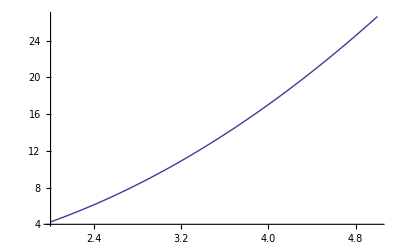

```mathematica
Plot[ToFundamentalSI[((Eb GeV)^2/(Subscript[m, p] c^2))/GeV],{Eb,2,5 }]
```

The function PhysicalUnitsPlot can simplify this.  See the following examples.

#### Tests with explicit units

Consider the example above.   Note that units can now be present in the range specification.

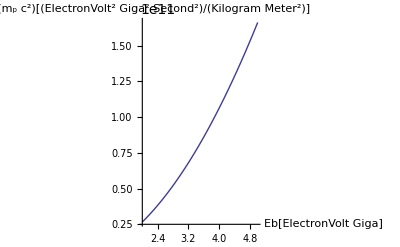

```mathematica
PhysicalUnitsPlot[Eb^2/(Subscript[m, p] c^2),{Eb,2 GeV,5 GeV}]
```

Inconsistent units will not plot.

```mathematica
PhysicalUnitsPlot[Evaluate[Eb^2],{Eb,2  Pascal Meter,5 GeV}]
```

PhysicalUnitsPlot[Eb^2,{Eb,2 Pascal Meter,5 GeV}]

```mathematica
PhysicalUnitsPlot[Eb^2,{Eb,2 Pascal Meter,5 GeV}]
```

PhysicalUnitsPlot[Eb^2,{Eb,2 Pascal Meter,5 GeV}]

but consistent units will

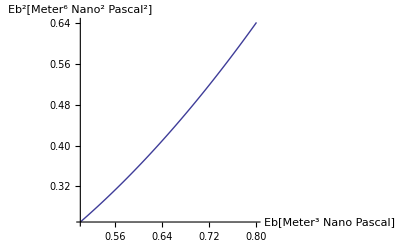

```mathematica
PhysicalUnitsPlot[Eb^2,{Eb,.5 Nano Pascal Meter^3,5 GeV}]
```

Constants and units from the package work in many ways

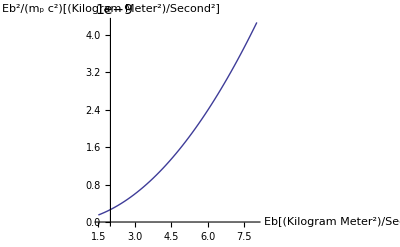

```mathematica
PhysicalUnitsPlot[Eb^2/(Subscript[m, p] c^2),{Eb,N[Subscript[m, p] c^2],5 GeV}]
```

Note that the units of the abscissa are taken from the evaluation of the lower limit of the range.  This can be changed by forcing a conversion.

```mathematica
PhysicalUnitsPlot[Eb^2/(Subscript[m, p] c^2),{Eb,Convert[N[ Subscript[m, p] c^2],MeV],3 GeV}]
```

-Graphics-

Since the literal form in which the function is specified is used for the label of the vertical axis, another approach may be needed to convert the units of the function itself

```mathematica
PhysicalUnitsPlot[Convert[Eb^2/(Subscript[m, p] c^2),GeV],{Eb,Convert[N[ Subscript[m, p] c^2],MeV],3 GeV}]
```

Convert::incomp: Incompatible units in Eb^2/c^2\ m_p and ElectronVolt\ Giga.

-Graphics-

One possibility is

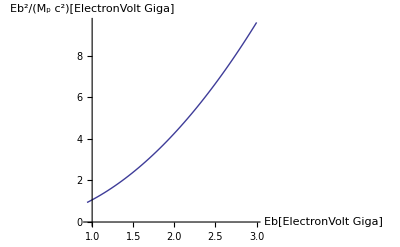

```mathematica
Subscript[M, p]=Convert[N[Subscript[m, p]],GeV/c^2];
PhysicalUnitsPlot[Eb^2/(Subscript[M, p] c^2),{Eb,Convert[N[ Subscript[m, p] c^2],GeV],3 GeV}]
```

and another is to define a new notation

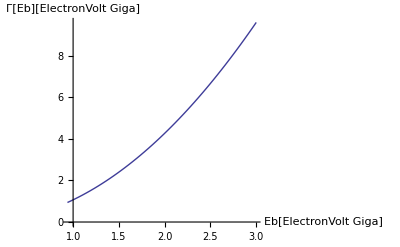

```mathematica
Γ[Eb]=Convert[N[Eb^2/(Subscript[m, p] c^2)],Eb^2 GeV^-1];
PhysicalUnitsPlot[Γ[Eb],{Eb,Convert[N[ Subscript[m, p] c^2],GeV],3 GeV}]
```

#### Plotting with mixtures of units

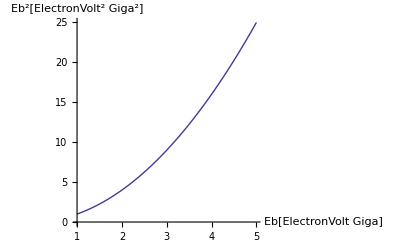

```mathematica
PhysicalUnitsPlot[Eb^2,{Eb,1 GeV, 5000 MeV}]
```

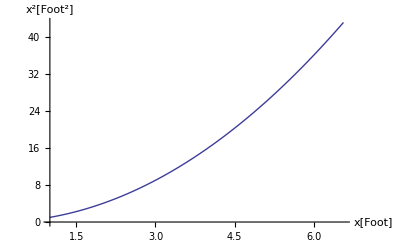

```mathematica
PhysicalUnitsPlot[ x^2 ,{x,1 Foot,2 Meter}]
```

This picks up inconsistent units

```mathematica
PhysicalUnitsPlot[ x^2 +10x,{x,1 Foot,2 Meter}]
```

Units of ordinate appear to be inconsistent.

which might be fixed with

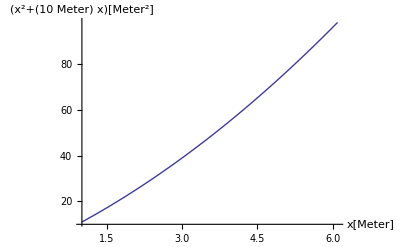

```mathematica
PhysicalUnitsPlot[ x^2 +(10 Meter)  x,{x,1 Meter,20 Foot}]
```

But there are still some limitations:

```mathematica
PhysicalUnitsPlot[ x^2 +(10 Meter)  x,{x,1 Foot,2 Meter}]
```

Units of ordinate appear to be inconsistent.

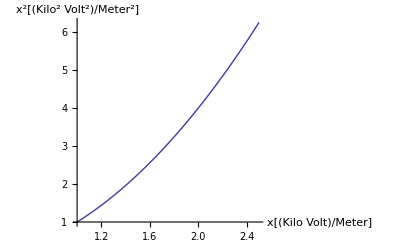

```mathematica
PhysicalUnitsPlot[x^2 ,{x,1 (Kilo Volt)/Meter,2500 Newton/Coulomb}]
```

#### Tests with other options

All the options of Plot work for PhysicalUnitsPlot.  The one exceptions is AxesLabel.

The default graphic size may be too small so that the axes labels crowd out the plot itself.

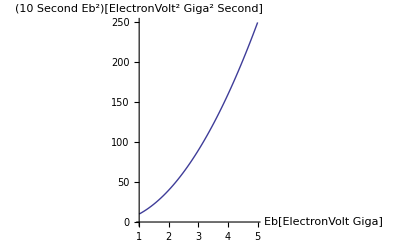

```mathematica
PhysicalUnitsPlot[10 Second Eb^2,{Eb,1 GeV, 5000 MeV}]
```

One solution is to simply increase the graphics size in the Front End with the mouse. Alternatively change the ImageSize option.

```mathematica
PhysicalUnitsPlot[10 Second Eb^2,{Eb,1 GeV, 5000 MeV},ImageSize->{400,200}]
```

-Graphics-

As usual, this can be arranged permanently with

```mathematica
SetOptions[PhysicalUnitsPlot,ImageSize->{400,200}];
```

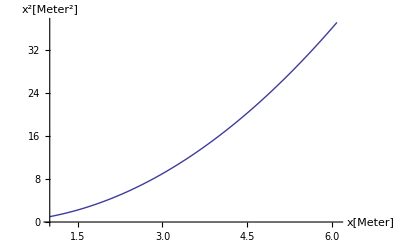

```mathematica
PhysicalUnitsPlot[ x^2 ,{x,1 Meter,20 Foot}]
```

Other options are used in the usual way.

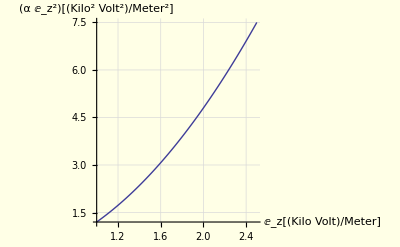

```mathematica
α=1.2;
PhysicalUnitsPlot[α Subscript[E, z]^2 ,{Subscript[E, z],1 (Kilo Volt)/Meter,2500 Newton/Coulomb},Background->RGBColor[1,1,.9],GridLines->Automatic]
```

As expected the AxesLabel  option is simply ignored.

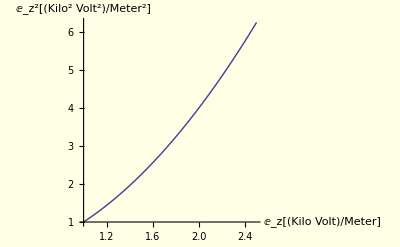

```mathematica
PhysicalUnitsPlot[Subscript[E, z]^2 ,{Subscript[E, z],1 (Kilo Volt)/Meter,2500 Newton/Coulomb},Background->RGBColor[1,1,.9],AxesLabel->{"x","y"}]
```

### Finding out about everything defined by the package

You can list all the symbols defined by the package with

```mathematica
TableForm[Names["Accelerator`ConstantsUnits`*"]]
```

a⎵Subscript⎵Infinity
c
ClassicalProtonRadius
ConstantsUnits
DimensionCheck
e
GeV
G⎵Subscript⎵e
IntroduceSymbol
keV
MeV
m⎵Subscript⎵d
m⎵Subscript⎵e
m⎵Subscript⎵n
m⎵Subscript⎵p
m⎵Subscript⎵W
m⎵Subscript⎵Z
m⎵Subscript⎵μ
NumericalValue
NumericalValueUnits
PhysicalUnits
PhysicalUnitsPlot
r⎵Subscript⎵e
r⎵Subscript⎵p
SymbolsUnits
TeV
ToFundamentalSI
Z⎵Subscript⎵0
α⎵Subscript⎵s
ϵ⎵Subscript⎵0
λ⎵Overscript⎵Underscore⎵Subscript⎵e
λ⎵Subscript⎵e
μ⎵Subscript⎵0
μ⎵Subscript⎵B
μ⎵Subscript⎵N
σ⎵Subscript⎵SB
σ⎵Subscript⎵T
ℏ

Note that this actually displays the FullForm versions of the compound symbols available on the palette.  However it lets you see the names of the other symbols that are not visible on the palette.

It does not list the many physical constants and units available from the standard packages, only the ones we gave special treatment to.   This list may be changed in future.  Your feedback is welcome.   The constants and units defined by the standard packages can be listed with

```mathematica
TableForm[Names["Miscellaneous`PhysicalConstants`*"]]
```

{}

```mathematica
TableForm[Names["Miscellaneous`Units`*"]]
```

{}

## Input Palette

Mathematica's palettes provide a convenient way to input commands without having to remember their names or  syntax. They also help considerably to reduce syntax errors when you build up complex expressions. By selecting it and then using the File/Generate Palette from Selection command, the following input cell can be transformed into a palette containing templates for the most useful commands in this package.

```mathematica
{{Subscript[r, e], c, e, ℏ, Subscript[α, s], Subscript[λ, e], Subscript[λ̄, e], Subscript[Z, 0]}, {Subscript[r, p], Subscript[μ, 0], Subscript[ϵ, 0], Subscript[G, e], Subscript[a, ∞], Subscript[μ, B], Subscript[μ, N], Subscript[σ, T]}, {Subscript[m, e], Subscript[m, p], Subscript[m, n], Subscript[m, d], Subscript[m, μ], Subscript[m, Z], Subscript[m, W], Subscript[σ, SB]}}
{{{{Convert[■,□], , SI[■]}}}, {ToFundamentalSI[■]}, {DimensionCheck[■]}, {Notation[■ ⟺ □];
IntroduceSymbol[□,"is the □.",□];}, {SymbolsUnits[]}}
```

{{r_e,c,e,ℏ,α_s,λ_e,(λ̄)_e,Z_0},{r_p,μ_0,ϵ_0,G_e,a_∞,μ_B,μ_N,σ_T},{m_e,m_p,m_n,m_d,m_μ,m_Z,m_W,σ_SB}}

{{{{■,Null,■}}},{■},{■},{Null^2},{{{a_∞,Meter},{c,Meter/Second},{e,Coulomb},{G_e,1},{m_d,Kilogram},{m_e,Kilogram},{m_n,Kilogram},{m_p,Kilogram},{m_W,Kilogram},{m_Z,Kilogram},{m_μ,Kilogram},{r_e,Meter},{r_p,Meter},{Z_0,Ohm},{α_s,1},{ϵ_0,Farad/Meter},{(λ̄)_e,Meter},{λ_e,Meter},{μ_0,Henry/Meter},{μ_B,Joule/Tesla},{μ_N,Joule/Tesla},{σ_SB,Watt/(Kelvin^4 Meter^2)},{σ_T,Meter^2},{ℏ,Joule Second},{λ_Q,Meter},{E_b,ElectronVolt Giga},{a_θ,1},{ρ,Meter},{ρ_y,Meter},{■,■}}}}

The Notation and IntroduceSymbol functions are combined in a single button for convenience.  Remember that the same alias (e.g. rhoy for ρ_y must be entered in both the red slots.

The package is normally set up to open a palette file called ConstantsUnitsPalette.nb in its source directory when the package is loaded.  Normally this palette is generated from the above cell.

The option ShowGroupOpenCloseIcon->True is useful in palettes.  Note that the palette buttons for functions are most useful if you first select a part of an expression on your screen to which you want to apply them.

Generating your own palette from this notebook has the advantage that you can modify it to your taste.  Otherwise, the default ready-made palette will appear automatically on your screen when you load the package (if you don't want it, just close it).

## Bibliography

[1] Stephen Wolfram, The Mathematica Book, 3rd ed., Wolfram Media/Cambridge University Press, 1996.

[2]  Roman Maeder, Programming in Mathematica, 3rd ed. Addison-Wesley, 1996

[3] A.W. Chao, M. Tigner (Eds.), Handbook of Accelerator Physics and Engineeering, World Scientific, Singapore, 1999.

http://www.wspc.com/books/physics/3818.html

[4] Stephen G. Benka (Ed.), Physics Today, Vol. 51, No. 8, Part 2, Buyers Guide, American Institute of Physics, New York, August 1998